```mathematica
(*//first Col.:Star No.
//Second Col.:Number of shower tracks
//Third Col.:Number of gray tracks
//Forth Col.:Number of black tracks
//Gt,st,bt :numbers of gray,shower,black tracks in all events  
//cgs: correlation between gray and shower tracks 
//ShowerMul:shower multiplicity in each star"*)
(*//Freq_shower,Freq_gray,Freq_black:frequency of cetain multiplicity (shower,gray,black)
//PT_S1:trasverse momentum of shower track of index
//trasverse momentum calculated by: p_t=p_0*A_f *sin(θ_s);
P_0is the momentum of the incident projectile(=4.5 Gev/c), 
A_F is the mass number of the projectile fragment(A_f=28), 
θ_s is the emission angle (space angle) of the fragments.
*)
```

```mathematica
Multiplicityplates=({{1, 2, 5, 4}, {2, 5, 6, 8}, {3, 3, 6, 5}, {4, 11, 5, 2}, {5, 10, 11, 1}, {6, 14, 6, 3}, {7, 4, 5, 5}, {8, 3, 5, 4}, {9, 7, 14, 4}, {10, 1, 8, 3}, {11, 6, 15, 3}, {12, 7, 10, 3}, {13, 6, 8, 7}, {14, 10, 6, 3}, {15, 3, 11, 1}, {16, 1, 13, 5}, {17, 1, 5, 4}, {18, 12, 6, 3}, {19, 0, 6, 4}, {20, 1, 5, 2}, {21, 0, 13, 5}, {22, 1, 6, 3}, {23, 2, 9, 5}, {24, 3, 10, 4}, {25, 1, 6, 2}, {26, 2, 7, 4}, {27, 4, 9, 5}, {28, 7, 12, 4}, {29, 3, 8, 2}, {30, 2, 9, 4}, {31, 3, 12, 6}, {32, 2, 7, 3}, {33, 5, 12, 4}, {34, 6, 15, 3}, {35, 12, 8, 2}, {36, 0, 8, 1}, {37, 14, 11, 3}, {38, 0, 5, 1}, {39, 6, 9, 1}, {40, 1, 6, 2}, {41, 2, 3, 3}, {42, 4, 9, 0}, {43, 3, 6, 1}, {44, 14, 14, 1}, {45, 0, 5, 1}, {46, 7, 14, 4}, {47, 1, 8, 1}, {48, 11, 16, 3}, {49, 7, 11, 2}, {50, 2, 6, 4}, {51, 2, 3, 1}, {52, 4, 6, 1}, {53, 2, 7, 0}, {54, 2, 8, 3}, {55, 2, 8, 5}, {56, 1, 7, 1}, {57, 1, 11, 1}, {58, 1, 9, 3}, {59, 2, 7, 2}, {60, 2, 5, 4}, {61, 3, 6, 5}, {62, 3, 9, 2}, {63, 7, 16, 2}, {64, 2, 2, 4}, {65, 9, 21, 3}, {66, 1, 5, 3}, {67, 4, 8, 0}, {68, 0, 5, 0}, {69, 1, 5, 1}, {70, 4, 7, 1}, {71, 1, 13, 1}, {72, 3, 2, 2}, {73, 7, 13, 3}, {74, 1, 4, 1}, {75, 4, 4, 3}, {76, 4, 9, 3}, {77, 6, 10, 5}, {78, 1, 4, 5}, {79, 2, 6, 2}, {80, 2, 3, 3}, {81, 12, 14, 1}, {82, 2, 12, 2}, {83, 1, 8, 3}, {84, 2, 5, 2}, {85, 1, 7, 2}, {86, 4, 4, 2}, {87, 7, 14, 1}, {88, 1, 8, 3}, {89, 3, 6, 3}, {90, 11, 9, 2}, {91, 1, 7, 2}, {92, 10, 8, 2}, {93, 2, 6, 3}, {94, 3, 5, 3}, {95, 3, 16, 2}, {96, 1, 6, 1}, {97, 3, 7, 2}, {98, 2, 9, 1}, {99, 6, 10, 4}, {100, 6, 12, 2}, {101, 3, 5, 1}, {102, 4, 8, 3}, {103, 3, 6, 4}, {104, 10, 8, 2}, {105, 4, 13, 3}, {106, 2, 7, 3}, {107, 1, 3, 3}, {108, 3, 7, 4}, {109, 9, 12, 3}, {110, 8, 10, 4}, {111, 2, 5, 4}, {112, 4, 3, 2}, {113, 1, 6, 2}, {114, 5, 6, 3}, {115, 3, 10, 2}, {116, 2, 5, 2}, {117, 3, 7, 2}, {118, 8, 9, 3}, {119, 6, 8, 3}, {120, 5, 10, 2}, {121, 12, 6, 3}, {122, 5, 8, 1}, {123, 3, 9, 5}, {124, 3, 7, 0}, {125, 7, 9, 1}, {126, 10, 6, 3}, {127, 11, 16, 3}, {128, 10, 6, 3}, {129, 3, 7, 4}, {130, 16, 15, 2}, {131, 8, 13, 4}, {132, 2, 5, 4}, {133, 7, 15, 3}, {134, 8, 18, 2}, {135, 4, 7, 5}, {136, 3, 6, 4}, {137, 4, 6, 1}, {138, 10, 21, 3}, {139, 5, 9, 4}, {140, 10, 11, 1}, {141, 3, 9, 5}, {142, 13, 11, 2}, {143, 5, 9, 1}, {144, 4, 10, 2}, {145, 6, 8, 3}, {146, 4, 10, 2}, {147, 5, 10, 0}, {148, 7, 14, 4}, {149, 1, 14, 3}, {150, 3, 6, 2}, {151, 2, 7, 1}, {152, 0, 4, 1}, {153, 3, 9, 2}, {154, 5, 13, 4}, {155, 8, 12, 3}, {156, 4, 11, 4}, {157, 9, 14, 1}, {158, 5, 15, 2}, {159, 2, 9, 1}, {160, 4, 6, 3}, {161, 11, 5, 2}, {162, 2, 4, 2}, {163, 12, 14, 2}, {164, 10, 13, 4}, {165, 3, 12, 2}, {166, 2, 8, 3}, {167, 4, 12, 2}, {168, 4, 7, 1}})
```

{{1,2,5,4},{2,5,6,8},{3,3,6,5},{4,11,5,2},{5,10,11,1},{6,14,6,3},{7,4,5,5},{8,3,5,4},{9,7,14,4},{10,1,8,3},{11,6,15,3},{12,7,10,3},{13,6,8,7},{14,10,6,3},{15,3,11,1},{16,1,13,5},{17,1,5,4},{18,12,6,3},{19,0,6,4},{20,1,5,2},{21,0,13,5},{22,1,6,3},{23,2,9,5},{24,3,10,4},{25,1,6,2},{26,2,7,4},{27,4,9,5},{28,7,12,4},{29,3,8,2},{30,2,9,4},{31,3,12,6},{32,2,7,3},{33,5,12,4},{34,6,15,3},{35,12,8,2},{36,0,8,1},{37,14,11,3},{38,0,5,1},{39,6,9,1},{40,1,6,2},{41,2,3,3},{42,4,9,0},{43,3,6,1},{44,14,14,1},{45,0,5,1},{46,7,14,4},{47,1,8,1},{48,11,16,3},{49,7,11,2},{50,2,6,4},{51,2,3,1},{52,4,6,1},{53,2,7,0},{54,2,8,3},{55,2,8,5},{56,1,7,1},{57,1,11,1},{58,1,9,3},{59,2,7,2},{60,2,5,4},{61,3,6,5},{62,3,9,2},{63,7,16,2},{64,2,2,4},{65,9,21,3},{66,1,5,3},{67,4,8,0},{68,0,5,0},{69,1,5,1},{70,4,7,1},{71,1,13,1},{72,3,2,2},{73,7,13,3},{74,1,4,1},{75,4,4,3},{76,4,9,3},{77,6,10,5},{78,1,4,5},{79,2,6,2},{80,2,3,3},{81,12,14,1},{82,2,12,2},{83,1,8,3},{84,2,5,2},{85,1,7,2},{86,4,4,2},{87,7,14,1},{88,1,8,3},{89,3,6,3},{90,11,9,2},{91,1,7,2},{92,10,8,2},{93,2,6,3},{94,3,5,3},{95,3,16,2},{96,1,6,1},{97,3,7,2},{98,2,9,1},{99,6,10,4},{100,6,12,2},{101,3,5,1},{102,4,8,3},{103,3,6,4},{104,10,8,2},{105,4,13,3},{106,2,7,3},{107,1,3,3},{108,3,7,4},{109,9,12,3},{110,8,10,4},{111,2,5,4},{112,4,3,2},{113,1,6,2},{114,5,6,3},{115,3,10,2},{116,2,5,2},{117,3,7,2},{118,8,9,3},{119,6,8,3},{120,5,10,2},{121,12,6,3},{122,5,8,1},{123,3,9,5},{124,3,7,0},{125,7,9,1},{126,10,6,3},{127,11,16,3},{128,10,6,3},{129,3,7,4},{130,16,15,2},{131,8,13,4},{132,2,5,4},{133,7,15,3},{134,8,18,2},{135,4,7,5},{136,3,6,4},{137,4,6,1},{138,10,21,3},{139,5,9,4},{140,10,11,1},{141,3,9,5},{142,13,11,2},{143,5,9,1},{144,4,10,2},{145,6,8,3},{146,4,10,2},{147,5,10,0},{148,7,14,4},{149,1,14,3},{150,3,6,2},{151,2,7,1},{152,0,4,1},{153,3,9,2},{154,5,13,4},{155,8,12,3},{156,4,11,4},{157,9,14,1},{158,5,15,2},{159,2,9,1},{160,4,6,3},{161,11,5,2},{162,2,4,2},{163,12,14,2},{164,10,13,4},{165,3,12,2},{166,2,8,3},{167,4,12,2},{168,4,7,1}}

```mathematica
MultiplicityP12={{1,2,5,4},{2,5,6,8},{3,3,6,5},{4,11,5,2},{5,10,11,1},{6,14,6,3},{7,4,5,5},{8,3,5,4},{9,7,14,4},{10,1,8,3},{11,6,15,3},{12,7,10,3},{13,6,8,7},{14,10,6,3},{15,3,11,1},{16,1,13,5},{17,1,5,4},{18,12,6,3},{19,0,6,4},{20,1,5,2},{21,0,13,5},{22,1,6,3},{23,2,9,5},{24,3,10,4},{25,1,6,2},{26,2,7,4},{27,4,9,5},{28,7,12,4},{29,3,8,2},{30,2,9,4},{31,3,12,6},{32,2,7,3},{33,5,12,4},{34,6,15,3},{35,12,8,2},{36,0,8,1},{37,14,11,3},{38,0,5,1},{39,6,9,1},{40,1,6,2},{41,2,3,3},{42,4,9,0},{43,3,6,1},{44,14,14,1},{45,0,5,1},{46,7,14,4},{47,1,8,1},{48,11,16,3},{49,7,11,2},{50,2,6,4},{51,2,3,1},{52,4,6,1},{53,2,7,0},{54,2,8,3},{55,2,8,5},{56,1,7,1},{57,1,11,1},{58,1,9,3},{59,2,7,2},{60,2,5,4},{61,3,6,5},{62,3,9,2},{63,7,16,2},{64,2,2,4},{65,9,21,3},{66,1,5,3},{67,4,8,0},{68,0,5,0},{69,1,5,1},{70,4,7,1},{71,1,13,1},{72,3,2,2},{73,7,13,3},{74,1,4,1},{75,4,4,3},{76,4,9,3},{77,6,10,5},{78,1,4,5},{79,2,6,2},{80,2,3,3},{81,12,14,1},{82,2,12,2},{83,1,8,3},{84,2,5,2},{85,1,7,2},{86,4,4,2},{87,7,14,1},{88,1,8,3},{89,3,6,3},{90,11,9,2},{91,1,7,2},{92,10,8,2},{93,2,6,3},{94,3,5,3},{95,3,16,2},{96,1,6,1},{97,3,7,2},{98,2,9,1},{99,6,10,4},{100,6,12,2},{101,3,5,1},{102,4,8,3},{103,3,6,4},{104,10,8,2},{105,4,13,3},{106,2,7,3},{107,1,3,3},{108,3,7,4},{109,9,12,3},{110,8,10,4},{111,2,5,4},{112,4,3,2},{113,1,6,2},{114,5,6,3},{115,3,10,2},{116,2,5,2},{117,3,7,2},{118,8,9,3},{119,6,8,3},{120,5,10,2},{121,12,6,3},{122,5,8,1},{123,3,9,5},{124,3,7,0},{125,7,9,1},{126,10,6,3},{127,11,16,3},{128,10,6,3},{129,3,7,4},{130,16,15,2},{131,8,13,4},{132,2,5,4},{133,7,15,3},{134,8,18,2},{135,4,7,5},{136,3,6,4},{137,4,6,1},{138,10,21,3},{139,5,9,4},{140,10,11,1},{141,3,9,5},{142,13,11,2},{143,5,9,1},{144,4,10,2},{145,6,8,3},{146,4,10,2},{147,5,10,0},{148,7,14,4},{149,1,14,3},{150,3,6,2},{151,2,7,1},{152,0,4,1},{153,3,9,2},{154,5,13,4},{155,8,12,3},{156,4,11,4},{157,9,14,1},{158,5,15,2},{159,2,9,1},{160,4,6,3},{161,11,5,2},{162,2,4,2},{163,12,14,2},{164,10,13,4},{165,3,12,2},{166,2,8,3},{167,4,12,2},{168,4,7,1}}
```

{{1,2,5,4},{2,5,6,8},{3,3,6,5},{4,11,5,2},{5,10,11,1},{6,14,6,3},{7,4,5,5},{8,3,5,4},{9,7,14,4},{10,1,8,3},{11,6,15,3},{12,7,10,3},{13,6,8,7},{14,10,6,3},{15,3,11,1},{16,1,13,5},{17,1,5,4},{18,12,6,3},{19,0,6,4},{20,1,5,2},{21,0,13,5},{22,1,6,3},{23,2,9,5},{24,3,10,4},{25,1,6,2},{26,2,7,4},{27,4,9,5},{28,7,12,4},{29,3,8,2},{30,2,9,4},{31,3,12,6},{32,2,7,3},{33,5,12,4},{34,6,15,3},{35,12,8,2},{36,0,8,1},{37,14,11,3},{38,0,5,1},{39,6,9,1},{40,1,6,2},{41,2,3,3},{42,4,9,0},{43,3,6,1},{44,14,14,1},{45,0,5,1},{46,7,14,4},{47,1,8,1},{48,11,16,3},{49,7,11,2},{50,2,6,4},{51,2,3,1},{52,4,6,1},{53,2,7,0},{54,2,8,3},{55,2,8,5},{56,1,7,1},{57,1,11,1},{58,1,9,3},{59,2,7,2},{60,2,5,4},{61,3,6,5},{62,3,9,2},{63,7,16,2},{64,2,2,4},{65,9,21,3},{66,1,5,3},{67,4,8,0},{68,0,5,0},{69,1,5,1},{70,4,7,1},{71,1,13,1},{72,3,2,2},{73,7,13,3},{74,1,4,1},{75,4,4,3},{76,4,9,3},{77,6,10,5},{78,1,4,5},{79,2,6,2},{80,2,3,3},{81,12,14,1},{82,2,12,2},{83,1,8,3},{84,2,5,2},{85,1,7,2},{86,4,4,2},{87,7,14,1},{88,1,8,3},{89,3,6,3},{90,11,9,2},{91,1,7,2},{92,10,8,2},{93,2,6,3},{94,3,5,3},{95,3,16,2},{96,1,6,1},{97,3,7,2},{98,2,9,1},{99,6,10,4},{100,6,12,2},{101,3,5,1},{102,4,8,3},{103,3,6,4},{104,10,8,2},{105,4,13,3},{106,2,7,3},{107,1,3,3},{108,3,7,4},{109,9,12,3},{110,8,10,4},{111,2,5,4},{112,4,3,2},{113,1,6,2},{114,5,6,3},{115,3,10,2},{116,2,5,2},{117,3,7,2},{118,8,9,3},{119,6,8,3},{120,5,10,2},{121,12,6,3},{122,5,8,1},{123,3,9,5},{124,3,7,0},{125,7,9,1},{126,10,6,3},{127,11,16,3},{128,10,6,3},{129,3,7,4},{130,16,15,2},{131,8,13,4},{132,2,5,4},{133,7,15,3},{134,8,18,2},{135,4,7,5},{136,3,6,4},{137,4,6,1},{138,10,21,3},{139,5,9,4},{140,10,11,1},{141,3,9,5},{142,13,11,2},{143,5,9,1},{144,4,10,2},{145,6,8,3},{146,4,10,2},{147,5,10,0},{148,7,14,4},{149,1,14,3},{150,3,6,2},{151,2,7,1},{152,0,4,1},{153,3,9,2},{154,5,13,4},{155,8,12,3},{156,4,11,4},{157,9,14,1},{158,5,15,2},{159,2,9,1},{160,4,6,3},{161,11,5,2},{162,2,4,2},{163,12,14,2},{164,10,13,4},{165,3,12,2},{166,2,8,3},{167,4,12,2},{168,4,7,1}}

```mathematica
Gt=Table[MultiplicityP12[[j,3]],{j,1,168}]
```

{5,6,6,5,11,6,5,5,14,8,15,10,8,6,11,13,5,6,6,5,13,6,9,10,6,7,9,12,8,9,12,7,12,15,8,8,11,5,9,6,3,9,6,14,5,14,8,16,11,6,3,6,7,8,8,7,11,9,7,5,6,9,16,2,21,5,8,5,5,7,13,2,13,4,4,9,10,4,6,3,14,12,8,5,7,4,14,8,6,9,7,8,6,5,16,6,7,9,10,12,5,8,6,8,13,7,3,7,12,10,5,3,6,6,10,5,7,9,8,10,6,8,9,7,9,6,16,6,7,15,13,5,15,18,7,6,6,21,9,11,9,11,9,10,8,10,10,14,14,6,7,4,9,13,12,11,14,15,9,6,5,4,14,13,12,8,12,7}

```mathematica
Ng={5,6,6,5,11,6,5,5,14,8,15,10,7,6,12,13,5,6,6,5,13,6,9,10,6,7,9,12,8,9,12,7,12,15,8,8,11,5,9,6,3,9,9,11,5,18,8,16,11,6,3,6,7,8,8,7,11,9,7,5,6,9,16,2,21,5,8,5,5,7,13,2,13,4,4,9,10,4,6,3,14,12,8,5,7,4,14,8,6,9,7,8,6,5,16,6,7,9,10,12,5,8,2,8,13,7,3,7,12,10,5,3,6,6,9,5,7,9,8,10,6,8,9,7,9,6,16,6,7,14,13,5,15,18,7,6,5,21,9,11,9,11,9,10,8,10,10,14,13,6,7,4,9,13,12,11,14,15,9,6,5,4,14,13,12,8,12,7}
```

{5,6,6,5,11,6,5,5,14,8,15,10,7,6,12,13,5,6,6,5,13,6,9,10,6,7,9,12,8,9,12,7,12,15,8,8,11,5,9,6,3,9,9,11,5,18,8,16,11,6,3,6,7,8,8,7,11,9,7,5,6,9,16,2,21,5,8,5,5,7,13,2,13,4,4,9,10,4,6,3,14,12,8,5,7,4,14,8,6,9,7,8,6,5,16,6,7,9,10,12,5,8,2,8,13,7,3,7,12,10,5,3,6,6,9,5,7,9,8,10,6,8,9,7,9,6,16,6,7,14,13,5,15,18,7,6,5,21,9,11,9,11,9,10,8,10,10,14,13,6,7,4,9,13,12,11,14,15,9,6,5,4,14,13,12,8,12,7}

```mathematica
st=Table[MultiplicityP12[[j,2]],{j,1,168}]
```

{2,5,3,11,10,14,4,3,7,1,6,7,6,10,3,1,1,12,0,1,0,1,2,3,1,2,4,7,3,2,3,2,5,6,12,0,14,0,6,1,2,4,3,14,0,7,1,11,7,2,2,4,2,2,2,1,1,1,2,2,3,3,7,2,9,1,4,0,1,4,1,3,7,1,4,4,6,1,2,2,12,2,1,2,1,4,7,1,3,11,1,10,2,3,3,1,3,2,6,6,3,4,3,10,4,2,1,3,9,8,2,4,1,5,3,2,3,8,6,5,12,5,3,3,7,10,11,10,3,16,8,2,7,8,4,3,4,10,5,10,3,13,5,4,6,4,5,7,1,3,2,0,3,5,8,4,9,5,2,4,11,2,12,10,3,2,4,4}

```mathematica
Ns={2,5,3,11,10,14,4,3,7,1,6,7,6,10,3,1,1,12,0,1,0,1,2,3,1,2,4,7,3,2,3,2,5,6,12,0,14,0,6,1,2,4,3,18,0,10,1,11,7,2,2,4,2,2,2,1,1,1,2,2,3,3,7,2,9,1,4,0,1,4,1,3,7,1,4,4,6,1,2,2,12,2,1,2,1,4,7,1,3,11,1,10,2,3,3,1,3,2,6,5,3,2,2,10,4,2,1,3,9,7,2,4,1,5,3,1,3,1,5,5,12,5,3,3,7,10,11,10,3,15,8,2,7,8,4,3,4,10,5,10,3,13,4,4,6,4,5,7,1,3,2,0,3,5,7,4,9,5,2,4,11,2,12,10,3,2,4,4}
```

{2,5,3,11,10,14,4,3,7,1,6,7,6,10,3,1,1,12,0,1,0,1,2,3,1,2,4,7,3,2,3,2,5,6,12,0,14,0,6,1,2,4,3,18,0,10,1,11,7,2,2,4,2,2,2,1,1,1,2,2,3,3,7,2,9,1,4,0,1,4,1,3,7,1,4,4,6,1,2,2,12,2,1,2,1,4,7,1,3,11,1,10,2,3,3,1,3,2,6,5,3,2,2,10,4,2,1,3,9,7,2,4,1,5,3,1,3,1,5,5,12,5,3,3,7,10,11,10,3,15,8,2,7,8,4,3,4,10,5,10,3,13,4,4,6,4,5,7,1,3,2,0,3,5,7,4,9,5,2,4,11,2,12,10,3,2,4,4}

```mathematica
Bt=Table[MultiplicityP12[[j,4]],{j,1,168}]
```

{4,8,5,2,1,3,5,4,4,3,3,3,7,3,1,5,4,3,4,2,5,3,5,4,2,4,5,4,2,4,6,3,4,3,2,1,3,1,1,2,3,0,1,1,1,4,1,3,2,4,1,1,0,3,5,1,1,3,2,4,5,2,2,4,3,3,0,0,1,1,1,2,3,1,3,3,5,5,2,3,1,2,3,2,2,2,1,3,3,2,2,2,3,3,2,1,2,1,4,2,1,3,4,2,3,3,3,4,3,4,4,2,2,3,2,2,2,3,3,2,3,1,5,0,1,3,3,3,4,2,4,4,3,2,5,4,1,3,4,1,5,2,1,2,3,2,0,4,3,2,1,1,2,4,3,4,1,2,1,3,2,2,2,4,2,3,2,1}

```mathematica
Nb={4,8,5,2,1,3,5,4,4,3,3,3,8,3,1,5,4,3,4,2,5,3,5,4,2,4,5,4,2,4,6,3,4,3,2,1,3,1,1,2,3,0,1,1,1,3,1,3,2,4,1,1,0,3,5,1,1,3,2,4,5,2,2,4,3,3,0,0,1,1,1,2,3,1,3,3,5,5,2,3,1,2,3,2,2,2,1,3,3,2,2,2,3,3,2,1,2,1,4,2,1,3,4,2,3,3,3,4,3,5,4,2,2,3,2,2,4,3,3,2,3,1,5,0,1,3,3,3,4,2,4,4,3,2,5,4,1,3,4,1,5,2,0,2,3,2,0,4,3,2,1,1,2,4,4,6,1,2,1,3,2,2,2,4,2,3,2,1}
```

{4,8,5,2,1,3,5,4,4,3,3,3,8,3,1,5,4,3,4,2,5,3,5,4,2,4,5,4,2,4,6,3,4,3,2,1,3,1,1,2,3,0,1,1,1,3,1,3,2,4,1,1,0,3,5,1,1,3,2,4,5,2,2,4,3,3,0,0,1,1,1,2,3,1,3,3,5,5,2,3,1,2,3,2,2,2,1,3,3,2,2,2,3,3,2,1,2,1,4,2,1,3,4,2,3,3,3,4,3,5,4,2,2,3,2,2,4,3,3,2,3,1,5,0,1,3,3,3,4,2,4,4,3,2,5,4,1,3,4,1,5,2,0,2,3,2,0,4,3,2,1,1,2,4,4,6,1,2,1,3,2,2,2,4,2,3,2,1}

```mathematica
cgs=Table[MultiplicityP12[[j,i]],{j,1,168},{i,2,3}]
```

{{2,5},{5,6},{3,6},{11,5},{10,11},{14,6},{4,5},{3,5},{7,14},{1,8},{6,15},{7,10},{6,8},{10,6},{3,11},{1,13},{1,5},{12,6},{0,6},{1,5},{0,13},{1,6},{2,9},{3,10},{1,6},{2,7},{4,9},{7,12},{3,8},{2,9},{3,12},{2,7},{5,12},{6,15},{12,8},{0,8},{14,11},{0,5},{6,9},{1,6},{2,3},{4,9},{3,6},{14,14},{0,5},{7,14},{1,8},{11,16},{7,11},{2,6},{2,3},{4,6},{2,7},{2,8},{2,8},{1,7},{1,11},{1,9},{2,7},{2,5},{3,6},{3,9},{7,16},{2,2},{9,21},{1,5},{4,8},{0,5},{1,5},{4,7},{1,13},{3,2},{7,13},{1,4},{4,4},{4,9},{6,10},{1,4},{2,6},{2,3},{12,14},{2,12},{1,8},{2,5},{1,7},{4,4},{7,14},{1,8},{3,6},{11,9},{1,7},{10,8},{2,6},{3,5},{3,16},{1,6},{3,7},{2,9},{6,10},{6,12},{3,5},{4,8},{3,6},{10,8},{4,13},{2,7},{1,3},{3,7},{9,12},{8,10},{2,5},{4,3},{1,6},{5,6},{3,10},{2,5},{3,7},{8,9},{6,8},{5,10},{12,6},{5,8},{3,9},{3,7},{7,9},{10,6},{11,16},{10,6},{3,7},{16,15},{8,13},{2,5},{7,15},{8,18},{4,7},{3,6},{4,6},{10,21},{5,9},{10,11},{3,9},{13,11},{5,9},{4,10},{6,8},{4,10},{5,10},{7,14},{1,14},{3,6},{2,7},{0,4},{3,9},{5,13},{8,12},{4,11},{9,14},{5,15},{2,9},{4,6},{11,5},{2,4},{12,14},{10,13},{3,12},{2,8},{4,12},{4,7}}

```mathematica
CorrGS={{5,2},{6,5},{6,3},{5,11},{11,10},{6,14},{5,4},{5,3},{14,7},{8,1},{15,6},{10,7},{7,6},{6,10},{12,3},{13,1},{5,1},{6,12},{6,0},{5,1},{13,0},{6,1},{9,2},{10,3},{6,1},{7,2},{9,4},{12,7},{8,3},{9,2},{12,3},{7,2},{12,5},{15,6},{8,12},{8,0},{11,14},{5,0},{9,6},{6,1},{3,2},{9,4},{9,3},{11,18},{5,0},{18,10},{8,1},{16,11},{11,7},{6,2},{3,2},{6,4},{7,2},{8,2},{8,2},{7,1},{11,1},{9,1},{7,2},{5,2},{6,3},{9,3},{16,7},{2,2},{21,9},{5,1},{8,4},{5,0},{5,1},{7,4},{13,1},{2,3},{13,7},{4,1},{4,4},{9,4},{10,6},{4,1},{6,2},{3,2},{14,12},{12,2},{8,1},{5,2},{7,1},{4,4},{14,7},{8,1},{6,3},{9,11},{7,1},{8,10},{6,2},{5,3},{16,3},{6,1},{7,3},{9,2},{10,6},{12,5},{5,3},{8,2},{2,2},{8,10},{13,4},{7,2},{3,1},{7,3},{12,9},{10,7},{5,2},{3,4},{6,1},{6,5},{9,3},{5,1},{7,3},{9,1},{8,5},{10,5},{6,12},{8,5},{9,3},{7,3},{9,7},{6,10},{16,11},{6,10},{7,3},{14,15},{13,8},{5,2},{15,7},{18,8},{7,4},{6,3},{5,4},{21,10},{9,5},{11,10},{9,3},{11,13},{9,4},{10,4},{8,6},{10,4},{10,5},{14,7},{13,1},{6,3},{7,2},{4,0},{9,3},{13,5},{12,7},{11,4},{14,9},{15,5},{9,2},{6,4},{5,11},{4,2},{14,12},{13,10},{12,3},{8,2},{12,4},{7,4}}
```

{{5,2},{6,5},{6,3},{5,11},{11,10},{6,14},{5,4},{5,3},{14,7},{8,1},{15,6},{10,7},{7,6},{6,10},{12,3},{13,1},{5,1},{6,12},{6,0},{5,1},{13,0},{6,1},{9,2},{10,3},{6,1},{7,2},{9,4},{12,7},{8,3},{9,2},{12,3},{7,2},{12,5},{15,6},{8,12},{8,0},{11,14},{5,0},{9,6},{6,1},{3,2},{9,4},{9,3},{11,18},{5,0},{18,10},{8,1},{16,11},{11,7},{6,2},{3,2},{6,4},{7,2},{8,2},{8,2},{7,1},{11,1},{9,1},{7,2},{5,2},{6,3},{9,3},{16,7},{2,2},{21,9},{5,1},{8,4},{5,0},{5,1},{7,4},{13,1},{2,3},{13,7},{4,1},{4,4},{9,4},{10,6},{4,1},{6,2},{3,2},{14,12},{12,2},{8,1},{5,2},{7,1},{4,4},{14,7},{8,1},{6,3},{9,11},{7,1},{8,10},{6,2},{5,3},{16,3},{6,1},{7,3},{9,2},{10,6},{12,5},{5,3},{8,2},{2,2},{8,10},{13,4},{7,2},{3,1},{7,3},{12,9},{10,7},{5,2},{3,4},{6,1},{6,5},{9,3},{5,1},{7,3},{9,1},{8,5},{10,5},{6,12},{8,5},{9,3},{7,3},{9,7},{6,10},{16,11},{6,10},{7,3},{14,15},{13,8},{5,2},{15,7},{18,8},{7,4},{6,3},{5,4},{21,10},{9,5},{11,10},{9,3},{11,13},{9,4},{10,4},{8,6},{10,4},{10,5},{14,7},{13,1},{6,3},{7,2},{4,0},{9,3},{13,5},{12,7},{11,4},{14,9},{15,5},{9,2},{6,4},{5,11},{4,2},{14,12},{13,10},{12,3},{8,2},{12,4},{7,4}}

```mathematica
BinCounts[CorrGS]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,3,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,2,1,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,3,5,5,3,2,0,0,0,0,0,0,2,0,0,0,0,0,0,0},{0,1,5,3,5,2,2,0,0,0,0,3,0,2,0,1,0,0,0,0},{0,0,3,6,5,3,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,4,4,1,1,2,1,0,0,0,2,0,1,0,0,0,0,0,0},{0,0,2,4,6,4,1,1,1,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,1,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0,1,0,0,2,0,0,1,1,0,0,0,1},{0,0,0,1,3,1,2,0,2,0,1,0,0,0,0,0,0,0,0,0},{0,1,3,0,0,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,3,0,1,0,0,2,0,0,1,0,0,0},{0,0,0,0,0,0,1,2,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,1,0,0,0,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0}}

```mathematica
BinLists[CorrGS]
```

{{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}},{{},{},{},{{2,2},{2,2}},{{2,3}},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}},{{},{},{{3,1}},{{3,2},{3,2},{3,2}},{},{{3,4}},{},{},{},{},{},{},{},{},{},{},{},{},{},{}},{{},{{4,0}},{{4,1},{4,1}},{{4,2}},{},{{4,4},{4,4}},{},{},{},{},{},{},{},{},{},{},{},{},{},{}},{{},{{5,0},{5,0},{5,0}},{{5,1},{5,1},{5,1},{5,1},{5,1}},{{5,2},{5,2},{5,2},{5,2},{5,2}},{{5,3},{5,3},{5,3}},{{5,4},{5,4}},{},{},{},{},{},{},{{5,11},{5,11}},{},{},{},{},{},{},{}},{{},{{6,0}},{{6,1},{6,1},{6,1},{6,1},{6,1}},{{6,2},{6,2},{6,2}},{{6,3},{6,3},{6,3},{6,3},{6,3}},{{6,4},{6,4}},{{6,5},{6,5}},{},{},{},{},{{6,10},{6,10},{6,10}},{},{{6,12},{6,12}},{},{{6,14}},{},{},{},{}},{{},{},{{7,1},{7,1},{7,1}},{{7,2},{7,2},{7,2},{7,2},{7,2},{7,2}},{{7,3},{7,3},{7,3},{7,3},{7,3}},{{7,4},{7,4},{7,4}},{},{{7,6}},{},{},{},{},{},{},{},{},{},{},{},{}},{{},{{8,0}},{{8,1},{8,1},{8,1},{8,1}},{{8,2},{8,2},{8,2},{8,2}},{{8,3}},{{8,4}},{{8,5},{8,5}},{{8,6}},{},{},{},{{8,10},{8,10}},{},{{8,12}},{},{},{},{},{},{}},{{},{},{{9,1},{9,1}},{{9,2},{9,2},{9,2},{9,2}},{{9,3},{9,3},{9,3},{9,3},{9,3},{9,3}},{{9,4},{9,4},{9,4},{9,4}},{{9,5}},{{9,6}},{{9,7}},{},{},{},{{9,11}},{},{},{},{},{},{},{}},{{},{},{},{},{{10,3}},{{10,4},{10,4}},{{10,5},{10,5}},{{10,6},{10,6}},{{10,7},{10,7}},{},{},{},{},{},{},{},{},{},{},{}},{{},{},{{11,1}},{},{},{{11,4}},{},{},{{11,7}},{},{},{{11,10},{11,10}},{},{},{{11,13}},{{11,14}},{},{},{},{{11,18}}},{{},{},{},{{12,2}},{{12,3},{12,3},{12,3}},{{12,4}},{{12,5},{12,5}},{},{{12,7},{12,7}},{},{{12,9}},{},{},{},{},{},{},{},{},{}},{{},{{13,0}},{{13,1},{13,1},{13,1}},{},{},{{13,4}},{{13,5}},{},{{13,7}},{{13,8}},{},{{13,10}},{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{},{{14,7},{14,7},{14,7}},{},{{14,9}},{},{},{{14,12},{14,12}},{},{},{{14,15}},{},{},{}},{{},{},{},{},{},{},{{15,5}},{{15,6},{15,6}},{{15,7}},{},{},{},{},{},{},{},{},{},{},{}},{{},{},{},{},{{16,3}},{},{},{},{{16,7}},{},{},{},{{16,11},{16,11}},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{},{},{{18,8}},{},{{18,10}},{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}},{{},{},{},{},{},{},{},{},{},{},{{21,9}},{{21,10}},{},{},{},{},{},{},{},{}}}

```mathematica
graydistribution=BinCounts[Gt,{min=2,max=22,interval=1}]
```

{2,5,6,19,27,17,18,18,10,8,9,8,9,5,4,0,1,0,0,2}

```mathematica
{3,5,6,20,24,18,17,20,9,8,10,9,7,4,4,0,2,0,0,2}
```

{3,5,6,20,24,18,17,20,9,8,10,9,7,4,4,0,2,0,0,2}

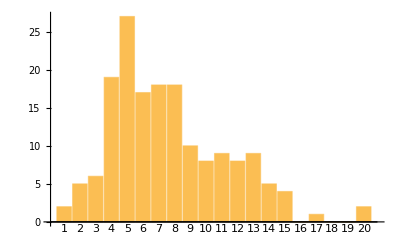

```mathematica
FG=BarChart[graydistribution,ChartLabels->Range[22]]
```

```mathematica
PDF[PDF[PoissonDistribution[6.607142857142858],x]]
```

PDF[Piecewise[{{(0.00135069 6.60714^x)/(x!), x≥0}, {0, True}}]]

```mathematica
gf=(0.0036715445132779194 6.607142857142858^x)/(x!)
```

(0.00367154 6.60714^x)/(x!)

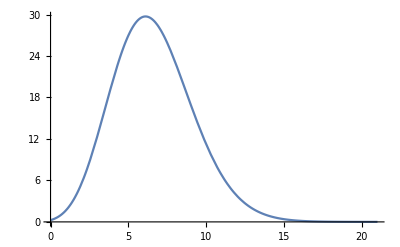

```mathematica
GM=Plot[70*gf,{x,0,21}]
```

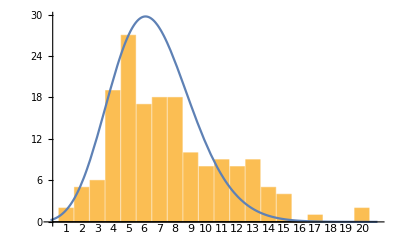

```mathematica
Show[FG,GM]
```

```mathematica
showerdistribution=BinCounts[Ns,{0,19,1}]
```

{7,26,29,26,20,11,7,12,2,3,10,5,5,1,2,1,0,0,1}

```mathematica
{7,26,29,26,20,11,7,12,2,3,10,5,5,1,2,1,0,0,1}
```

{7,26,29,26,20,11,7,12,2,3,10,5,5,1,2,1,0,0,1}

```mathematica
BinLists[Ns,{0,19,1}]
```

{{0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2},{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4},{5,5,5,5,5,5,5,5,5,5,5},{6,6,6,6,6,6,6},{7,7,7,7,7,7,7,7,7,7,7,7},{8,8},{9,9,9},{10,10,10,10,10,10,10,10,10,10},{11,11,11,11,11},{12,12,12,12,12},{13},{14,14},{15},{},{},{18}}

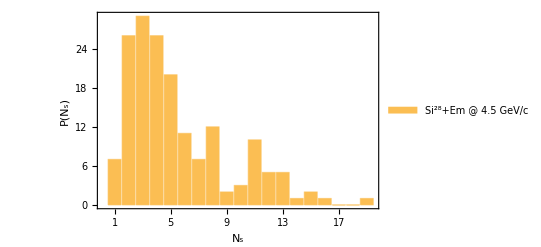

```mathematica
SM=BarChart[showerdistribution,Frame->{{True,False},{True,False}},FrameLabel->{"N_s","P(N_s)"} ,ChartLabels->Range[20],ChartLegends->Placed[{"Si^28+Em @ 4.5 GeV/c"},Right]]
```

```mathematica
Table[MultiplicityP12[[j,i]],{j,1,168},{i,1,2}]
```

{{1,2},{2,5},{3,3},{4,11},{5,10},{6,14},{7,4},{8,3},{9,7},{10,1},{11,6},{12,7},{13,6},{14,10},{15,3},{16,1},{17,1},{18,12},{19,0},{20,1},{21,0},{22,1},{23,2},{24,3},{25,1},{26,2},{27,4},{28,7},{29,3},{30,2},{31,3},{32,2},{33,5},{34,6},{35,12},{36,0},{37,14},{38,0},{39,6},{40,1},{41,2},{42,4},{43,3},{44,14},{45,0},{46,7},{47,1},{48,11},{49,7},{50,2},{51,2},{52,4},{53,2},{54,2},{55,2},{56,1},{57,1},{58,1},{59,2},{60,2},{61,3},{62,3},{63,7},{64,2},{65,9},{66,1},{67,4},{68,0},{69,1},{70,4},{71,1},{72,3},{73,7},{74,1},{75,4},{76,4},{77,6},{78,1},{79,2},{80,2},{81,12},{82,2},{83,1},{84,2},{85,1},{86,4},{87,7},{88,1},{89,3},{90,11},{91,1},{92,10},{93,2},{94,3},{95,3},{96,1},{97,3},{98,2},{99,6},{100,6},{101,3},{102,4},{103,3},{104,10},{105,4},{106,2},{107,1},{108,3},{109,9},{110,8},{111,2},{112,4},{113,1},{114,5},{115,3},{116,2},{117,3},{118,8},{119,6},{120,5},{121,12},{122,5},{123,3},{124,3},{125,7},{126,10},{127,11},{128,10},{129,3},{130,16},{131,8},{132,2},{133,7},{134,8},{135,4},{136,3},{137,4},{138,10},{139,5},{140,10},{141,3},{142,13},{143,5},{144,4},{145,6},{146,4},{147,5},{148,7},{149,1},{150,3},{151,2},{152,0},{153,3},{154,5},{155,8},{156,4},{157,9},{158,5},{159,2},{160,4},{161,11},{162,2},{163,12},{164,10},{165,3},{166,2},{167,4},{168,4}}

```mathematica
ShowerMul={{1,5},{2,6},{3,6},{4,5},{5,11},{6,6},{7,5},{8,5},{9,14},{10,8},{11,15},{12,10},{13,7},{14,6},{15,12},{16,13},{17,5},{18,6},{19,6},{20,5},{21,13},{22,6},{23,9},{24,10},{25,6},{26,7},{27,9},{28,12},{29,8},{30,9},{31,12},{32,7},{33,12},{34,15},{35,8},{36,8},{37,11},{38,5},{39,9},{40,6},{41,3},{42,9},{43,9},{44,11},{45,5},{46,18},{47,8},{48,16},{49,11},{50,6},{51,3},{52,6},{53,7},{54,8},{55,8},{56,7},{57,11},{58,9},{59,7},{60,5},{61,6},{62,9},{63,16},{64,2},{65,21},{66,5},{67,8},{68,5},{69,5},{70,7},{71,13},{72,2},{73,13},{74,4},{75,4},{76,9},{77,10},{78,4},{79,6},{80,3},{81,14},{82,12},{83,8},{84,5},{85,7},{86,4},{87,14},{88,8},{89,6},{90,9},{91,7},{92,8},{93,6},{94,5},{95,16},{96,6},{97,7},{98,9},{99,10},{100,12},{101,5},{102,8},{103,2},{104,8},{105,13},{106,7},{107,3},{108,7},{109,12},{110,10},{111,5},{112,3},{113,6},{114,6},{115,9},{116,5},{117,7},{118,9},{119,8},{120,10},{121,6},{122,8},{123,9},{124,7},{125,9},{126,6},{127,16},{128,6},{129,7},{130,14},{131,13},{132,5},{133,15},{134,18},{135,7},{136,6},{137,5},{138,21},{139,9},{140,11},{141,9},{142,11},{143,9},{144,10},{145,8},{146,10},{147,10},{148,14},{149,13},{150,6},{151,7},{152,4},{153,9},{154,13},{155,12},{156,11},{157,14},{158,15},{159,9},{160,6},{161,5},{162,4},{163,14},{164,13},{165,12},{166,8},{167,12},{168,7}}
```

{{1,5},{2,6},{3,6},{4,5},{5,11},{6,6},{7,5},{8,5},{9,14},{10,8},{11,15},{12,10},{13,7},{14,6},{15,12},{16,13},{17,5},{18,6},{19,6},{20,5},{21,13},{22,6},{23,9},{24,10},{25,6},{26,7},{27,9},{28,12},{29,8},{30,9},{31,12},{32,7},{33,12},{34,15},{35,8},{36,8},{37,11},{38,5},{39,9},{40,6},{41,3},{42,9},{43,9},{44,11},{45,5},{46,18},{47,8},{48,16},{49,11},{50,6},{51,3},{52,6},{53,7},{54,8},{55,8},{56,7},{57,11},{58,9},{59,7},{60,5},{61,6},{62,9},{63,16},{64,2},{65,21},{66,5},{67,8},{68,5},{69,5},{70,7},{71,13},{72,2},{73,13},{74,4},{75,4},{76,9},{77,10},{78,4},{79,6},{80,3},{81,14},{82,12},{83,8},{84,5},{85,7},{86,4},{87,14},{88,8},{89,6},{90,9},{91,7},{92,8},{93,6},{94,5},{95,16},{96,6},{97,7},{98,9},{99,10},{100,12},{101,5},{102,8},{103,2},{104,8},{105,13},{106,7},{107,3},{108,7},{109,12},{110,10},{111,5},{112,3},{113,6},{114,6},{115,9},{116,5},{117,7},{118,9},{119,8},{120,10},{121,6},{122,8},{123,9},{124,7},{125,9},{126,6},{127,16},{128,6},{129,7},{130,14},{131,13},{132,5},{133,15},{134,18},{135,7},{136,6},{137,5},{138,21},{139,9},{140,11},{141,9},{142,11},{143,9},{144,10},{145,8},{146,10},{147,10},{148,14},{149,13},{150,6},{151,7},{152,4},{153,9},{154,13},{155,12},{156,11},{157,14},{158,15},{159,9},{160,6},{161,5},{162,4},{163,14},{164,13},{165,12},{166,8},{167,12},{168,7}}

```mathematica
Mean [ShowerMul]//N
```

{84.5,8.60714}

```mathematica
StandardDeviation[ShowerMul]//N
```

{48.6415,3.72407}

```mathematica
f1=MixtureDistribution[{8.607142857142858,3.7240691708197997},{NormalDistribution[3,1.9],NormalDistribution[11.2,2.3]}];
```

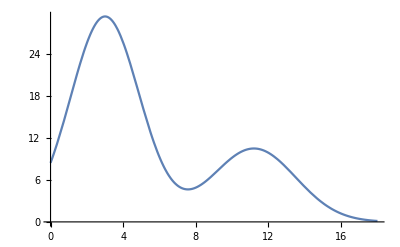

```mathematica
y=Plot[200*PDF[f1,x],{x,0,18}]
```

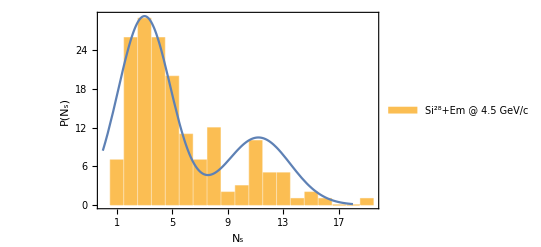

```mathematica
Show[SM,y]
```

```mathematica
FindFit[showerdistribution,{A ⅇ^(-(x-μ)^2/(2 σ))+A1 ⅇ^(-(x-μ1)^2/(2 σ1))+A2 ⅇ^(-(x-μ2)^2/(2 σ2))},{A,A1,A2,μ,σ,μ1,σ1,μ2,σ2},x]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{A→-0.941032,A1→7.0893,A2→27.3426,μ→-85.0412,σ→35.451,μ1→8.33886,σ1→16.184,μ2→3.19409,σ2→2.26053}

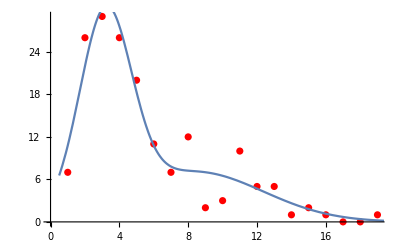

```mathematica
Show[ListPlot[showerdistribution,PlotStyle->Red],Plot[{A  ⅇ^(-(x-μ)^2/(2 σ))+A1 ⅇ^(-(x-μ1)^2/(2 σ1))+A2 ⅇ^(-(x-μ2)^2/(2 σ2))}/.{A->-0.9410323220068283,A1->7.089298155942087,A2->27.342587436385163,μ->-85.04116488810385,σ->35.45097501170598,μ1->8.338858579092513,σ1->16.184008941699563,μ2->3.194089346792598,σ2->2.260528123048613},{x,0.5,20}]]
```

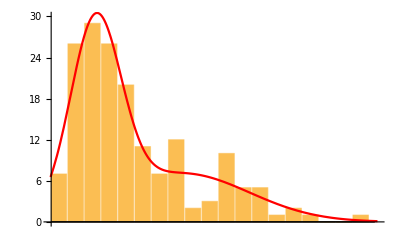

```mathematica
Show[BarChart[showerdistribution,PlotRange->{{0.5,20},{0,30}},FrameStyle->Directive[GrayLevel[0],AbsoluteThickness[2.]],FrameTicksStyle->Directive[Bold,Dashed,12]],Plot[{A  ⅇ^(-(x-μ)^2/(2 σ))+A1 ⅇ^(-(x-μ1)^2/(2 σ1))+A2 ⅇ^(-(x-μ2)^2/(2 σ2))}/.{A->-0.9410323220068283,A1->7.089298155942087,A2->27.342587436385163,μ->-85.04116488810385,σ->35.45097501170598,μ1->8.338858579092513,σ1->16.184008941699563,μ2->3.194089346792598,σ2->2.260528123048613},{x,0.5,20},PlotStyle->Red]]
```

```mathematica
blackdistribution=BinCounts[Nb,{0,9,1}]
```

{7,31,41,44,27,14,2,0,2}

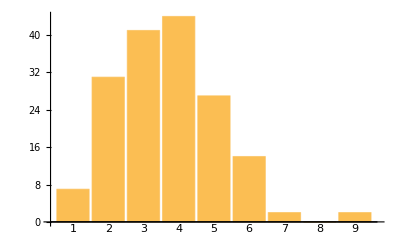

```mathematica
BM=BarChart[blackdistribution,ChartLabels->Range[10]]
```

```mathematica
Mean [Nb]//N
```

2.68452

```mathematica
StandardDeviation[Nb]//N
```

1.47287

```mathematica
PDF[NormalDistribution[2.6845238095238093,1.4728679138487881],b]
```

0.270861 ⅇ^(-0.230485 (-2.68452+b)^2)

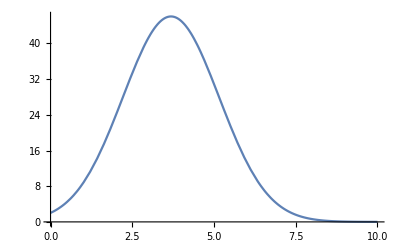

```mathematica
Z=Plot[170*PDF[NormalDistribution[3.6845238095238093,1.4728679138487881],x],{x,0,10}]
```

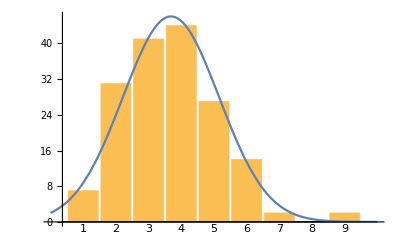

```mathematica
Show[BM,Z]
```

```mathematica
(*///////star_index  ## shower_multiplicity##Space_angles##pasudo_rapidity##transverse_momentum////////*)
```

```mathematica
d={{star_index=1,No_ofshower=2,spaceangle_S1=178.77892,spaceangle_S2=270.9107,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,pasudo_S1=-4.5416,pasudo_S2=0.015895,PT_S1=36.25464,PT_S2=84.37537},
{2,4,89.07474,89.32834,270.57248,90.29786,0.477864,0.208546,1.607566,-0.84931,112.8662,123.3088,48.54535,91.11471},
{3,2,180.7596,271.62649,-5.01632,0.028391,-125.123,125.0746},
{4,11,87.49887,274.06372,268.31745,267.2888,180.78075,180.94066,181.8309,177.59474,177.35547,91.81836,91.87356,0.043666824,0.070984833,-0.029370259,-0.047337036,-4.988858954,-4.802525206,-4.136481397,-3.863569267,-3.768703238,-0.031741698,-0.03270562,-56.5828,-85.4392,-120.785,-31.5908,-124.782,-120.407,-46.9084,125.4348,124.6866,-82.3385,-87.4751},
{5,10,4.5794,0.86966,295.6847,276.13935,274.06372,271.43157,270.3407,268.31745,267.2888,179.24304,3.21927362,4.881007895,0.464098185,0.107357506,0.070984833,0.02498821,0.005946372,-0.029370259,-0.047337036,-4.00475505,-87.4751,96.27782,46.14923,-39.7315,-85.4392,119.7536,20.53815,-120.785,-31.5908,115.4875},{6,14,90.6872,88.92534,87.49887,87.21061,86.52311,295.6847,276.13935,274.06372,277.57342,272.6425,270.61495,270.44468,268.31745,183.35198,-0.01199419,0.018757455,0.043666824,0.048703282,0.060720456,0.464098185,0.107357506,0.070984833,0.132567713,0.046136684,0.010733108,0.007761208,-0.029370259,-3.531537655,51.26124,103.272,-56.5828,-86.2531,-124.948,46.14923,-39.7315,-85.4392,113.0404,78.84137,53.43819,33.3302,-120.785,114.4671 },{7,4,92.74585,268.31745,182.69498,177.59474,-0.047942479,-0.029370259,-3.749798971,-3.863569267,-125.701,-120.785,58.47524,125.4348},{8,3,177.35547,0.86966,268.31745,-3.768703238,4.881007895,-0.029370259,124.6866,96.27782,-120.785},{9,7,179.24304,88.11291,87.21061,81.3107,4.5794,267.2888,183.35198,-4.00475505,0.03294189,0.048703282,0.152241607,3.21927362,-0.047337036,-3.531537655,115.4875,18.61934,-86.2531,-45.6468,-87.4751,-31.5908,114.4671},{10,1,100.01633,-0.175715246,-62.0194}, {11,6,182.26596,105.75503,88.92534,86.52311,0.86966,268.31745,-3.743796186,-0.278509408,0.018757455,0.060720456,4.881007895,-0.029370259,123.2007,-109.863,103.272,-124.948,96.27782,-120.785},{12,7,177.59474,177.35547,92.74585,91.22108,87.21061,183.35198,182.69498,-3.863569267,-3.768703238,-0.047942479,-0.02131348,0.048703282,-3.531537655,-3.749798971,125.4348,124.6866,-125.701,-14.4447,-86.2531,114.4671,58.47524},{13,6,179.24304,181.05416,180.78075,183.35198,267.2888,268.31745,-4.00475505,-4.688601695,-4.988858954,-3.531537655,-0.047337036,-0.029370259,115.4875,-115.427,-124.782,114.4671,-31.5908,-120.785},{14,11,88.51959,87.49887,87.21061,86.52311,81.3107,4.5794,277.57342,275.6847,274.03451,274.06372,267.2888,0.025840904,0.043666824,0.048703282,0.060720456,0.152241607,3.21927362,0.132567713,0.464098185,0.070473775,0.070984833,-0.047337036,66.3944,-56.5828,-86.2531,-124.948,-45.6468,-87.4751,113.0404,46.14923,-82.6981,-85.4392,-31.5908},{15,2,86.52311,179.24304,0.060720456,-4.00475505,-124.948,115.4875},{16,1,272.6425,0.046136684,78.84137  },{17,2,270.89529,180.34045,0.015626391,-5.81885821,82.92338,-120.33},{18,12,88.11291,87.21061,81.3107,4.5794,358.11616,357.56981,277.57342,276.13935,271.43157,270.9107,270.3407,183.35198,0.03294189,0.048703282,0.152241607,3.21927362,4.107971806,3.853254768,0.132567713,0.107357506,0.02498821,0.015895383,0.005946372,-3.531537655,18.61934,-86.2531,-45.6468,-87.4751,119.8765,82.265,113.0404,-39.7315,119.7536,84.37537,20.53815,114.4671},{19,0,,},{20,1,358.11616,4.107971806 ,119.8765 },{21,0, ,},{22,1,275.6847,0.464098185 ,46.14923 },{23,2,179.24304,267.2888,-4.00475505,-0.047337036,115.4875,-31.5908},{24,3,105.75503,268.31745,183.35198,-0.278509408,-0.029370259,-3.531537655,-109.863,-120.785,114.4671},{25,1,86.52311,0.060720456 ,-124.948 },{26,2,177.59474,177.35547,-3.863569267,-3.768703238,125.4348,124.6866},{27,4,177.59474,177.35547,357.56981,267.2888,-3.863569267,-3.768703238,3.853254768,-0.047337036,125.4348,124.6866,82.265,-31.5908},{28,7,91.91904,92.26596,358.11616,277.57342,267.2888,183.35198,180.34045,-0.033499831,-0.039558776,4.107971806,0.132567713,-0.047337036,-3.531537655,-5.81885821,-91.5077,-115.506,119.8765,113.0404,-31.5908,114.4671,-120.33},{29,3,92.26596,87.21061,358.11616,-0.039558776,0.048703282,4.107971806,-115.506,-86.2531,119.8765},{30,2,4.5794,277.57342,3.21927362,0.132567713,-87.4751,113.0404},{31,3,91.81836,276.13935,179.24304,-0.031741698,0.107357506,-4.00475505,-82.3385,-39.7315,115.4875},{32,2,180.34045,355.9033,-5.81885821,3.330766215,-120.33,-98.9595},{33,5,179.24304,4.5794,357.56981,276.13935,271.43157,-4.00475505,3.21927362,3.853254768,0.107357506,0.02498821,115.4875,-87.4751,82.265,-39.7315,119.7536},{34,6,180.34045,87.21061,86.52311,357.56981,277.57342,183.35198,-5.81885821,0.048703282,0.060720456,3.853254768,0.132567713,-3.531537655,-120.33,-86.2531,-124.948,82.265,113.0404,114.4671},{35,12,177.59474,90.6872,86.52311,84.15581,83.88923,5.73129,4.5794,277.57342,276.13935,275.6847,274.03451,272.6425,-3.863569267,-0.01199419,0.060720456,0.102177689,0.106855827,2.994599191,3.21927362,0.132567713,0.107357506,0.464098185,0.070473775,0.046136684,125.4348,51.26124,-124.948,77.96657,101.2875,-66.0621,-87.4751,113.0404,-39.7315,46.14923,-82.6981,78.84137},{36,0, ,},{37,14,88.11291,87.21061,86.52311,84.15581,4.5794,0.86966,358.11616,357.56981,277.57342,275.6847,274.03451,272.6425,271.43157,267.2888,0.03294189,0.048703282,0.060720456,0.102177689,3.21927362,4.881007895,4.107971806,3.853254768,0.132567713,0.464098185,0.070473775,0.046136684,0.02498821,-0.047337036,18.61934,-86.2531,-124.948,77.96657,-87.4751,96.27782,119.8765,82.265,113.0404,46.14923,-82.6981,78.84137,119.7536,-31.5908},{38,0, ,},{39,6,83.88923,81.3107,357.56981,355.9033,277.57342,274.06372,0.106855827,0.152241607,3.853254768,3.330766215,0.132567713,0.070984833,101.2875,-45.6468,82.265,-98.9595,113.0404,-85.4392},{40,1,182.69498,-3.749798971 ,58.47524},{41,2,276.13935,274.06372,0.107357506,0.070984833,-39.7315,-85.4392},{42,4,8.6893,5.73129,276.13935,275.6847,2.577362535,2.994599191,0.107357506,0.464098185,84.53865,-66.0621,-39.7315,46.14923},{43,3,183.35198,177.35547,105.75503,-3.531537655,-3.768703238,-0.278509408,114.4671,124.6866,-109.863},{44,14,177.59474,105.75503,0.86966,277.57342,276.13935,271.43157,270.9107,268.31745,267.29027,267.2888,267.056,266.37494,183.35198,182.69498,-3.863569267,-0.278509408,4.881007895,0.132567713,0.107357506,0.02498821,0.015895383,-0.029370259,-0.04731135,-0.047337036,-0.051405118,-0.063311486,-3.531537655,-3.749798971,125.4348,-109.863,96.27782,113.0404,-39.7315,119.7536,84.37537,-120.785,-31.7701,-31.5908,-121.535,-73.4891,114.4671,58.47524},{45,0, ,},{46,7,91.91904,268.31745,267.2888,182.26596,181.05416,180.78075,177.35547,-0.033499831,-0.029370259,-0.047337036,-3.743796186,-4.688601695,-4.988858954,-3.768703238,-91.5077,-120.785,-31.5908,123.2007,-115.427,-124.782,124.6866},{47,1,267.2888,-0.047337036 ,-31.5908},{48,10,91.81836,92.26596,92.74585,177.35547,179.24304,180.91597,182.26596,182.69498,267.2888,270.3407,-0.031741698,-0.039558776,-0.047942479,-3.768703238,-4.00475505,-4.829124513,-3.743796186,-3.749798971,-0.047337036,0.005946372,-82.3385,-115.506,-125.701,124.6866,115.4875,-121.286,123.2007,58.47524,-31.5908,20.53815},{49,8,270.9107,267.2888,183.35198,180.78075,180.91597,179.24304,177.59474,177.35547,0.015895383,-0.047337036,-3.531537655,-4.988858954,-4.829124513,-4.00475505,-3.863569267,-3.768703238,84.37537,-31.5908,114.4671,-124.782,-121.286,115.4875,125.4348,124.6866},{50,2,272.6425,91.87356,0.046136684,-0.03270562,78.84137,-87.4751},{51,2,8.5781,183.69851,2.587964,-3.52487213,84.54,114.3851},{52,4,268.321,183.4521,182.7124,180.93,-0.028931,-3.5332,-3.7569,-4.81,-120.821,114.561,53.90,-120.41},{53,2,97.75318,182.26596,-0.135733391,-3.743796186,-44.835,123.2007},{54,2,92.74585,182.26596,-0.047942479,-3.743796186,-125.701,123.2007},{55,2,91.87356,96.93833,-0.03270562,-0.121393761,-87.4751,54.92388},{56,1,181.05416,-4.688601695,-115.427 },{57,1,268.31745,-0.029370259,-120.785 },{58,1,8.6893,2.577362535 ,84.53865 },{59,2,276.13935,277.57342,0.107357506,0.132567713,-39.7315,113.0404},{60,2,90.6872,7.86313,-0.01199419,2.677618162,51.26124,125.9947},{61,3,88.43675,268.30544,178.85567,0.027287245,-0.029579964,-4.606521591,57.30571,-120.345,26.89547},{62,3,84.56732,179.57048,357.56981,0.09496055,-5.586456435,3.853254768,31.86602,-60.3743,82.265},{63,7,272.63473,270.9107,268.04862,183.63263,181.8309,180.91597,178.8674,0.046000928,0.015895383,-0.034064592,-3.451082186,-4.136481397,-4.829124513,-4.616825707,79.60266,84.37537,-106.918,124.575,-46.9084,-121.286,25.44974},{64,2,269.21303,182.08863,-0.01373565,-4.00475505,-103.502,-15.552},{65,9,183.63263,183.4972,179.24304,177.59474,97.75318,90.47658,8.6893,6.97579,357.56981,-3.451082186,-3.489100964,-4.00475505,-3.863569267,-0.135733391,-0.008317986,2.577362535,2.797692228,3.853254768,124.575,120.8829,115.4875,125.4348,-44.835,74.19222,84.53865,80.45653,82.265},{66,1,105.75503,-0.278509408 ,-109.863},{67,4,91.22108,90.6872,83.88923,267.056,-0.02131348,-0.01199419,0.106855827,-0.051405118,-14.4447,51.26124,101.2875,-121.535},{68,0,,},{69,1,91.87356,-0.03270562,-87.4751 },{70,4,266.37494,355.9033,180.91597,179.24304,-0.063311486,3.330766215,-4.829124513,-4.00475505,-73.4891,-98.9595,-121.286,115.4875},{71,2,86.52311,276.13935,0.060720456,0.107357506,-124.948,-39.7315},{72,3,183.4972,96.93833,4.5794,-3.489100964,-0.121393761,3.21927362,120.8829,54.92388,-87.4751},{73,7,97.27094,88.72881,84.15581,357.56981,269.34114,180.34045,178.8674,-0.127243827,0.022188271,0.102177689,3.853254768,-0.01149953,-5.81885821,-4.616825707,14.88761,87.18835,77.96657,82.265,-93.4734,-120.33,25.44974},{74,1,87.21061,0.048703282 ,-86.2531 },{75,4,92.74585,86.52311,84.15581,81.3107,-0.047942479,0.060720456,0.102177689,0.152241607,-125.701,-124.948,77.96657,-45.6468},{76,4,266.37494,91.91904,87.65032,8.6893,-0.063311486,-0.033499831,0.04102115,2.577362535,-73.4891,-91.5077,-38.9499,84.53865},{77,6,88.72881,8.14689,352.84173,277.57342,276.13935,270.44468,0.02218826,2.642051062,2.771803891,0.132567713,0.107357506,0.00776115,87.18853,120.6334,104.8774,113.0404,-39.7315,33.3302},{78,1,85.5396, 0.077927418 ,-82.7598},{79,2,1.67177,182.26596,4.227420251,-3.743796186,125.3582,123.2007},{80,2,6.97579,272.6425,2.797692228,0.046136684,80.45653,78.84137},{81,12,85.489,84.52007,83.77783,7.208484,1.23324,358.07302,355.04313,352.84173,353.75093,276.34381,277.24787,272.6425,0.078813268,0.095788972,0.10881144,2.76479521,4.531690685,4.085325869,3.139975662,2.771803891,2.907949506,0.110947288,0.126837926,0.046136684,-77.8484,37.58827,108.9913,100.6489,118.8894,118.0915,-122.253,104.8774,119.5339,115.8572,110.5709,78.84137},{82,2,85.16519,354.10784,0.084483674,2.96686965,-42.2792,-48.0232},{83,1,276.13935,0.107357506,-39.7315  },{84,2,101.38799,83.77783,-0.200079641,0.10881144,95.24318,108.9913},{85,1,1.23324,4.531690685 ,118.8894 },{86,4,85.16519,354.10784,353.75093,274.5172,0.084483674,2.96686965,2.907949506,0.078921815,-42.2792,-48.0232,119.5339,-77.2327},{87,7,97.75318,88.40039,86.97966,7.86313,8.6893,358.07302,267.29027,-0.135733391,0.027922035,0.052739356,2.677618162,2.577362535,4.085325869,-0.04731135,-44.835,53.18897,-104.988,125.9947,84.53865,118.0915,-31.7701},{88,1,7.86313,2.677618162 ,125.9947 },{89,3,357.71232,352.84173,277.24787,3.913703079,2.771803891,0.126837926,94.98597,104.8774,110.5709},{90,11,177.99973,88.29464,87.21061,86.52311,85.5396,7.208484,6.81512,1.23324,357.11013,352.84173,275.35383,-4.0479904,0.02976852,0.048703282,0.060720456,0.077927418,2.76479521,2.82105048,4.531690685,3.679950599,2.771803891,0.093578239,110.5908,40.83502,-86.2531,-124.948,-82.7598,100.6489,63.90741,118.8894,31.38316,104.8774,22.16485},{91,1,266.37494,-0.063311486,-73.4891},{92,10,177.35547,104.94372,90.6872,84.52007,8.6893,6.97579,7.86313,356.84633,355.04313,275.35383,-3.768703238,-0.263825459,-0.01199419,0.095788972,2.577362535,2.797692228,2.677618162,3.592554779,3.139975662,0.093578239,124.6866,-120.386,51.26124,37.58827,84.53865,80.45653,125.9947,-121.246,-122.253,22.16485},{93,2,179.59003,270.3407,-5.633041172,0.005946372,-62.5247,20.53815},{94,3,85.16519,83.77783,358.07302,0.084483674,0.10881144,4.085325869,-42.2792,108.9913,118.0915},{95,3,88.40039,86.97966,270.9107,0.027922035,0.052739356,0.015895383,53.18897,-104.988,84.37537},{96,1,101.22489,-0.197176669 ,80.58449},{97,3,177.73986,84.52007,276.34381,-3.925817704,0.095788972,0.110947288,122.3923,37.58827,115.8572},{98,2,88.11291,271.43157,0.03294189,0.02498821,18.61934,119.7536},{99,6,178.52384,85.489,6.81512,4.5393,354.10784,353.75093,-4.351874707,0.078813268,2.82105048,3.228078079,2.96686965,2.907949506,65.52972,-77.8484,63.90741,-124.117,-48.0232,119.5339},{100,6,187.4282,99.9334,7.208484,6.81512,4.5393,352.84173,-2.734688517,-0.174245629,2.76479521,2.82105048,3.228078079,2.771803891,-110.367,-70.8915,100.6489,63.90741,-124.117,104.8774},{101,3,101.38799,104.94372,7.208484,-0.200079641,-0.263825459,2.76479521,95.24318,-120.386,100.6489},{102,4,268.04862,5.73129,6.97579,276.34381,-0.034064592,2.994599191,2.797692228,0.110947288,-106.918,-66.0621,80.45653,115.8572},{103,3,187.4282,1.23324,271.43157,-2.734688517,4.531690685,0.02498821,-110.367,118.8894,119.7536},{104,10,267.29027,97.75183,92.74585,83.77783,7.208484,6.81512,4.71331,5.65814,275.8342223,275.35383,-0.04731135,-0.135709612,-0.047942479,0.10881144,2.76479521,2.82105048,3.190419571,3.007465784,0.102002812,0.093578239,-31.7701,-44.6762,-125.701,108.9913,100.6489,63.90741,-126,-73.7269,76.9761,22.16485},{105,4,183.63263,87.59192,5.11548,272.6425,-3.451082186,0.042041361,3.108438327,0.046136684,124.575,-45.8779,-115.901,78.84137},{106,2,6.97579,277.37313,2.797692228,0.129042042,80.45653,102.1566},{107,1,270.61495,0.010733108,53.43819  },{108,3,275.8342223,275.35383,8.14689,0.102002812,0.093578239,2.642051062,76.9761,22.16485,120.6334},{109,9,268.04862,180.78075,91.87356,85.16519,8.6893,7.86313,6.54714,4.5393,352.84173,-0.034064592,-4.988858954,-0.03270562,0.084483674,2.577362535,2.677618162,2.861256883,3.228078079,2.771803891,-106.918,-124.782,-87.4751,-42.2792,84.53865,125.9947,32.87344,-124.117,104.8774},{110,8,101.38799,92.74585,90.6872,90.47658,84.52007,8.6893,5.11548,265.60219,-0.200079641,-0.047942479,-0.01199419,-0.008317986,0.095788972,2.577362535,3.108438327,-0.076831744,95.24318,-125.701,51.26124,74.19222,37.58827,84.53865,-115.901,124.8089},{111,2,6.81512,267.29027,2.82105048,-0.04731135,63.90741,-31.7701},{112,4,266.37494,178.36733,104.94372,84.59554,-0.063311486,-4.251089765,-0.263825459,0.094465807,-73.4891,81.50354,-120.386,28.41367},{113,1,178.52384,-4.351874707,65.52972 },{114,5,269.34114,268.31745,177.35547,85.16519,83.77783,-0.01149953,-0.029370259,-3.768703238,0.084483674,0.10881144,-93.4734,-120.785,124.6866,-42.2792,108.9913},{115,3,266.37494,1.23324,4.71331,-0.063311486,4.531690685,3.190419571,-73.4891,118.8894,-126},{116,2,186.80413,86.97966,-2.822668178,0.052739356,-125.084,-104.988},{117,3,178.52384,91.87356,1.23324,-4.351874707,-0.03270562,4.531690685,65.52972,-87.4751,118.8894},{118,8,183.63263,104.94372,86.52311,85.5396,7.86313,8.6893,275.35383,271.43157,-3.451082186,-0.263825459,0.060720456,0.077927418,2.677618162,2.577362535,0.093578239,0.02498821,124.575,-120.386,-124.948,-82.7598,125.9947,84.53865,22.16485,119.7536},{119,6,272.6425,178.8674,178.36733,96.19346,96.4651,4.5393,0.046136684,-4.616825707,-4.251089765,-0.1083074,-0.113077492,3.228078079,78.84137,25.44974,81.50354,117.2493,100.571,-124.117},{120,5,179.03963,84.52007,84.59554,5.65814,5.91513,-4.781787385,0.095788972,0.094465807,3.007465784,2.962971936,3.924423,37.58827,28.41367,-73.7269,-45.335},{121,12,270.61495,270.3407,267.2888,178.52384,177.99973,97.57647,90.47658,84.59554,6.97579,6.54714,7.86313,8.6893,0.010733108,0.005946372,-0.047337036,-4.351874707,-4.0479904,-0.132621414,-0.008317986,0.094465807,2.797692228,2.861256883,2.677618162,2.577362535,53.43819,20.53815,-31.5908,65.52972,110.5908,-23.437,74.19222,28.41367,80.45653,32.87344,125.9947,84.53865},{122,5,277.37313,187.4282,96.19346,92.26596,1.23324,0.129042042,-2.734688517,-0.1083074,-0.039558776,4.531690685,102.1566,-110.367,117.2493,-115.506,118.8894},{123,3,6.97579,274.5172,180.78075,2.797692228,0.078921815,-4.988858954,80.45653,-77.2327,-124.782},{124,3,96.19346,276.34381,272.6425,-0.1083074,0.110947288,0.046136684,117.2493,115.8572,78.84137},{125,7,187.4282,178.52384,96.93833,89.15531,87.59192,5.11548,5.73,-2.734688517,-4.351874707,-0.121393761,0.01474315,0.042041361,3.108438327,2.994824672,-110.367,65.52972,54.92388,117.008,-45.8779,-115.901,-66.2004},{126,10,268.04862,267.29027,92.74585,88.40039,85.16519,83.77783,5.91513,5.19835,353.75093,276.13935,-0.034064592,-0.04731135,-0.047942479,0.027922035,0.084483674,0.10881144,2.962971936,3.092346579,2.907949506,0.107357506,-106.918,-31.7701,-125.701,53.18897,-42.2792,108.9913,-45.335,-111.413,119.5339,-39.7315},{127,11,270.89529,185.46019,184.31306,183.35198,178.70364,178.52384,104.94372,97.75318,90.6872,5.19835,4.5794,0.015626391,-3.043133343,-3.27925414,-3.531537655,-4.481771147,-4.351874707,-0.263825459,-0.135733391,-0.01199419,3.092346579,3.21927362,82.92338,-13.359,108.7207,114.4671,45.22753,65.52972,-120.386,-44.835,51.26124,-111.413,-87.4751},{128,10,182.65441,178.8674,178.36733,88.29464,8.6893,6.97579,6.54714,7.86313,358.07302,270.44468,-3.764972857,-4.616825707,-4.251089765,0.02976852,2.577362535,2.797692228,2.861256883,2.677618162,4.085325869,0.007761208,53.90037,25.44974,81.50354,40.83502,84.53865,80.45653,32.87344,125.9947,118.0915,33.3302},{129,3,98.36445,8.6893,6.81512,-0.146508526,2.577362535,2.82105048,-104.296,84.53865,63.90741},{130,16,271.4256,271,269.34114,268.31745,268.04862,267.29027,187.4282,187.02998,179.1358,104.94372,97.75183,92.26596,6.78555,5.94518,352.84173,352.11214,0.025322,0.0165383,-0.01149953,-0.029370259,-0.034064592,-0.04731135,-2.734688517,-2.78993465,-4.81,-0.263825459,-0.135709612,-0.039558776,2.825409028,2.957895545,2.771803891,2.674468129,119.748,84.381,-93.4734,-120.785,-106.918,-31.7701,-110.367,-125.303,31.925,-120.386,-44.6762,-115.506,60.66893,-41.7823,104.8774,31.63205},{131,8,277.37313,270.3407,97.75318,97.27094,87.21061,86.52311,85.5396,8.198933,0.129042042,0.005946372,-0.135733391,-0.127243827,0.048703282,0.060720456,0.077927418,2.635661652,102.1566,20.53815,-44.835,14.88761,-86.2531,-124.948,-82.7598,118.5776},{132,2,5.94518,6.2815,2.957895545,2.902763024,-41.7823,60.66893},{133,7,178.70364,92.26596,91.81836,90.6872,90.47658,6.64432,352.508,-4.481771147,-0.039558776,-0.031741698,-0.01199419,-0.008317986,2.846490249,2.726112089,45.22753,-115.506,-82.3385,51.26124,74.19222,44.52033,76.21565},{134,8,187.02998,178.70364,178.52384,97.1423,87.65032,88.29464,4.0,353.42708,-2.7891,-4.481772,-4.3519,-0.124980757,0.04102115,0.02976852,3.354661002,2.857318419,-125.303,45.22753,65.52972,30.81534,-38.9499,40.83502,-95.3612,125.9997},{135,4,178.70364,91.925,7.86313,8.7521,-4.4789,-0.033499831,2.677618162,2.577362535,45.22753,-91.5077,125.9947,84.53865},{136,3,186.75058,92.26596,6.97579,-2.830587988,-0.039558776,2.797692228,-124.093,-115.506,80.45653},{137,4,269.34114,178.52384,91.87356,8.198933,-0.01149953,-4.351874707,-0.03270562,2.635661652,-93.4734,65.52972,-87.4751,118.5776},{138,10,179.11425,90.47658,89.15531,7.932,7.23062,6.81512,358.11616,357.56981,353.75093,352.84173,-4.862674765,-0.008317986,0.01474315,2.678,2.7620,2.82105048,4.107971806,3.853254768,2.908,2.771803891,-5.47534,74.19222,117.008,125.6116,102.302,63.90741,119.8765,82.265,119.5339,104.8774},{139,5,187.431,88.4,7.86313,8.6893,5.73,-2.7347,0.02710,2.677618162,2.57737, 2.99481,-110.37,53.1891,125.9947,84.53865,-66.2004},{140,10,186.751,178.71,96.194,86.9797,87.4989,6.64432,8.1981,3.963,358.11616,357.56981,-2.830574,-4.4827,-0.10831,0.052739356,0.043667,2.8465,2.635662,3.3640726,4.107971806,3.853254768,-124.093,45.22753,117.2493,-104.988,-56.5828,44.52033,118.5776,-92.2118,119.8765,82.265},{141,3,187.4282,178.70364,4.00005,-2.7347,-4.481771147,3.3547,-110.367,45.228,-95.3612},{142,11,2.7841,3.47689,0.86966,1.23324,357.110,356.984,353.75093,352.84173,271.43157,268.31745,268.04862,3.71536,3.494912,4.8812,4.531691,3.67910,3.63715,2.90795,2.771804,0.02499,-0.0293,-0.0340662,43.46573,-41.4603,96.27782,118.8894,,31.38316,-115.403,119.5339,104.8774,119.7536,-120.785,-106.918},{143,6,178.7042,92.74585,84.59554,5.51299,6.64432,265.60219,-4.481771147,-0.047942479,0.094465807,3.033495082,2.846490249,-0.076831744,45.22753,-125.701,28.41367,-87.7307,44.52033,124.8089},{144,4,8.1479,7.863,357.11013,352.84173,2.642062,2.67762,3.679951,2.771803891,120.6334,125.9947,31.38316,104.8774},{145,6,187.4282,88.40039,85.78183,7.86313,8.6893,270.8953,-2.7347,0.027922035,0.07368755,2.677618162,2.577362535,0.015626391,-110.367,53.18897,-103.133,125.9947,84.53865,82.92338},{146,4,86.97966,1.24,358.1162,181.8309,0.052739356,4.521,4.107971806,-4.136481397,0.052734,4.521,4.1080,-4.1365},{147,5,8.6893,6.97579,353.42708,357.11013,356.98382,2.577362535,2.79769,2.858,3.679951,3.6372,84.557,80.45653,125.9997,31.38316,-115.403},{148,7,268.049,187.4312,92.266,86.523,84.596,5.73,357.5723,-0.034064592,-2.748521,-0.039558776,0.060720456,0.0945,2.995,3.853254768,-106.918,-110.37,-115.506,-124.948,28.41367,-66.2004,82.265},{149,1,3.96261, 3.364072536 ,-92.2118},{150,3,7.23062,6.81512,352.84173,2.761720961,2.82105048,2.771803891,102.302,63.90741,104.8774},{151,2,85.489,7.86313,0.07881,2.677618162,-77.848,125.9947},{152,0,0,0},{153,3,178.70364,87.21061,8.198933,-4.481771147,0.048703282,2.635661652,45.22753,-86.2531,118.5776},{154,5,267.29027,7.93252,7.23062,357.56981,267.056,-0.047312,2.6689,2.761721,3.853254768,-0.051405118,-31.7701,125.6116,102.302,82.265,-121.535},{155,8,274.5172,100.20223,101.22489,85.95225,84.67756,3.96261,3.04775,358.07302,0.0852,-0.179010982,-0.197176669,0.070705404,0.093027993,3.364072536,3.6267347,4.08533,-77.2327,-40.6786,80.58449,-113.915,18.26111,-92.2118,11.80683,118.0915},{156,4,190.01633,87.499,8.199,272.73226,-2.43461,0.04367,2.63567,0.047705017,41.74209,-56.5828,118.5776,69.71372},{157,9,86.97966,87.49887,7.93252,3.04775,1.137,357.11013,356.98382,277.57342,276.13935,0.052739356,0.043666824,2.668804257,3.6267347,4.612948,3.6799506,3.637152,0.132568,0.107357506,-104.988,-56.5828,125.6116,11.80683,114.3210,31.38316,-115.403,113.0404,-39.7315},{158,5,7.93252,7.23062,3.96261,357.71512,352.508,2.678,2.761720961,3.364072536,3.914928101,2.726112089,125.6116,102.302,-92.2118,-52.118,76.21565},{159,2,266.37494,180.34045,-0.063311486,-5.81885821,-73.4891,-120.33},{160,4,181.8309,100.20223,5.73129,270.3407,-4.136481397,-0.179010982,2.994599191,0.005946372,-46.9084,-40.6786,-66.0621,20.53815},{161,11,352.84173,268.04862,267.29027,265.60219,187.4282,178.70364,178.52384,99.18809,99.9334,84.52,84.59554,2.771803891,-0.034064592,-0.04731135,-0.076831744,-2.734688517,-4.481771147,-4.351874707,-0.161054191,-0.174245629,0.095788972,0.094465807,104.8774,-106.918,-31.7701,124.8089,-110.367,45.22753,65.52972,-122.741,-70.8915,37.58827,28.41367},{162,2,96.34505,97.57647,-0.129258,-0.132621414,108.9376,-23.437},{163,12,267.056,266.37494,177.73986,177.59474,177.35547,91.59267,88.40039,86.97966,83.77783,5.73,8.14689,353.42708,-0.051405118,-0.063311486,-3.925817704,-3.863569267,-3.768703238,-0.027800916,0.027922035,0.052739356,0.10881144,2.994824672,2.642051062,2.857318419,-121.535,-73.4891,122.3923,125.4348,124.6866,-58.9075,53.18897,-104.988,108.9913,-66.2004,120.6334,125.9997},{164,10,186.80413,186.75058,185.46019,185.26531,179.11425,177.35547,99.9334,90.6872,85.489,270.9107,-2.822668178,-2.830587988,-3.043133343,-3.079530021,-4.862674765,-3.768703238,-0.174245629,-0.01199419,0.078813268,0.015895383,-125.084,-124.093,-13.359,11.1561,-5.47534,124.6866,-70.8915,51.26124,-77.8484,84.37537},{165,3,274.5172,6.81512,91.22108,0.078921815,2.82105048,-0.02131348,-77.2327,63.90741,-14.4447},{166,2,178.8674,353.42708,-4.616825707,2.857318419,25.44974,125.9997},{167,4,96.97904,178.02096,182.26596,190.01633,-0.122109558,-4.058662838,-3.923245283,-2.434606059,50.26317,109.2841,122.5645,41.74209},{168,4,272.73226,178.36733,99.9334,90.6872,0.047705017,-4.251089765,-0.174245629,-0.01199419,69.71372,81.50354,-70.8915,51.26124}}
```

{{1,2,178.779,270.911,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4.5416,0.015895,36.2546,84.3754},{2,4,89.0747,89.3283,270.572,90.2979,0.477864,0.208546,1.60757,-0.84931,112.866,123.309,48.5454,91.1147},{3,2,180.76,271.626,-5.01632,0.028391,-125.123,125.075},{4,11,87.4989,274.064,268.317,267.289,180.781,180.941,181.831,177.595,177.355,91.8184,91.8736,0.0436668,0.0709848,-0.0293703,-0.047337,-4.98886,-4.80253,-4.13648,-3.86357,-3.7687,-0.0317417,-0.0327056,-56.5828,-85.4392,-120.785,-31.5908,-124.782,-120.407,-46.9084,125.435,124.687,-82.3385,-87.4751},{5,10,4.5794,0.86966,295.685,276.139,274.064,271.432,270.341,268.317,267.289,179.243,3.21927,4.88101,0.464098,0.107358,0.0709848,0.0249882,0.00594637,-0.0293703,-0.047337,-4.00476,-87.4751,96.2778,46.1492,-39.7315,-85.4392,119.754,20.5382,-120.785,-31.5908,115.488},{6,14,90.6872,88.9253,87.4989,87.2106,86.5231,295.685,276.139,274.064,277.573,272.643,270.615,270.445,268.317,183.352,-0.0119942,0.0187575,0.0436668,0.0487033,0.0607205,0.464098,0.107358,0.0709848,0.132568,0.0461367,0.0107331,0.00776121,-0.0293703,-3.53154,51.2612,103.272,-56.5828,-86.2531,-124.948,46.1492,-39.7315,-85.4392,113.04,78.8414,53.4382,33.3302,-120.785,114.467},{7,4,92.7459,268.317,182.695,177.595,-0.0479425,-0.0293703,-3.7498,-3.86357,-125.701,-120.785,58.4752,125.435},{8,3,177.355,0.86966,268.317,-3.7687,4.88101,-0.0293703,124.687,96.2778,-120.785},{9,7,179.243,88.1129,87.2106,81.3107,4.5794,267.289,183.352,-4.00476,0.0329419,0.0487033,0.152242,3.21927,-0.047337,-3.53154,115.488,18.6193,-86.2531,-45.6468,-87.4751,-31.5908,114.467},{10,1,100.016,-0.175715,-62.0194},{11,6,182.266,105.755,88.9253,86.5231,0.86966,268.317,-3.7438,-0.278509,0.0187575,0.0607205,4.88101,-0.0293703,123.201,-109.863,103.272,-124.948,96.2778,-120.785},{12,7,177.595,177.355,92.7459,91.2211,87.2106,183.352,182.695,-3.86357,-3.7687,-0.0479425,-0.0213135,0.0487033,-3.53154,-3.7498,125.435,124.687,-125.701,-14.4447,-86.2531,114.467,58.4752},{13,6,179.243,181.054,180.781,183.352,267.289,268.317,-4.00476,-4.6886,-4.98886,-3.53154,-0.047337,-0.0293703,115.488,-115.427,-124.782,114.467,-31.5908,-120.785},{14,11,88.5196,87.4989,87.2106,86.5231,81.3107,4.5794,277.573,275.685,274.035,274.064,267.289,0.0258409,0.0436668,0.0487033,0.0607205,0.152242,3.21927,0.132568,0.464098,0.0704738,0.0709848,-0.047337,66.3944,-56.5828,-86.2531,-124.948,-45.6468,-87.4751,113.04,46.1492,-82.6981,-85.4392,-31.5908},{15,2,86.5231,179.243,0.0607205,-4.00476,-124.948,115.488},{16,1,272.643,0.0461367,78.8414},{17,2,270.895,180.34,0.0156264,-5.81886,82.9234,-120.33},{18,12,88.1129,87.2106,81.3107,4.5794,358.116,357.57,277.573,276.139,271.432,270.911,270.341,183.352,0.0329419,0.0487033,0.152242,3.21927,4.10797,3.85325,0.132568,0.107358,0.0249882,0.0158954,0.00594637,-3.53154,18.6193,-86.2531,-45.6468,-87.4751,119.877,82.265,113.04,-39.7315,119.754,84.3754,20.5382,114.467},{19,0,Null,Null},{20,1,358.116,4.10797,119.877},{21,0,Null,Null},{22,1,275.685,0.464098,46.1492},{23,2,179.243,267.289,-4.00476,-0.047337,115.488,-31.5908},{24,3,105.755,268.317,183.352,-0.278509,-0.0293703,-3.53154,-109.863,-120.785,114.467},{25,1,86.5231,0.0607205,-124.948},{26,2,177.595,177.355,-3.86357,-3.7687,125.435,124.687},{27,4,177.595,177.355,357.57,267.289,-3.86357,-3.7687,3.85325,-0.047337,125.435,124.687,82.265,-31.5908},{28,7,91.919,92.266,358.116,277.573,267.289,183.352,180.34,-0.0334998,-0.0395588,4.10797,0.132568,-0.047337,-3.53154,-5.81886,-91.5077,-115.506,119.877,113.04,-31.5908,114.467,-120.33},{29,3,92.266,87.2106,358.116,-0.0395588,0.0487033,4.10797,-115.506,-86.2531,119.877},{30,2,4.5794,277.573,3.21927,0.132568,-87.4751,113.04},{31,3,91.8184,276.139,179.243,-0.0317417,0.107358,-4.00476,-82.3385,-39.7315,115.488},{32,2,180.34,355.903,-5.81886,3.33077,-120.33,-98.9595},{33,5,179.243,4.5794,357.57,276.139,271.432,-4.00476,3.21927,3.85325,0.107358,0.0249882,115.488,-87.4751,82.265,-39.7315,119.754},{34,6,180.34,87.2106,86.5231,357.57,277.573,183.352,-5.81886,0.0487033,0.0607205,3.85325,0.132568,-3.53154,-120.33,-86.2531,-124.948,82.265,113.04,114.467},{35,12,177.595,90.6872,86.5231,84.1558,83.8892,5.73129,4.5794,277.573,276.139,275.685,274.035,272.643,-3.86357,-0.0119942,0.0607205,0.102178,0.106856,2.9946,3.21927,0.132568,0.107358,0.464098,0.0704738,0.0461367,125.435,51.2612,-124.948,77.9666,101.288,-66.0621,-87.4751,113.04,-39.7315,46.1492,-82.6981,78.8414},{36,0,Null,Null},{37,14,88.1129,87.2106,86.5231,84.1558,4.5794,0.86966,358.116,357.57,277.573,275.685,274.035,272.643,271.432,267.289,0.0329419,0.0487033,0.0607205,0.102178,3.21927,4.88101,4.10797,3.85325,0.132568,0.464098,0.0704738,0.0461367,0.0249882,-0.047337,18.6193,-86.2531,-124.948,77.9666,-87.4751,96.2778,119.877,82.265,113.04,46.1492,-82.6981,78.8414,119.754,-31.5908},{38,0,Null,Null},{39,6,83.8892,81.3107,357.57,355.903,277.573,274.064,0.106856,0.152242,3.85325,3.33077,0.132568,0.0709848,101.288,-45.6468,82.265,-98.9595,113.04,-85.4392},{40,1,182.695,-3.7498,58.4752},{41,2,276.139,274.064,0.107358,0.0709848,-39.7315,-85.4392},{42,4,8.6893,5.73129,276.139,275.685,2.57736,2.9946,0.107358,0.464098,84.5387,-66.0621,-39.7315,46.1492},{43,3,183.352,177.355,105.755,-3.53154,-3.7687,-0.278509,114.467,124.687,-109.863},{44,14,177.595,105.755,0.86966,277.573,276.139,271.432,270.911,268.317,267.29,267.289,267.056,266.375,183.352,182.695,-3.86357,-0.278509,4.88101,0.132568,0.107358,0.0249882,0.0158954,-0.0293703,-0.0473114,-0.047337,-0.0514051,-0.0633115,-3.53154,-3.7498,125.435,-109.863,96.2778,113.04,-39.7315,119.754,84.3754,-120.785,-31.7701,-31.5908,-121.535,-73.4891,114.467,58.4752},{45,0,Null,Null},{46,7,91.919,268.317,267.289,182.266,181.054,180.781,177.355,-0.0334998,-0.0293703,-0.047337,-3.7438,-4.6886,-4.98886,-3.7687,-91.5077,-120.785,-31.5908,123.201,-115.427,-124.782,124.687},{47,1,267.289,-0.047337,-31.5908},{48,10,91.8184,92.266,92.7459,177.355,179.243,180.916,182.266,182.695,267.289,270.341,-0.0317417,-0.0395588,-0.0479425,-3.7687,-4.00476,-4.82912,-3.7438,-3.7498,-0.047337,0.00594637,-82.3385,-115.506,-125.701,124.687,115.488,-121.286,123.201,58.4752,-31.5908,20.5382},{49,8,270.911,267.289,183.352,180.781,180.916,179.243,177.595,177.355,0.0158954,-0.047337,-3.53154,-4.98886,-4.82912,-4.00476,-3.86357,-3.7687,84.3754,-31.5908,114.467,-124.782,-121.286,115.488,125.435,124.687},{50,2,272.643,91.8736,0.0461367,-0.0327056,78.8414,-87.4751},{51,2,8.5781,183.699,2.58796,-3.52487,84.54,114.385},{52,4,268.321,183.452,182.712,180.93,-0.028931,-3.5332,-3.7569,-4.81,-120.821,114.561,53.9,-120.41},{53,2,97.7532,182.266,-0.135733,-3.7438,-44.835,123.201},{54,2,92.7459,182.266,-0.0479425,-3.7438,-125.701,123.201},{55,2,91.8736,96.9383,-0.0327056,-0.121394,-87.4751,54.9239},{56,1,181.054,-4.6886,-115.427},{57,1,268.317,-0.0293703,-120.785},{58,1,8.6893,2.57736,84.5387},{59,2,276.139,277.573,0.107358,0.132568,-39.7315,113.04},{60,2,90.6872,7.86313,-0.0119942,2.67762,51.2612,125.995},{61,3,88.4368,268.305,178.856,0.0272872,-0.02958,-4.60652,57.3057,-120.345,26.8955},{62,3,84.5673,179.57,357.57,0.0949606,-5.58646,3.85325,31.866,-60.3743,82.265},{63,7,272.635,270.911,268.049,183.633,181.831,180.916,178.867,0.0460009,0.0158954,-0.0340646,-3.45108,-4.13648,-4.82912,-4.61683,79.6027,84.3754,-106.918,124.575,-46.9084,-121.286,25.4497},{64,2,269.213,182.089,-0.0137357,-4.00476,-103.502,-15.552},{65,9,183.633,183.497,179.243,177.595,97.7532,90.4766,8.6893,6.97579,357.57,-3.45108,-3.4891,-4.00476,-3.86357,-0.135733,-0.00831799,2.57736,2.79769,3.85325,124.575,120.883,115.488,125.435,-44.835,74.1922,84.5387,80.4565,82.265},{66,1,105.755,-0.278509,-109.863},{67,4,91.2211,90.6872,83.8892,267.056,-0.0213135,-0.0119942,0.106856,-0.0514051,-14.4447,51.2612,101.288,-121.535},{68,0,Null,Null},{69,1,91.8736,-0.0327056,-87.4751},{70,4,266.375,355.903,180.916,179.243,-0.0633115,3.33077,-4.82912,-4.00476,-73.4891,-98.9595,-121.286,115.488},{71,2,86.5231,276.139,0.0607205,0.107358,-124.948,-39.7315},{72,3,183.497,96.9383,4.5794,-3.4891,-0.121394,3.21927,120.883,54.9239,-87.4751},{73,7,97.2709,88.7288,84.1558,357.57,269.341,180.34,178.867,-0.127244,0.0221883,0.102178,3.85325,-0.0114995,-5.81886,-4.61683,14.8876,87.1884,77.9666,82.265,-93.4734,-120.33,25.4497},{74,1,87.2106,0.0487033,-86.2531},{75,4,92.7459,86.5231,84.1558,81.3107,-0.0479425,0.0607205,0.102178,0.152242,-125.701,-124.948,77.9666,-45.6468},{76,4,266.375,91.919,87.6503,8.6893,-0.0633115,-0.0334998,0.0410212,2.57736,-73.4891,-91.5077,-38.9499,84.5387},{77,6,88.7288,8.14689,352.842,277.573,276.139,270.445,0.0221883,2.64205,2.7718,0.132568,0.107358,0.00776115,87.1885,120.633,104.877,113.04,-39.7315,33.3302},{78,1,85.5396,0.0779274,-82.7598},{79,2,1.67177,182.266,4.22742,-3.7438,125.358,123.201},{80,2,6.97579,272.643,2.79769,0.0461367,80.4565,78.8414},{81,12,85.489,84.5201,83.7778,7.20848,1.23324,358.073,355.043,352.842,353.751,276.344,277.248,272.643,0.0788133,0.095789,0.108811,2.7648,4.53169,4.08533,3.13998,2.7718,2.90795,0.110947,0.126838,0.0461367,-77.8484,37.5883,108.991,100.649,118.889,118.092,-122.253,104.877,119.534,115.857,110.571,78.8414},{82,2,85.1652,354.108,0.0844837,2.96687,-42.2792,-48.0232},{83,1,276.139,0.107358,-39.7315},{84,2,101.388,83.7778,-0.20008,0.108811,95.2432,108.991},{85,1,1.23324,4.53169,118.889},{86,4,85.1652,354.108,353.751,274.517,0.0844837,2.96687,2.90795,0.0789218,-42.2792,-48.0232,119.534,-77.2327},{87,7,97.7532,88.4004,86.9797,7.86313,8.6893,358.073,267.29,-0.135733,0.027922,0.0527394,2.67762,2.57736,4.08533,-0.0473114,-44.835,53.189,-104.988,125.995,84.5387,118.092,-31.7701},{88,1,7.86313,2.67762,125.995},{89,3,357.712,352.842,277.248,3.9137,2.7718,0.126838,94.986,104.877,110.571},{90,11,178.,88.2946,87.2106,86.5231,85.5396,7.20848,6.81512,1.23324,357.11,352.842,275.354,-4.04799,0.0297685,0.0487033,0.0607205,0.0779274,2.7648,2.82105,4.53169,3.67995,2.7718,0.0935782,110.591,40.835,-86.2531,-124.948,-82.7598,100.649,63.9074,118.889,31.3832,104.877,22.1649},{91,1,266.375,-0.0633115,-73.4891},{92,10,177.355,104.944,90.6872,84.5201,8.6893,6.97579,7.86313,356.846,355.043,275.354,-3.7687,-0.263825,-0.0119942,0.095789,2.57736,2.79769,2.67762,3.59255,3.13998,0.0935782,124.687,-120.386,51.2612,37.5883,84.5387,80.4565,125.995,-121.246,-122.253,22.1649},{93,2,179.59,270.341,-5.63304,0.00594637,-62.5247,20.5382},{94,3,85.1652,83.7778,358.073,0.0844837,0.108811,4.08533,-42.2792,108.991,118.092},{95,3,88.4004,86.9797,270.911,0.027922,0.0527394,0.0158954,53.189,-104.988,84.3754},{96,1,101.225,-0.197177,80.5845},{97,3,177.74,84.5201,276.344,-3.92582,0.095789,0.110947,122.392,37.5883,115.857},{98,2,88.1129,271.432,0.0329419,0.0249882,18.6193,119.754},{99,6,178.524,85.489,6.81512,4.5393,354.108,353.751,-4.35187,0.0788133,2.82105,3.22808,2.96687,2.90795,65.5297,-77.8484,63.9074,-124.117,-48.0232,119.534},{100,6,187.428,99.9334,7.20848,6.81512,4.5393,352.842,-2.73469,-0.174246,2.7648,2.82105,3.22808,2.7718,-110.367,-70.8915,100.649,63.9074,-124.117,104.877},{101,3,101.388,104.944,7.20848,-0.20008,-0.263825,2.7648,95.2432,-120.386,100.649},{102,4,268.049,5.73129,6.97579,276.344,-0.0340646,2.9946,2.79769,0.110947,-106.918,-66.0621,80.4565,115.857},{103,3,187.428,1.23324,271.432,-2.73469,4.53169,0.0249882,-110.367,118.889,119.754},{104,10,267.29,97.7518,92.7459,83.7778,7.20848,6.81512,4.71331,5.65814,275.834,275.354,-0.0473114,-0.13571,-0.0479425,0.108811,2.7648,2.82105,3.19042,3.00747,0.102003,0.0935782,-31.7701,-44.6762,-125.701,108.991,100.649,63.9074,-126,-73.7269,76.9761,22.1649},{105,4,183.633,87.5919,5.11548,272.643,-3.45108,0.0420414,3.10844,0.0461367,124.575,-45.8779,-115.901,78.8414},{106,2,6.97579,277.373,2.79769,0.129042,80.4565,102.157},{107,1,270.615,0.0107331,53.4382},{108,3,275.834,275.354,8.14689,0.102003,0.0935782,2.64205,76.9761,22.1649,120.633},{109,9,268.049,180.781,91.8736,85.1652,8.6893,7.86313,6.54714,4.5393,352.842,-0.0340646,-4.98886,-0.0327056,0.0844837,2.57736,2.67762,2.86126,3.22808,2.7718,-106.918,-124.782,-87.4751,-42.2792,84.5387,125.995,32.8734,-124.117,104.877},{110,8,101.388,92.7459,90.6872,90.4766,84.5201,8.6893,5.11548,265.602,-0.20008,-0.0479425,-0.0119942,-0.00831799,0.095789,2.57736,3.10844,-0.0768317,95.2432,-125.701,51.2612,74.1922,37.5883,84.5387,-115.901,124.809},{111,2,6.81512,267.29,2.82105,-0.0473114,63.9074,-31.7701},{112,4,266.375,178.367,104.944,84.5955,-0.0633115,-4.25109,-0.263825,0.0944658,-73.4891,81.5035,-120.386,28.4137},{113,1,178.524,-4.35187,65.5297},{114,5,269.341,268.317,177.355,85.1652,83.7778,-0.0114995,-0.0293703,-3.7687,0.0844837,0.108811,-93.4734,-120.785,124.687,-42.2792,108.991},{115,3,266.375,1.23324,4.71331,-0.0633115,4.53169,3.19042,-73.4891,118.889,-126},{116,2,186.804,86.9797,-2.82267,0.0527394,-125.084,-104.988},{117,3,178.524,91.8736,1.23324,-4.35187,-0.0327056,4.53169,65.5297,-87.4751,118.889},{118,8,183.633,104.944,86.5231,85.5396,7.86313,8.6893,275.354,271.432,-3.45108,-0.263825,0.0607205,0.0779274,2.67762,2.57736,0.0935782,0.0249882,124.575,-120.386,-124.948,-82.7598,125.995,84.5387,22.1649,119.754},{119,6,272.643,178.867,178.367,96.1935,96.4651,4.5393,0.0461367,-4.61683,-4.25109,-0.108307,-0.113077,3.22808,78.8414,25.4497,81.5035,117.249,100.571,-124.117},{120,5,179.04,84.5201,84.5955,5.65814,5.91513,-4.78179,0.095789,0.0944658,3.00747,2.96297,3.92442,37.5883,28.4137,-73.7269,-45.335},{121,12,270.615,270.341,267.289,178.524,178.,97.5765,90.4766,84.5955,6.97579,6.54714,7.86313,8.6893,0.0107331,0.00594637,-0.047337,-4.35187,-4.04799,-0.132621,-0.00831799,0.0944658,2.79769,2.86126,2.67762,2.57736,53.4382,20.5382,-31.5908,65.5297,110.591,-23.437,74.1922,28.4137,80.4565,32.8734,125.995,84.5387},{122,5,277.373,187.428,96.1935,92.266,1.23324,0.129042,-2.73469,-0.108307,-0.0395588,4.53169,102.157,-110.367,117.249,-115.506,118.889},{123,3,6.97579,274.517,180.781,2.79769,0.0789218,-4.98886,80.4565,-77.2327,-124.782},{124,3,96.1935,276.344,272.643,-0.108307,0.110947,0.0461367,117.249,115.857,78.8414},{125,7,187.428,178.524,96.9383,89.1553,87.5919,5.11548,5.73,-2.73469,-4.35187,-0.121394,0.0147432,0.0420414,3.10844,2.99482,-110.367,65.5297,54.9239,117.008,-45.8779,-115.901,-66.2004},{126,10,268.049,267.29,92.7459,88.4004,85.1652,83.7778,5.91513,5.19835,353.751,276.139,-0.0340646,-0.0473114,-0.0479425,0.027922,0.0844837,0.108811,2.96297,3.09235,2.90795,0.107358,-106.918,-31.7701,-125.701,53.189,-42.2792,108.991,-45.335,-111.413,119.534,-39.7315},{127,11,270.895,185.46,184.313,183.352,178.704,178.524,104.944,97.7532,90.6872,5.19835,4.5794,0.0156264,-3.04313,-3.27925,-3.53154,-4.48177,-4.35187,-0.263825,-0.135733,-0.0119942,3.09235,3.21927,82.9234,-13.359,108.721,114.467,45.2275,65.5297,-120.386,-44.835,51.2612,-111.413,-87.4751},{128,10,182.654,178.867,178.367,88.2946,8.6893,6.97579,6.54714,7.86313,358.073,270.445,-3.76497,-4.61683,-4.25109,0.0297685,2.57736,2.79769,2.86126,2.67762,4.08533,0.00776121,53.9004,25.4497,81.5035,40.835,84.5387,80.4565,32.8734,125.995,118.092,33.3302},{129,3,98.3645,8.6893,6.81512,-0.146509,2.57736,2.82105,-104.296,84.5387,63.9074},{130,16,271.426,271,269.341,268.317,268.049,267.29,187.428,187.03,179.136,104.944,97.7518,92.266,6.78555,5.94518,352.842,352.112,0.025322,0.0165383,-0.0114995,-0.0293703,-0.0340646,-0.0473114,-2.73469,-2.78993,-4.81,-0.263825,-0.13571,-0.0395588,2.82541,2.9579,2.7718,2.67447,119.748,84.381,-93.4734,-120.785,-106.918,-31.7701,-110.367,-125.303,31.925,-120.386,-44.6762,-115.506,60.6689,-41.7823,104.877,31.6321},{131,8,277.373,270.341,97.7532,97.2709,87.2106,86.5231,85.5396,8.19893,0.129042,0.00594637,-0.135733,-0.127244,0.0487033,0.0607205,0.0779274,2.63566,102.157,20.5382,-44.835,14.8876,-86.2531,-124.948,-82.7598,118.578},{132,2,5.94518,6.2815,2.9579,2.90276,-41.7823,60.6689},{133,7,178.704,92.266,91.8184,90.6872,90.4766,6.64432,352.508,-4.48177,-0.0395588,-0.0317417,-0.0119942,-0.00831799,2.84649,2.72611,45.2275,-115.506,-82.3385,51.2612,74.1922,44.5203,76.2157},{134,8,187.03,178.704,178.524,97.1423,87.6503,88.2946,4.,353.427,-2.7891,-4.48177,-4.3519,-0.124981,0.0410212,0.0297685,3.35466,2.85732,-125.303,45.2275,65.5297,30.8153,-38.9499,40.835,-95.3612,126.},{135,4,178.704,91.925,7.86313,8.7521,-4.4789,-0.0334998,2.67762,2.57736,45.2275,-91.5077,125.995,84.5387},{136,3,186.751,92.266,6.97579,-2.83059,-0.0395588,2.79769,-124.093,-115.506,80.4565},{137,4,269.341,178.524,91.8736,8.19893,-0.0114995,-4.35187,-0.0327056,2.63566,-93.4734,65.5297,-87.4751,118.578},{138,10,179.114,90.4766,89.1553,7.932,7.23062,6.81512,358.116,357.57,353.751,352.842,-4.86267,-0.00831799,0.0147432,2.678,2.762,2.82105,4.10797,3.85325,2.908,2.7718,-5.47534,74.1922,117.008,125.612,102.302,63.9074,119.877,82.265,119.534,104.877},{139,5,187.431,88.4,7.86313,8.6893,5.73,-2.7347,0.0271,2.67762,2.57737,2.99481,-110.37,53.1891,125.995,84.5387,-66.2004},{140,10,186.751,178.71,96.194,86.9797,87.4989,6.64432,8.1981,3.963,358.116,357.57,-2.83057,-4.4827,-0.10831,0.0527394,0.043667,2.8465,2.63566,3.36407,4.10797,3.85325,-124.093,45.2275,117.249,-104.988,-56.5828,44.5203,118.578,-92.2118,119.877,82.265},{141,3,187.428,178.704,4.00005,-2.7347,-4.48177,3.3547,-110.367,45.228,-95.3612},{142,11,2.7841,3.47689,0.86966,1.23324,357.11,356.984,353.751,352.842,271.432,268.317,268.049,3.71536,3.49491,4.8812,4.53169,3.6791,3.63715,2.90795,2.7718,0.02499,-0.0293,-0.0340662,43.4657,-41.4603,96.2778,118.889,Null,31.3832,-115.403,119.534,104.877,119.754,-120.785,-106.918},{143,6,178.704,92.7459,84.5955,5.51299,6.64432,265.602,-4.48177,-0.0479425,0.0944658,3.0335,2.84649,-0.0768317,45.2275,-125.701,28.4137,-87.7307,44.5203,124.809},{144,4,8.1479,7.863,357.11,352.842,2.64206,2.67762,3.67995,2.7718,120.633,125.995,31.3832,104.877},{145,6,187.428,88.4004,85.7818,7.86313,8.6893,270.895,-2.7347,0.027922,0.0736876,2.67762,2.57736,0.0156264,-110.367,53.189,-103.133,125.995,84.5387,82.9234},{146,4,86.9797,1.24,358.116,181.831,0.0527394,4.521,4.10797,-4.13648,0.052734,4.521,4.108,-4.1365},{147,5,8.6893,6.97579,353.427,357.11,356.984,2.57736,2.79769,2.858,3.67995,3.6372,84.557,80.4565,126.,31.3832,-115.403},{148,7,268.049,187.431,92.266,86.523,84.596,5.73,357.572,-0.0340646,-2.74852,-0.0395588,0.0607205,0.0945,2.995,3.85325,-106.918,-110.37,-115.506,-124.948,28.4137,-66.2004,82.265},{149,1,3.96261,3.36407,-92.2118},{150,3,7.23062,6.81512,352.842,2.76172,2.82105,2.7718,102.302,63.9074,104.877},{151,2,85.489,7.86313,0.07881,2.67762,-77.848,125.995},{152,0,0,0},{153,3,178.704,87.2106,8.19893,-4.48177,0.0487033,2.63566,45.2275,-86.2531,118.578},{154,5,267.29,7.93252,7.23062,357.57,267.056,-0.047312,2.6689,2.76172,3.85325,-0.0514051,-31.7701,125.612,102.302,82.265,-121.535},{155,8,274.517,100.202,101.225,85.9523,84.6776,3.96261,3.04775,358.073,0.0852,-0.179011,-0.197177,0.0707054,0.093028,3.36407,3.62673,4.08533,-77.2327,-40.6786,80.5845,-113.915,18.2611,-92.2118,11.8068,118.092},{156,4,190.016,87.499,8.199,272.732,-2.43461,0.04367,2.63567,0.047705,41.7421,-56.5828,118.578,69.7137},{157,9,86.9797,87.4989,7.93252,3.04775,1.137,357.11,356.984,277.573,276.139,0.0527394,0.0436668,2.6688,3.62673,4.61295,3.67995,3.63715,0.132568,0.107358,-104.988,-56.5828,125.612,11.8068,114.321,31.3832,-115.403,113.04,-39.7315},{158,5,7.93252,7.23062,3.96261,357.715,352.508,2.678,2.76172,3.36407,3.91493,2.72611,125.612,102.302,-92.2118,-52.118,76.2157},{159,2,266.375,180.34,-0.0633115,-5.81886,-73.4891,-120.33},{160,4,181.831,100.202,5.73129,270.341,-4.13648,-0.179011,2.9946,0.00594637,-46.9084,-40.6786,-66.0621,20.5382},{161,11,352.842,268.049,267.29,265.602,187.428,178.704,178.524,99.1881,99.9334,84.52,84.5955,2.7718,-0.0340646,-0.0473114,-0.0768317,-2.73469,-4.48177,-4.35187,-0.161054,-0.174246,0.095789,0.0944658,104.877,-106.918,-31.7701,124.809,-110.367,45.2275,65.5297,-122.741,-70.8915,37.5883,28.4137},{162,2,96.3451,97.5765,-0.129258,-0.132621,108.938,-23.437},{163,12,267.056,266.375,177.74,177.595,177.355,91.5927,88.4004,86.9797,83.7778,5.73,8.14689,353.427,-0.0514051,-0.0633115,-3.92582,-3.86357,-3.7687,-0.0278009,0.027922,0.0527394,0.108811,2.99482,2.64205,2.85732,-121.535,-73.4891,122.392,125.435,124.687,-58.9075,53.189,-104.988,108.991,-66.2004,120.633,126.},{164,10,186.804,186.751,185.46,185.265,179.114,177.355,99.9334,90.6872,85.489,270.911,-2.82267,-2.83059,-3.04313,-3.07953,-4.86267,-3.7687,-0.174246,-0.0119942,0.0788133,0.0158954,-125.084,-124.093,-13.359,11.1561,-5.47534,124.687,-70.8915,51.2612,-77.8484,84.3754},{165,3,274.517,6.81512,91.2211,0.0789218,2.82105,-0.0213135,-77.2327,63.9074,-14.4447},{166,2,178.867,353.427,-4.61683,2.85732,25.4497,126.},{167,4,96.979,178.021,182.266,190.016,-0.12211,-4.05866,-3.92325,-2.43461,50.2632,109.284,122.565,41.7421},{168,4,272.732,178.367,99.9334,90.6872,0.047705,-4.25109,-0.174246,-0.0119942,69.7137,81.5035,-70.8915,51.2612}}

```mathematica
s=Table [d[[j,2]],{j,1,168}]
```

{2,4,2,11,10,14,4,3,7,1,6,7,6,11,2,1,2,12,0,1,0,1,2,3,1,2,4,7,3,2,3,2,5,6,12,0,14,0,6,1,2,4,3,14,0,7,1,10,8,2,2,4,2,2,2,1,1,1,2,2,3,3,7,2,9,1,4,0,1,4,2,3,7,1,4,4,6,1,2,2,12,2,1,2,1,4,7,1,3,11,1,10,2,3,3,1,3,2,6,6,3,4,3,10,4,2,1,3,9,8,2,4,1,5,3,2,3,8,6,5,12,5,3,3,7,10,11,10,3,16,8,2,7,8,4,3,4,10,5,10,3,11,6,4,6,4,5,7,1,3,2,0,3,5,8,4,9,5,2,4,11,2,12,10,3,2,4,4}

```mathematica
SPACEANGLE_SHOWER=Table[d[[j,i]],{j,1,168},{i,3,2+s[[j]]}]
```

{{178.779,270.911},{89.0747,89.3283,270.572,90.2979},{180.76,271.626},{87.4989,274.064,268.317,267.289,180.781,180.941,181.831,177.595,177.355,91.8184,91.8736},{4.5794,0.86966,295.685,276.139,274.064,271.432,270.341,268.317,267.289,179.243},{90.6872,88.9253,87.4989,87.2106,86.5231,295.685,276.139,274.064,277.573,272.643,270.615,270.445,268.317,183.352},{92.7459,268.317,182.695,177.595},{177.355,0.86966,268.317},{179.243,88.1129,87.2106,81.3107,4.5794,267.289,183.352},{100.016},{182.266,105.755,88.9253,86.5231,0.86966,268.317},{177.595,177.355,92.7459,91.2211,87.2106,183.352,182.695},{179.243,181.054,180.781,183.352,267.289,268.317},{88.5196,87.4989,87.2106,86.5231,81.3107,4.5794,277.573,275.685,274.035,274.064,267.289},{86.5231,179.243},{272.643},{270.895,180.34},{88.1129,87.2106,81.3107,4.5794,358.116,357.57,277.573,276.139,271.432,270.911,270.341,183.352},{},{358.116},{},{275.685},{179.243,267.289},{105.755,268.317,183.352},{86.5231},{177.595,177.355},{177.595,177.355,357.57,267.289},{91.919,92.266,358.116,277.573,267.289,183.352,180.34},{92.266,87.2106,358.116},{4.5794,277.573},{91.8184,276.139,179.243},{180.34,355.903},{179.243,4.5794,357.57,276.139,271.432},{180.34,87.2106,86.5231,357.57,277.573,183.352},{177.595,90.6872,86.5231,84.1558,83.8892,5.73129,4.5794,277.573,276.139,275.685,274.035,272.643},{},{88.1129,87.2106,86.5231,84.1558,4.5794,0.86966,358.116,357.57,277.573,275.685,274.035,272.643,271.432,267.289},{},{83.8892,81.3107,357.57,355.903,277.573,274.064},{182.695},{276.139,274.064},{8.6893,5.73129,276.139,275.685},{183.352,177.355,105.755},{177.595,105.755,0.86966,277.573,276.139,271.432,270.911,268.317,267.29,267.289,267.056,266.375,183.352,182.695},{},{91.919,268.317,267.289,182.266,181.054,180.781,177.355},{267.289},{91.8184,92.266,92.7459,177.355,179.243,180.916,182.266,182.695,267.289,270.341},{270.911,267.289,183.352,180.781,180.916,179.243,177.595,177.355},{272.643,91.8736},{8.5781,183.699},{268.321,183.452,182.712,180.93},{97.7532,182.266},{92.7459,182.266},{91.8736,96.9383},{181.054},{268.317},{8.6893},{276.139,277.573},{90.6872,7.86313},{88.4368,268.305,178.856},{84.5673,179.57,357.57},{272.635,270.911,268.049,183.633,181.831,180.916,178.867},{269.213,182.089},{183.633,183.497,179.243,177.595,97.7532,90.4766,8.6893,6.97579,357.57},{105.755},{91.2211,90.6872,83.8892,267.056},{},{91.8736},{266.375,355.903,180.916,179.243},{86.5231,276.139},{183.497,96.9383,4.5794},{97.2709,88.7288,84.1558,357.57,269.341,180.34,178.867},{87.2106},{92.7459,86.5231,84.1558,81.3107},{266.375,91.919,87.6503,8.6893},{88.7288,8.14689,352.842,277.573,276.139,270.445},{85.5396},{1.67177,182.266},{6.97579,272.643},{85.489,84.5201,83.7778,7.20848,1.23324,358.073,355.043,352.842,353.751,276.344,277.248,272.643},{85.1652,354.108},{276.139},{101.388,83.7778},{1.23324},{85.1652,354.108,353.751,274.517},{97.7532,88.4004,86.9797,7.86313,8.6893,358.073,267.29},{7.86313},{357.712,352.842,277.248},{178.,88.2946,87.2106,86.5231,85.5396,7.20848,6.81512,1.23324,357.11,352.842,275.354},{266.375},{177.355,104.944,90.6872,84.5201,8.6893,6.97579,7.86313,356.846,355.043,275.354},{179.59,270.341},{85.1652,83.7778,358.073},{88.4004,86.9797,270.911},{101.225},{177.74,84.5201,276.344},{88.1129,271.432},{178.524,85.489,6.81512,4.5393,354.108,353.751},{187.428,99.9334,7.20848,6.81512,4.5393,352.842},{101.388,104.944,7.20848},{268.049,5.73129,6.97579,276.344},{187.428,1.23324,271.432},{267.29,97.7518,92.7459,83.7778,7.20848,6.81512,4.71331,5.65814,275.834,275.354},{183.633,87.5919,5.11548,272.643},{6.97579,277.373},{270.615},{275.834,275.354,8.14689},{268.049,180.781,91.8736,85.1652,8.6893,7.86313,6.54714,4.5393,352.842},{101.388,92.7459,90.6872,90.4766,84.5201,8.6893,5.11548,265.602},{6.81512,267.29},{266.375,178.367,104.944,84.5955},{178.524},{269.341,268.317,177.355,85.1652,83.7778},{266.375,1.23324,4.71331},{186.804,86.9797},{178.524,91.8736,1.23324},{183.633,104.944,86.5231,85.5396,7.86313,8.6893,275.354,271.432},{272.643,178.867,178.367,96.1935,96.4651,4.5393},{179.04,84.5201,84.5955,5.65814,5.91513},{270.615,270.341,267.289,178.524,178.,97.5765,90.4766,84.5955,6.97579,6.54714,7.86313,8.6893},{277.373,187.428,96.1935,92.266,1.23324},{6.97579,274.517,180.781},{96.1935,276.344,272.643},{187.428,178.524,96.9383,89.1553,87.5919,5.11548,5.73},{268.049,267.29,92.7459,88.4004,85.1652,83.7778,5.91513,5.19835,353.751,276.139},{270.895,185.46,184.313,183.352,178.704,178.524,104.944,97.7532,90.6872,5.19835,4.5794},{182.654,178.867,178.367,88.2946,8.6893,6.97579,6.54714,7.86313,358.073,270.445},{98.3645,8.6893,6.81512},{271.426,271,269.341,268.317,268.049,267.29,187.428,187.03,179.136,104.944,97.7518,92.266,6.78555,5.94518,352.842,352.112},{277.373,270.341,97.7532,97.2709,87.2106,86.5231,85.5396,8.19893},{5.94518,6.2815},{178.704,92.266,91.8184,90.6872,90.4766,6.64432,352.508},{187.03,178.704,178.524,97.1423,87.6503,88.2946,4.,353.427},{178.704,91.925,7.86313,8.7521},{186.751,92.266,6.97579},{269.341,178.524,91.8736,8.19893},{179.114,90.4766,89.1553,7.932,7.23062,6.81512,358.116,357.57,353.751,352.842},{187.431,88.4,7.86313,8.6893,5.73},{186.751,178.71,96.194,86.9797,87.4989,6.64432,8.1981,3.963,358.116,357.57},{187.428,178.704,4.00005},{2.7841,3.47689,0.86966,1.23324,357.11,356.984,353.751,352.842,271.432,268.317,268.049},{178.704,92.7459,84.5955,5.51299,6.64432,265.602},{8.1479,7.863,357.11,352.842},{187.428,88.4004,85.7818,7.86313,8.6893,270.895},{86.9797,1.24,358.116,181.831},{8.6893,6.97579,353.427,357.11,356.984},{268.049,187.431,92.266,86.523,84.596,5.73,357.572},{3.96261},{7.23062,6.81512,352.842},{85.489,7.86313},{},{178.704,87.2106,8.19893},{267.29,7.93252,7.23062,357.57,267.056},{274.517,100.202,101.225,85.9523,84.6776,3.96261,3.04775,358.073},{190.016,87.499,8.199,272.732},{86.9797,87.4989,7.93252,3.04775,1.137,357.11,356.984,277.573,276.139},{7.93252,7.23062,3.96261,357.715,352.508},{266.375,180.34},{181.831,100.202,5.73129,270.341},{352.842,268.049,267.29,265.602,187.428,178.704,178.524,99.1881,99.9334,84.52,84.5955},{96.3451,97.5765},{267.056,266.375,177.74,177.595,177.355,91.5927,88.4004,86.9797,83.7778,5.73,8.14689,353.427},{186.804,186.751,185.46,185.265,179.114,177.355,99.9334,90.6872,85.489,270.911},{274.517,6.81512,91.2211},{178.867,353.427},{96.979,178.021,182.266,190.016},{272.732,178.367,99.9334,90.6872}}

```mathematica
pasudoeta=Table[d[[j,i]],{j,1,168},{i,3+s[[j]],2+2*s[[j]]}]
```

{{0,0},{0.477864,0.208546,1.60757,-0.84931},{-5.01632,0.028391},{0.0436668,0.0709848,-0.0293703,-0.047337,-4.98886,-4.80253,-4.13648,-3.86357,-3.7687,-0.0317417,-0.0327056},{3.21927,4.88101,0.464098,0.107358,0.0709848,0.0249882,0.00594637,-0.0293703,-0.047337,-4.00476},{-0.0119942,0.0187575,0.0436668,0.0487033,0.0607205,0.464098,0.107358,0.0709848,0.132568,0.0461367,0.0107331,0.00776121,-0.0293703,-3.53154},{-0.0479425,-0.0293703,-3.7498,-3.86357},{-3.7687,4.88101,-0.0293703},{-4.00476,0.0329419,0.0487033,0.152242,3.21927,-0.047337,-3.53154},{-0.175715},{-3.7438,-0.278509,0.0187575,0.0607205,4.88101,-0.0293703},{-3.86357,-3.7687,-0.0479425,-0.0213135,0.0487033,-3.53154,-3.7498},{-4.00476,-4.6886,-4.98886,-3.53154,-0.047337,-0.0293703},{0.0258409,0.0436668,0.0487033,0.0607205,0.152242,3.21927,0.132568,0.464098,0.0704738,0.0709848,-0.047337},{0.0607205,-4.00476},{0.0461367},{0.0156264,-5.81886},{0.0329419,0.0487033,0.152242,3.21927,4.10797,3.85325,0.132568,0.107358,0.0249882,0.0158954,0.00594637,-3.53154},{},{4.10797},{},{0.464098},{-4.00476,-0.047337},{-0.278509,-0.0293703,-3.53154},{0.0607205},{-3.86357,-3.7687},{-3.86357,-3.7687,3.85325,-0.047337},{-0.0334998,-0.0395588,4.10797,0.132568,-0.047337,-3.53154,-5.81886},{-0.0395588,0.0487033,4.10797},{3.21927,0.132568},{-0.0317417,0.107358,-4.00476},{-5.81886,3.33077},{-4.00476,3.21927,3.85325,0.107358,0.0249882},{-5.81886,0.0487033,0.0607205,3.85325,0.132568,-3.53154},{-3.86357,-0.0119942,0.0607205,0.102178,0.106856,2.9946,3.21927,0.132568,0.107358,0.464098,0.0704738,0.0461367},{},{0.0329419,0.0487033,0.0607205,0.102178,3.21927,4.88101,4.10797,3.85325,0.132568,0.464098,0.0704738,0.0461367,0.0249882,-0.047337},{},{0.106856,0.152242,3.85325,3.33077,0.132568,0.0709848},{-3.7498},{0.107358,0.0709848},{2.57736,2.9946,0.107358,0.464098},{-3.53154,-3.7687,-0.278509},{-3.86357,-0.278509,4.88101,0.132568,0.107358,0.0249882,0.0158954,-0.0293703,-0.0473114,-0.047337,-0.0514051,-0.0633115,-3.53154,-3.7498},{},{-0.0334998,-0.0293703,-0.047337,-3.7438,-4.6886,-4.98886,-3.7687},{-0.047337},{-0.0317417,-0.0395588,-0.0479425,-3.7687,-4.00476,-4.82912,-3.7438,-3.7498,-0.047337,0.00594637},{0.0158954,-0.047337,-3.53154,-4.98886,-4.82912,-4.00476,-3.86357,-3.7687},{0.0461367,-0.0327056},{2.58796,-3.52487},{-0.028931,-3.5332,-3.7569,-4.81},{-0.135733,-3.7438},{-0.0479425,-3.7438},{-0.0327056,-0.121394},{-4.6886},{-0.0293703},{2.57736},{0.107358,0.132568},{-0.0119942,2.67762},{0.0272872,-0.02958,-4.60652},{0.0949606,-5.58646,3.85325},{0.0460009,0.0158954,-0.0340646,-3.45108,-4.13648,-4.82912,-4.61683},{-0.0137357,-4.00476},{-3.45108,-3.4891,-4.00476,-3.86357,-0.135733,-0.00831799,2.57736,2.79769,3.85325},{-0.278509},{-0.0213135,-0.0119942,0.106856,-0.0514051},{},{-0.0327056},{-0.0633115,3.33077,-4.82912,-4.00476},{0.0607205,0.107358},{-3.4891,-0.121394,3.21927},{-0.127244,0.0221883,0.102178,3.85325,-0.0114995,-5.81886,-4.61683},{0.0487033},{-0.0479425,0.0607205,0.102178,0.152242},{-0.0633115,-0.0334998,0.0410212,2.57736},{0.0221883,2.64205,2.7718,0.132568,0.107358,0.00776115},{0.0779274},{4.22742,-3.7438},{2.79769,0.0461367},{0.0788133,0.095789,0.108811,2.7648,4.53169,4.08533,3.13998,2.7718,2.90795,0.110947,0.126838,0.0461367},{0.0844837,2.96687},{0.107358},{-0.20008,0.108811},{4.53169},{0.0844837,2.96687,2.90795,0.0789218},{-0.135733,0.027922,0.0527394,2.67762,2.57736,4.08533,-0.0473114},{2.67762},{3.9137,2.7718,0.126838},{-4.04799,0.0297685,0.0487033,0.0607205,0.0779274,2.7648,2.82105,4.53169,3.67995,2.7718,0.0935782},{-0.0633115},{-3.7687,-0.263825,-0.0119942,0.095789,2.57736,2.79769,2.67762,3.59255,3.13998,0.0935782},{-5.63304,0.00594637},{0.0844837,0.108811,4.08533},{0.027922,0.0527394,0.0158954},{-0.197177},{-3.92582,0.095789,0.110947},{0.0329419,0.0249882},{-4.35187,0.0788133,2.82105,3.22808,2.96687,2.90795},{-2.73469,-0.174246,2.7648,2.82105,3.22808,2.7718},{-0.20008,-0.263825,2.7648},{-0.0340646,2.9946,2.79769,0.110947},{-2.73469,4.53169,0.0249882},{-0.0473114,-0.13571,-0.0479425,0.108811,2.7648,2.82105,3.19042,3.00747,0.102003,0.0935782},{-3.45108,0.0420414,3.10844,0.0461367},{2.79769,0.129042},{0.0107331},{0.102003,0.0935782,2.64205},{-0.0340646,-4.98886,-0.0327056,0.0844837,2.57736,2.67762,2.86126,3.22808,2.7718},{-0.20008,-0.0479425,-0.0119942,-0.00831799,0.095789,2.57736,3.10844,-0.0768317},{2.82105,-0.0473114},{-0.0633115,-4.25109,-0.263825,0.0944658},{-4.35187},{-0.0114995,-0.0293703,-3.7687,0.0844837,0.108811},{-0.0633115,4.53169,3.19042},{-2.82267,0.0527394},{-4.35187,-0.0327056,4.53169},{-3.45108,-0.263825,0.0607205,0.0779274,2.67762,2.57736,0.0935782,0.0249882},{0.0461367,-4.61683,-4.25109,-0.108307,-0.113077,3.22808},{-4.78179,0.095789,0.0944658,3.00747,2.96297},{0.0107331,0.00594637,-0.047337,-4.35187,-4.04799,-0.132621,-0.00831799,0.0944658,2.79769,2.86126,2.67762,2.57736},{0.129042,-2.73469,-0.108307,-0.0395588,4.53169},{2.79769,0.0789218,-4.98886},{-0.108307,0.110947,0.0461367},{-2.73469,-4.35187,-0.121394,0.0147432,0.0420414,3.10844,2.99482},{-0.0340646,-0.0473114,-0.0479425,0.027922,0.0844837,0.108811,2.96297,3.09235,2.90795,0.107358},{0.0156264,-3.04313,-3.27925,-3.53154,-4.48177,-4.35187,-0.263825,-0.135733,-0.0119942,3.09235,3.21927},{-3.76497,-4.61683,-4.25109,0.0297685,2.57736,2.79769,2.86126,2.67762,4.08533,0.00776121},{-0.146509,2.57736,2.82105},{0.025322,0.0165383,-0.0114995,-0.0293703,-0.0340646,-0.0473114,-2.73469,-2.78993,-4.81,-0.263825,-0.13571,-0.0395588,2.82541,2.9579,2.7718,2.67447},{0.129042,0.00594637,-0.135733,-0.127244,0.0487033,0.0607205,0.0779274,2.63566},{2.9579,2.90276},{-4.48177,-0.0395588,-0.0317417,-0.0119942,-0.00831799,2.84649,2.72611},{-2.7891,-4.48177,-4.3519,-0.124981,0.0410212,0.0297685,3.35466,2.85732},{-4.4789,-0.0334998,2.67762,2.57736},{-2.83059,-0.0395588,2.79769},{-0.0114995,-4.35187,-0.0327056,2.63566},{-4.86267,-0.00831799,0.0147432,2.678,2.762,2.82105,4.10797,3.85325,2.908,2.7718},{-2.7347,0.0271,2.67762,2.57737,2.99481},{-2.83057,-4.4827,-0.10831,0.0527394,0.043667,2.8465,2.63566,3.36407,4.10797,3.85325},{-2.7347,-4.48177,3.3547},{3.71536,3.49491,4.8812,4.53169,3.6791,3.63715,2.90795,2.7718,0.02499,-0.0293,-0.0340662},{-4.48177,-0.0479425,0.0944658,3.0335,2.84649,-0.0768317},{2.64206,2.67762,3.67995,2.7718},{-2.7347,0.027922,0.0736876,2.67762,2.57736,0.0156264},{0.0527394,4.521,4.10797,-4.13648},{2.57736,2.79769,2.858,3.67995,3.6372},{-0.0340646,-2.74852,-0.0395588,0.0607205,0.0945,2.995,3.85325},{3.36407},{2.76172,2.82105,2.7718},{0.07881,2.67762},{},{-4.48177,0.0487033,2.63566},{-0.047312,2.6689,2.76172,3.85325,-0.0514051},{0.0852,-0.179011,-0.197177,0.0707054,0.093028,3.36407,3.62673,4.08533},{-2.43461,0.04367,2.63567,0.047705},{0.0527394,0.0436668,2.6688,3.62673,4.61295,3.67995,3.63715,0.132568,0.107358},{2.678,2.76172,3.36407,3.91493,2.72611},{-0.0633115,-5.81886},{-4.13648,-0.179011,2.9946,0.00594637},{2.7718,-0.0340646,-0.0473114,-0.0768317,-2.73469,-4.48177,-4.35187,-0.161054,-0.174246,0.095789,0.0944658},{-0.129258,-0.132621},{-0.0514051,-0.0633115,-3.92582,-3.86357,-3.7687,-0.0278009,0.027922,0.0527394,0.108811,2.99482,2.64205,2.85732},{-2.82267,-2.83059,-3.04313,-3.07953,-4.86267,-3.7687,-0.174246,-0.0119942,0.0788133,0.0158954},{0.0789218,2.82105,-0.0213135},{-4.61683,2.85732},{-0.12211,-4.05866,-3.92325,-2.43461},{0.047705,-4.25109,-0.174246,-0.0119942}}

```mathematica
Join[{0,0},{0,0,0,0},{0,0},{0,0,0,0,0,0,0,-56.5828,-85.4392,-120.785,-31.5908},{0,0,0,0,0,0,0,0,-87.4751,96.27782},{0,0,0,0,51.26124,103.272,-56.5828,-86.2531,-124.948,46.14923,-39.7315,-85.4392,113.0404,78.84137},{0,0,0,0},{0,0,0},{0,0,0,0,0,0,0},{0},{4.881007895,-0.029370259,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0,0,66.3944,-56.5828,-86.2531,-124.948},{0,0},{0},{0,0},{0,0,0,0,0,0,18.61934,-86.2531,-45.6468,-87.4751,119.8765,82.265},{},{0},{},{0},{Null,0},{Null,0,0},{Null},{Null,0},{0,0,0,0},{Null,0,0,0,0,0,0},{0,0,0},{0,0},{0,0,0},{0,0},{0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0,125.4348,51.26124,-124.948,77.96657,101.2875,-66.0621},{},{0,0,0,0,18.61934,-86.2531,-124.948,77.96657,-87.4751,96.27782,119.8765,82.265,113.0404,46.14923},{},{0,0,0,0,0,0},{0},{0,0},{0,0,0,0},{0,0,0},{0,0,0,0,125.4348,-109.863,96.27782,113.0404,-39.7315,119.7536,84.37537,-120.785,-31.7701,-31.5908},{},{0,0,0,0,0,0,0},{0},{0,0,0,0,0,0,0,0,-82.3385,-115.506},{0,0,0,0,0,0,0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0,0},{0,0},{0},{0},{0},{0,0},{0,0},{0,0,0},{0,0,0},{0,0,0,0,0,0,0},{0,0},{0,0,0,0,0,0,0,0,0},{0},{Null,0,0,0},{},{0},{0,0,0,0},{0,0},{0,0,0},{0,0,0,0,0,0,0},{0},{0,0,0,0},{0,0,0,0},{0,0,0,0,0,0},{0},{0,0},{0,0},{0,0,0,0,0,0,-77.8484,37.58827,108.9913,100.6489,118.8894,118.0915},{0,0},{0},{0,0},{0},{0,0,0,0},{0,0,0,0,0,0,0},{0},{0,0,0},{0,0,0,0,0,0,0,110.5908,40.83502,-86.2531,-124.948},{0},{0,0,0,0,0,0,0,0,124.6866,-120.386},{0,0},{0,0,0},{0,0,0},{0},{0,0,0},{0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0},{0,0,0,0},{0,0,0},{0,0,0,0,0,0,0,0,-31.7701,-44.6762},{0,0,0,0},{0,0},{0},{0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0},{0,0,0,0},{0},{0,0,0,0,0},{0,0,0},{0,0},{0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0,0,53.43819,20.53815,-31.5908,65.52972,110.5908,-23.437},{0,0,0,0,0},{0,0,0},{0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-106.918,-31.7701},{0,0,0,0,0,0,0,82.92338,-13.359,108.7207,114.4671},{0,0,0,0,0,0,0,0,53.90037,25.44974},{0,0,0},{0,0,119.748,84.381,-93.4734,-120.785,-106.918,-31.7701,-110.367,-125.303,31.925,-120.386,-44.6762,-115.506,60.66893,-41.7823},{0,0,0,0,0,0,0,0},{0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0},{0,0,0},{0,0,0,0},{0,0,0,0,0,0,0,0,-5.47534,74.19222},{0,0,0,0,0},{0,0,0,0,0,0,0,0,-124.093,45.22753},{0,0,0},{0,0,0,0,0,0,0,43.46573,-41.4603,96.27782,118.8894},{0,0,0,0,0,0},{0,0,0,0},{0,0,0,0,0,0},{0,0,0,0},{0,0,0,0,0},{0,0,0,0,0,0,0},{0},{0,0,0},{0,0},{},{0,0,0},{0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0},{0,0},{0,0,0,0},{0,0,0,0,0,0,0,104.8774,-106.918,-31.7701,124.8089},{0,0},{0,0,0,0,0,0,-121.535,-73.4891,122.3923,125.4348,124.6866,-58.9075},{0,0,0,0,0,0,0,0,-125.084,-124.093},{0,0,0},{0,0},{0,0,0,0},{0,0,0,0}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-56.5828,-85.4392,-120.785,-31.5908,0,0,0,0,0,0,0,0,-87.4751,96.2778,0,0,0,0,51.2612,103.272,-56.5828,-86.2531,-124.948,46.1492,-39.7315,-85.4392,113.04,78.8414,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.88101,-0.0293703,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,66.3944,-56.5828,-86.2531,-124.948,0,0,0,0,0,0,0,0,0,0,0,18.6193,-86.2531,-45.6468,-87.4751,119.877,82.265,0,0,Null,0,Null,0,0,Null,Null,0,0,0,0,0,Null,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,125.435,51.2612,-124.948,77.9666,101.288,-66.0621,0,0,0,0,18.6193,-86.2531,-124.948,77.9666,-87.4751,96.2778,119.877,82.265,113.04,46.1492,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,125.435,-109.863,96.2778,113.04,-39.7315,119.754,84.3754,-120.785,-31.7701,-31.5908,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-82.3385,-115.506,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Null,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-77.8484,37.5883,108.991,100.649,118.889,118.092,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,110.591,40.835,-86.2531,-124.948,0,0,0,0,0,0,0,0,0,124.687,-120.386,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-31.7701,-44.6762,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,53.4382,20.5382,-31.5908,65.5297,110.591,-23.437,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-106.918,-31.7701,0,0,0,0,0,0,0,82.9234,-13.359,108.721,114.467,0,0,0,0,0,0,0,0,53.9004,25.4497,0,0,0,0,0,119.748,84.381,-93.4734,-120.785,-106.918,-31.7701,-110.367,-125.303,31.925,-120.386,-44.6762,-115.506,60.6689,-41.7823,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-5.47534,74.1922,0,0,0,0,0,0,0,0,0,0,0,0,0,-124.093,45.2275,0,0,0,0,0,0,0,0,0,0,43.4657,-41.4603,96.2778,118.889,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,104.877,-106.918,-31.7701,124.809,0,0,0,0,0,0,0,0,-121.535,-73.4891,122.392,125.435,124.687,-58.9075,0,0,0,0,0,0,0,0,-125.084,-124.093,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
PT_SHOWER=Table[d[[j,i]],{j,1,168},{i,3+2*s[[j]],2+3*s[[j]]}]
```

{{0,0},{112.866,123.309,48.5454,91.1147},{-125.123,125.075},{-56.5828,-85.4392,-120.785,-31.5908,-124.782,-120.407,-46.9084,125.435,124.687,-82.3385,-87.4751},{-87.4751,96.2778,46.1492,-39.7315,-85.4392,119.754,20.5382,-120.785,-31.5908,115.488},{51.2612,103.272,-56.5828,-86.2531,-124.948,46.1492,-39.7315,-85.4392,113.04,78.8414,53.4382,33.3302,-120.785,114.467},{-125.701,-120.785,58.4752,125.435},{124.687,96.2778,-120.785},{115.488,18.6193,-86.2531,-45.6468,-87.4751,-31.5908,114.467},{-62.0194},{123.201,-109.863,103.272,-124.948,96.2778,-120.785},{125.435,124.687,-125.701,-14.4447,-86.2531,114.467,58.4752},{115.488,-115.427,-124.782,114.467,-31.5908,-120.785},{66.3944,-56.5828,-86.2531,-124.948,-45.6468,-87.4751,113.04,46.1492,-82.6981,-85.4392,-31.5908},{-124.948,115.488},{78.8414},{82.9234,-120.33},{18.6193,-86.2531,-45.6468,-87.4751,119.877,82.265,113.04,-39.7315,119.754,84.3754,20.5382,114.467},{},{119.877},{},{46.1492},{115.488,-31.5908},{-109.863,-120.785,114.467},{-124.948},{125.435,124.687},{125.435,124.687,82.265,-31.5908},{-91.5077,-115.506,119.877,113.04,-31.5908,114.467,-120.33},{-115.506,-86.2531,119.877},{-87.4751,113.04},{-82.3385,-39.7315,115.488},{-120.33,-98.9595},{115.488,-87.4751,82.265,-39.7315,119.754},{-120.33,-86.2531,-124.948,82.265,113.04,114.467},{125.435,51.2612,-124.948,77.9666,101.288,-66.0621,-87.4751,113.04,-39.7315,46.1492,-82.6981,78.8414},{},{18.6193,-86.2531,-124.948,77.9666,-87.4751,96.2778,119.877,82.265,113.04,46.1492,-82.6981,78.8414,119.754,-31.5908},{},{101.288,-45.6468,82.265,-98.9595,113.04,-85.4392},{58.4752},{-39.7315,-85.4392},{84.5387,-66.0621,-39.7315,46.1492},{114.467,124.687,-109.863},{125.435,-109.863,96.2778,113.04,-39.7315,119.754,84.3754,-120.785,-31.7701,-31.5908,-121.535,-73.4891,114.467,58.4752},{},{-91.5077,-120.785,-31.5908,123.201,-115.427,-124.782,124.687},{-31.5908},{-82.3385,-115.506,-125.701,124.687,115.488,-121.286,123.201,58.4752,-31.5908,20.5382},{84.3754,-31.5908,114.467,-124.782,-121.286,115.488,125.435,124.687},{78.8414,-87.4751},{84.54,114.385},{-120.821,114.561,53.9,-120.41},{-44.835,123.201},{-125.701,123.201},{-87.4751,54.9239},{-115.427},{-120.785},{84.5387},{-39.7315,113.04},{51.2612,125.995},{57.3057,-120.345,26.8955},{31.866,-60.3743,82.265},{79.6027,84.3754,-106.918,124.575,-46.9084,-121.286,25.4497},{-103.502,-15.552},{124.575,120.883,115.488,125.435,-44.835,74.1922,84.5387,80.4565,82.265},{-109.863},{-14.4447,51.2612,101.288,-121.535},{},{-87.4751},{-73.4891,-98.9595,-121.286,115.488},{-124.948,-39.7315},{120.883,54.9239,-87.4751},{14.8876,87.1884,77.9666,82.265,-93.4734,-120.33,25.4497},{-86.2531},{-125.701,-124.948,77.9666,-45.6468},{-73.4891,-91.5077,-38.9499,84.5387},{87.1885,120.633,104.877,113.04,-39.7315,33.3302},{-82.7598},{125.358,123.201},{80.4565,78.8414},{-77.8484,37.5883,108.991,100.649,118.889,118.092,-122.253,104.877,119.534,115.857,110.571,78.8414},{-42.2792,-48.0232},{-39.7315},{95.2432,108.991},{118.889},{-42.2792,-48.0232,119.534,-77.2327},{-44.835,53.189,-104.988,125.995,84.5387,118.092,-31.7701},{125.995},{94.986,104.877,110.571},{110.591,40.835,-86.2531,-124.948,-82.7598,100.649,63.9074,118.889,31.3832,104.877,22.1649},{-73.4891},{124.687,-120.386,51.2612,37.5883,84.5387,80.4565,125.995,-121.246,-122.253,22.1649},{-62.5247,20.5382},{-42.2792,108.991,118.092},{53.189,-104.988,84.3754},{80.5845},{122.392,37.5883,115.857},{18.6193,119.754},{65.5297,-77.8484,63.9074,-124.117,-48.0232,119.534},{-110.367,-70.8915,100.649,63.9074,-124.117,104.877},{95.2432,-120.386,100.649},{-106.918,-66.0621,80.4565,115.857},{-110.367,118.889,119.754},{-31.7701,-44.6762,-125.701,108.991,100.649,63.9074,-126,-73.7269,76.9761,22.1649},{124.575,-45.8779,-115.901,78.8414},{80.4565,102.157},{53.4382},{76.9761,22.1649,120.633},{-106.918,-124.782,-87.4751,-42.2792,84.5387,125.995,32.8734,-124.117,104.877},{95.2432,-125.701,51.2612,74.1922,37.5883,84.5387,-115.901,124.809},{63.9074,-31.7701},{-73.4891,81.5035,-120.386,28.4137},{65.5297},{-93.4734,-120.785,124.687,-42.2792,108.991},{-73.4891,118.889,-126},{-125.084,-104.988},{65.5297,-87.4751,118.889},{124.575,-120.386,-124.948,-82.7598,125.995,84.5387,22.1649,119.754},{78.8414,25.4497,81.5035,117.249,100.571,-124.117},{3.92442,37.5883,28.4137,-73.7269,-45.335},{53.4382,20.5382,-31.5908,65.5297,110.591,-23.437,74.1922,28.4137,80.4565,32.8734,125.995,84.5387},{102.157,-110.367,117.249,-115.506,118.889},{80.4565,-77.2327,-124.782},{117.249,115.857,78.8414},{-110.367,65.5297,54.9239,117.008,-45.8779,-115.901,-66.2004},{-106.918,-31.7701,-125.701,53.189,-42.2792,108.991,-45.335,-111.413,119.534,-39.7315},{82.9234,-13.359,108.721,114.467,45.2275,65.5297,-120.386,-44.835,51.2612,-111.413,-87.4751},{53.9004,25.4497,81.5035,40.835,84.5387,80.4565,32.8734,125.995,118.092,33.3302},{-104.296,84.5387,63.9074},{119.748,84.381,-93.4734,-120.785,-106.918,-31.7701,-110.367,-125.303,31.925,-120.386,-44.6762,-115.506,60.6689,-41.7823,104.877,31.6321},{102.157,20.5382,-44.835,14.8876,-86.2531,-124.948,-82.7598,118.578},{-41.7823,60.6689},{45.2275,-115.506,-82.3385,51.2612,74.1922,44.5203,76.2157},{-125.303,45.2275,65.5297,30.8153,-38.9499,40.835,-95.3612,126.},{45.2275,-91.5077,125.995,84.5387},{-124.093,-115.506,80.4565},{-93.4734,65.5297,-87.4751,118.578},{-5.47534,74.1922,117.008,125.612,102.302,63.9074,119.877,82.265,119.534,104.877},{-110.37,53.1891,125.995,84.5387,-66.2004},{-124.093,45.2275,117.249,-104.988,-56.5828,44.5203,118.578,-92.2118,119.877,82.265},{-110.367,45.228,-95.3612},{43.4657,-41.4603,96.2778,118.889,Null,31.3832,-115.403,119.534,104.877,119.754,-120.785},{45.2275,-125.701,28.4137,-87.7307,44.5203,124.809},{120.633,125.995,31.3832,104.877},{-110.367,53.189,-103.133,125.995,84.5387,82.9234},{0.052734,4.521,4.108,-4.1365},{84.557,80.4565,126.,31.3832,-115.403},{-106.918,-110.37,-115.506,-124.948,28.4137,-66.2004,82.265},{-92.2118},{102.302,63.9074,104.877},{-77.848,125.995},{},{45.2275,-86.2531,118.578},{-31.7701,125.612,102.302,82.265,-121.535},{-77.2327,-40.6786,80.5845,-113.915,18.2611,-92.2118,11.8068,118.092},{41.7421,-56.5828,118.578,69.7137},{-104.988,-56.5828,125.612,11.8068,114.321,31.3832,-115.403,113.04,-39.7315},{125.612,102.302,-92.2118,-52.118,76.2157},{-73.4891,-120.33},{-46.9084,-40.6786,-66.0621,20.5382},{104.877,-106.918,-31.7701,124.809,-110.367,45.2275,65.5297,-122.741,-70.8915,37.5883,28.4137},{108.938,-23.437},{-121.535,-73.4891,122.392,125.435,124.687,-58.9075,53.189,-104.988,108.991,-66.2004,120.633,126.},{-125.084,-124.093,-13.359,11.1561,-5.47534,124.687,-70.8915,51.2612,-77.8484,84.3754},{-77.2327,63.9074,-14.4447},{25.4497,126.},{50.2632,109.284,122.565,41.7421},{69.7137,81.5035,-70.8915,51.2612}}

```mathematica
Join[{0,0},{112.8662,123.3088,48.54535,91.11471},{-125.123,125.0746},{-56.5828,-85.4392,-120.785,-31.5908,-124.782,-120.407,-46.9084,125.4348,124.6866,-82.3385,-87.4751},{-87.4751,96.27782,46.14923,-39.7315,-85.4392,119.7536,20.53815,-120.785,-31.5908,115.4875},{51.26124,103.272,-56.5828,-86.2531,-124.948,46.14923,-39.7315,-85.4392,113.0404,78.84137,53.43819,33.3302,-120.785,114.4671},{-125.701,-120.785,58.47524,125.4348},{124.6866,96.27782,-120.785},{115.4875,18.61934,-86.2531,-45.6468,-87.4751,-31.5908,114.4671},{-62.0194},{123.2007,-109.863,103.272,-124.948,96.27782,-120.785},{125.4348,124.6866,-125.701,-14.4447,-86.2531,114.4671,58.47524},{115.4875,-115.427,-124.782,114.4671,-31.5908,-120.785},{66.3944,-56.5828,-86.2531,-124.948,-45.6468,-87.4751,113.0404,46.14923,-82.6981,-85.4392,-31.5908},{-124.948,115.4875},{78.84137},{82.92338,-120.33},{18.61934,-86.2531,-45.6468,-87.4751,119.8765,82.265,113.0404,-39.7315,119.7536,84.37537,20.53815,114.4671},{},{119.8765},{},{46.14923},{115.4875,-31.5908},{-109.863,-120.785,114.4671},{-124.948},{125.4348,124.6866},{125.4348,124.6866,82.265,-31.5908},{-91.5077,-115.506,119.8765,113.0404,-31.5908,114.4671,-120.33},{-115.506,-86.2531,119.8765},{-87.4751,113.0404},{-82.3385,-39.7315,115.4875},{-120.33,-98.9595},{115.4875,-87.4751,82.265,-39.7315,119.7536},{-120.33,-86.2531,-124.948,82.265,113.0404,114.4671},{125.4348,51.26124,-124.948,77.96657,101.2875,-66.0621,-87.4751,113.0404,-39.7315,46.14923,-82.6981,78.84137},{},{18.61934,-86.2531,-124.948,77.96657,-87.4751,96.27782,119.8765,82.265,113.0404,46.14923,-82.6981,78.84137,119.7536,-31.5908},{},{101.2875,-45.6468,82.265,-98.9595,113.0404,-85.4392},{58.47524},{-39.7315,-85.4392},{84.53865,-66.0621,-39.7315,46.14923},{114.4671,124.6866,-109.863},{125.4348,-109.863,96.27782,113.0404,-39.7315,119.7536,84.37537,-120.785,-31.7701,-31.5908,-121.535,-73.4891,114.4671,58.47524},{},{-91.5077,-120.785,-31.5908,123.2007,-115.427,-124.782,124.6866},{-31.5908},{-82.3385,-115.506,-125.701,124.6866,115.4875,-121.286,123.2007,58.47524,-31.5908,20.53815},{84.37537,-31.5908,114.4671,-124.782,-121.286,115.4875,125.4348,124.6866},{78.84137,-87.4751},{84.54,114.3851},{-120.821,114.561,53.9,-120.41},{-44.835,123.2007},{-125.701,123.2007},{-87.4751,54.92388},{-115.427},{-120.785},{84.53865},{-39.7315,113.0404},{51.26124,125.9947},{57.30571,-120.345,26.89547},{31.86602,-60.3743,82.265},{79.60266,84.37537,-106.918,124.575,-46.9084,-121.286,25.44974},{-103.502,-15.552},{124.575,120.8829,115.4875,125.4348,-44.835,74.19222,84.53865,80.45653,82.265},{-109.863},{-14.4447,51.26124,101.2875,-121.535},{},{-87.4751},{-73.4891,-98.9595,-121.286,115.4875},{-124.948,-39.7315},{120.8829,54.92388,-87.4751},{14.88761,87.18835,77.96657,82.265,-93.4734,-120.33,25.44974},{-86.2531},{-125.701,-124.948,77.96657,-45.6468},{-73.4891,-91.5077,-38.9499,84.53865},{87.18853,120.6334,104.8774,113.0404,-39.7315,33.3302},{-82.7598},{125.3582,123.2007},{80.45653,78.84137},{-77.8484,37.58827,108.9913,100.6489,118.8894,118.0915,-122.253,104.8774,119.5339,115.8572,110.5709,78.84137},{-42.2792,-48.0232},{-39.7315},{95.24318,108.9913},{118.8894},{-42.2792,-48.0232,119.5339,-77.2327},{-44.835,53.18897,-104.988,125.9947,84.53865,118.0915,-31.7701},{125.9947},{94.98597,104.8774,110.5709},{110.5908,40.83502,-86.2531,-124.948,-82.7598,100.6489,63.90741,118.8894,31.38316,104.8774,22.16485},{-73.4891},{124.6866,-120.386,51.26124,37.58827,84.53865,80.45653,125.9947,-121.246,-122.253,22.16485},{-62.5247,20.53815},{-42.2792,108.9913,118.0915},{53.18897,-104.988,84.37537},{80.58449},{122.3923,37.58827,115.8572},{18.61934,119.7536},{65.52972,-77.8484,63.90741,-124.117,-48.0232,119.5339},{-110.367,-70.8915,100.6489,63.90741,-124.117,104.8774},{95.24318,-120.386,100.6489},{-106.918,-66.0621,80.45653,115.8572},{-110.367,118.8894,119.7536},{-31.7701,-44.6762,-125.701,108.9913,100.6489,63.90741,-126,-73.7269,76.9761,22.16485},{124.575,-45.8779,-115.901,78.84137},{80.45653,102.1566},{53.43819},{76.9761,22.16485,120.6334},{-106.918,-124.782,-87.4751,-42.2792,84.53865,125.9947,32.87344,-124.117,104.8774},{95.24318,-125.701,51.26124,74.19222,37.58827,84.53865,-115.901,124.8089},{63.90741,-31.7701},{-73.4891,81.50354,-120.386,28.41367},{65.52972},{-93.4734,-120.785,124.6866,-42.2792,108.9913},{-73.4891,118.8894,-126},{-125.084,-104.988},{65.52972,-87.4751,118.8894},{124.575,-120.386,-124.948,-82.7598,125.9947,84.53865,22.16485,119.7536},{78.84137,25.44974,81.50354,117.2493,100.571,-124.117},{3.924423,37.58827,28.41367,-73.7269,-45.335},{53.43819,20.53815,-31.5908,65.52972,110.5908,-23.437,74.19222,28.41367,80.45653,32.87344,125.9947,84.53865},{102.1566,-110.367,117.2493,-115.506,118.8894},{80.45653,-77.2327,-124.782},{117.2493,115.8572,78.84137},{-110.367,65.52972,54.92388,117.008,-45.8779,-115.901,-66.2004},{-106.918,-31.7701,-125.701,53.18897,-42.2792,108.9913,-45.335,-111.413,119.5339,-39.7315},{82.92338,-13.359,108.7207,114.4671,45.22753,65.52972,-120.386,-44.835,51.26124,-111.413,-87.4751},{53.90037,25.44974,81.50354,40.83502,84.53865,80.45653,32.87344,125.9947,118.0915,33.3302},{-104.296,84.53865,63.90741},{119.748,84.381,-93.4734,-120.785,-106.918,-31.7701,-110.367,-125.303,31.925,-120.386,-44.6762,-115.506,60.66893,-41.7823,104.8774,31.63205},{102.1566,20.53815,-44.835,14.88761,-86.2531,-124.948,-82.7598,118.5776},{-41.7823,60.66893},{45.22753,-115.506,-82.3385,51.26124,74.19222,44.52033,76.21565},{-125.303,45.22753,65.52972,30.81534,-38.9499,40.83502,-95.3612,125.9997},{45.22753,-91.5077,125.9947,84.53865},{-124.093,-115.506,80.45653},{-93.4734,65.52972,-87.4751,118.5776},{-5.47534,74.19222,117.008,125.6116,102.302,63.90741,119.8765,82.265,119.5339,104.8774},{-110.37,53.1891,125.9947,84.53865,-66.2004},{-124.093,45.22753,117.2493,-104.988,-56.5828,44.52033,118.5776,-92.2118,119.8765,82.265},{-110.367,45.228,-95.3612},{43.46573,-41.4603,96.27782,118.8894,Null,31.38316,-115.403,119.5339,104.8774,119.7536,-120.785},{45.22753,-125.701,28.41367,-87.7307,44.52033,124.8089},{120.6334,125.9947,31.38316,104.8774},{-110.367,53.18897,-103.133,125.9947,84.53865,82.92338},{0.052734,4.521,4.108,-4.1365},{84.557,80.45653,125.9997,31.38316,-115.403},{-106.918,-110.37,-115.506,-124.948,28.41367,-66.2004,82.265},{-92.2118},{102.302,63.90741,104.8774},{-77.848,125.9947},{},{45.22753,-86.2531,118.5776},{-31.7701,125.6116,102.302,82.265,-121.535},{-77.2327,-40.6786,80.58449,-113.915,18.26111,-92.2118,11.80683,118.0915},{41.74209,-56.5828,118.5776,69.71372},{-104.988,-56.5828,125.6116,11.80683,114.321,31.38316,-115.403,113.0404,-39.7315},{125.6116,102.302,-92.2118,-52.118,76.21565},{-73.4891,-120.33},{-46.9084,-40.6786,-66.0621,20.53815},{104.8774,-106.918,-31.7701,124.8089,-110.367,45.22753,65.52972,-122.741,-70.8915,37.58827,28.41367},{108.9376,-23.437},{-121.535,-73.4891,122.3923,125.4348,124.6866,-58.9075,53.18897,-104.988,108.9913,-66.2004,120.6334,125.9997},{-125.084,-124.093,-13.359,11.1561,-5.47534,124.6866,-70.8915,51.26124,-77.8484,84.37537},{-77.2327,63.90741,-14.4447},{25.44974,125.9997},{50.26317,109.2841,122.5645,41.74209},{69.71372,81.50354,-70.8915,51.26124}]
```

{0,0,112.866,123.309,48.5454,91.1147,-125.123,125.075,-56.5828,-85.4392,-120.785,-31.5908,-124.782,-120.407,-46.9084,125.435,124.687,-82.3385,-87.4751,-87.4751,96.2778,46.1492,-39.7315,-85.4392,119.754,20.5382,-120.785,-31.5908,115.488,51.2612,103.272,-56.5828,-86.2531,-124.948,46.1492,-39.7315,-85.4392,113.04,78.8414,53.4382,33.3302,-120.785,114.467,-125.701,-120.785,58.4752,125.435,124.687,96.2778,-120.785,115.488,18.6193,-86.2531,-45.6468,-87.4751,-31.5908,114.467,-62.0194,123.201,-109.863,103.272,-124.948,96.2778,-120.785,125.435,124.687,-125.701,-14.4447,-86.2531,114.467,58.4752,115.488,-115.427,-124.782,114.467,-31.5908,-120.785,66.3944,-56.5828,-86.2531,-124.948,-45.6468,-87.4751,113.04,46.1492,-82.6981,-85.4392,-31.5908,-124.948,115.488,78.8414,82.9234,-120.33,18.6193,-86.2531,-45.6468,-87.4751,119.877,82.265,113.04,-39.7315,119.754,84.3754,20.5382,114.467,119.877,46.1492,115.488,-31.5908,-109.863,-120.785,114.467,-124.948,125.435,124.687,125.435,124.687,82.265,-31.5908,-91.5077,-115.506,119.877,113.04,-31.5908,114.467,-120.33,-115.506,-86.2531,119.877,-87.4751,113.04,-82.3385,-39.7315,115.488,-120.33,-98.9595,115.488,-87.4751,82.265,-39.7315,119.754,-120.33,-86.2531,-124.948,82.265,113.04,114.467,125.435,51.2612,-124.948,77.9666,101.288,-66.0621,-87.4751,113.04,-39.7315,46.1492,-82.6981,78.8414,18.6193,-86.2531,-124.948,77.9666,-87.4751,96.2778,119.877,82.265,113.04,46.1492,-82.6981,78.8414,119.754,-31.5908,101.288,-45.6468,82.265,-98.9595,113.04,-85.4392,58.4752,-39.7315,-85.4392,84.5387,-66.0621,-39.7315,46.1492,114.467,124.687,-109.863,125.435,-109.863,96.2778,113.04,-39.7315,119.754,84.3754,-120.785,-31.7701,-31.5908,-121.535,-73.4891,114.467,58.4752,-91.5077,-120.785,-31.5908,123.201,-115.427,-124.782,124.687,-31.5908,-82.3385,-115.506,-125.701,124.687,115.488,-121.286,123.201,58.4752,-31.5908,20.5382,84.3754,-31.5908,114.467,-124.782,-121.286,115.488,125.435,124.687,78.8414,-87.4751,84.54,114.385,-120.821,114.561,53.9,-120.41,-44.835,123.201,-125.701,123.201,-87.4751,54.9239,-115.427,-120.785,84.5387,-39.7315,113.04,51.2612,125.995,57.3057,-120.345,26.8955,31.866,-60.3743,82.265,79.6027,84.3754,-106.918,124.575,-46.9084,-121.286,25.4497,-103.502,-15.552,124.575,120.883,115.488,125.435,-44.835,74.1922,84.5387,80.4565,82.265,-109.863,-14.4447,51.2612,101.288,-121.535,-87.4751,-73.4891,-98.9595,-121.286,115.488,-124.948,-39.7315,120.883,54.9239,-87.4751,14.8876,87.1884,77.9666,82.265,-93.4734,-120.33,25.4497,-86.2531,-125.701,-124.948,77.9666,-45.6468,-73.4891,-91.5077,-38.9499,84.5387,87.1885,120.633,104.877,113.04,-39.7315,33.3302,-82.7598,125.358,123.201,80.4565,78.8414,-77.8484,37.5883,108.991,100.649,118.889,118.092,-122.253,104.877,119.534,115.857,110.571,78.8414,-42.2792,-48.0232,-39.7315,95.2432,108.991,118.889,-42.2792,-48.0232,119.534,-77.2327,-44.835,53.189,-104.988,125.995,84.5387,118.092,-31.7701,125.995,94.986,104.877,110.571,110.591,40.835,-86.2531,-124.948,-82.7598,100.649,63.9074,118.889,31.3832,104.877,22.1649,-73.4891,124.687,-120.386,51.2612,37.5883,84.5387,80.4565,125.995,-121.246,-122.253,22.1649,-62.5247,20.5382,-42.2792,108.991,118.092,53.189,-104.988,84.3754,80.5845,122.392,37.5883,115.857,18.6193,119.754,65.5297,-77.8484,63.9074,-124.117,-48.0232,119.534,-110.367,-70.8915,100.649,63.9074,-124.117,104.877,95.2432,-120.386,100.649,-106.918,-66.0621,80.4565,115.857,-110.367,118.889,119.754,-31.7701,-44.6762,-125.701,108.991,100.649,63.9074,-126,-73.7269,76.9761,22.1649,124.575,-45.8779,-115.901,78.8414,80.4565,102.157,53.4382,76.9761,22.1649,120.633,-106.918,-124.782,-87.4751,-42.2792,84.5387,125.995,32.8734,-124.117,104.877,95.2432,-125.701,51.2612,74.1922,37.5883,84.5387,-115.901,124.809,63.9074,-31.7701,-73.4891,81.5035,-120.386,28.4137,65.5297,-93.4734,-120.785,124.687,-42.2792,108.991,-73.4891,118.889,-126,-125.084,-104.988,65.5297,-87.4751,118.889,124.575,-120.386,-124.948,-82.7598,125.995,84.5387,22.1649,119.754,78.8414,25.4497,81.5035,117.249,100.571,-124.117,3.92442,37.5883,28.4137,-73.7269,-45.335,53.4382,20.5382,-31.5908,65.5297,110.591,-23.437,74.1922,28.4137,80.4565,32.8734,125.995,84.5387,102.157,-110.367,117.249,-115.506,118.889,80.4565,-77.2327,-124.782,117.249,115.857,78.8414,-110.367,65.5297,54.9239,117.008,-45.8779,-115.901,-66.2004,-106.918,-31.7701,-125.701,53.189,-42.2792,108.991,-45.335,-111.413,119.534,-39.7315,82.9234,-13.359,108.721,114.467,45.2275,65.5297,-120.386,-44.835,51.2612,-111.413,-87.4751,53.9004,25.4497,81.5035,40.835,84.5387,80.4565,32.8734,125.995,118.092,33.3302,-104.296,84.5387,63.9074,119.748,84.381,-93.4734,-120.785,-106.918,-31.7701,-110.367,-125.303,31.925,-120.386,-44.6762,-115.506,60.6689,-41.7823,104.877,31.6321,102.157,20.5382,-44.835,14.8876,-86.2531,-124.948,-82.7598,118.578,-41.7823,60.6689,45.2275,-115.506,-82.3385,51.2612,74.1922,44.5203,76.2157,-125.303,45.2275,65.5297,30.8153,-38.9499,40.835,-95.3612,126.,45.2275,-91.5077,125.995,84.5387,-124.093,-115.506,80.4565,-93.4734,65.5297,-87.4751,118.578,-5.47534,74.1922,117.008,125.612,102.302,63.9074,119.877,82.265,119.534,104.877,-110.37,53.1891,125.995,84.5387,-66.2004,-124.093,45.2275,117.249,-104.988,-56.5828,44.5203,118.578,-92.2118,119.877,82.265,-110.367,45.228,-95.3612,43.4657,-41.4603,96.2778,118.889,Null,31.3832,-115.403,119.534,104.877,119.754,-120.785,45.2275,-125.701,28.4137,-87.7307,44.5203,124.809,120.633,125.995,31.3832,104.877,-110.367,53.189,-103.133,125.995,84.5387,82.9234,0.052734,4.521,4.108,-4.1365,84.557,80.4565,126.,31.3832,-115.403,-106.918,-110.37,-115.506,-124.948,28.4137,-66.2004,82.265,-92.2118,102.302,63.9074,104.877,-77.848,125.995,45.2275,-86.2531,118.578,-31.7701,125.612,102.302,82.265,-121.535,-77.2327,-40.6786,80.5845,-113.915,18.2611,-92.2118,11.8068,118.092,41.7421,-56.5828,118.578,69.7137,-104.988,-56.5828,125.612,11.8068,114.321,31.3832,-115.403,113.04,-39.7315,125.612,102.302,-92.2118,-52.118,76.2157,-73.4891,-120.33,-46.9084,-40.6786,-66.0621,20.5382,104.877,-106.918,-31.7701,124.809,-110.367,45.2275,65.5297,-122.741,-70.8915,37.5883,28.4137,108.938,-23.437,-121.535,-73.4891,122.392,125.435,124.687,-58.9075,53.189,-104.988,108.991,-66.2004,120.633,126.,-125.084,-124.093,-13.359,11.1561,-5.47534,124.687,-70.8915,51.2612,-77.8484,84.3754,-77.2327,63.9074,-14.4447,25.4497,126.,50.2632,109.284,122.565,41.7421,69.7137,81.5035,-70.8915,51.2612}

```mathematica
etadis=BarChart[BinCounts[pasudorapdityshower],ChartLabels->Range[-5,5]]
```

BinCounts::vectmat: The first argument is expected to be a vector or matrix.

BarChart::ldata: BinCounts[pasudorapdityshower] is not a valid dataset or list of datasets.

BarChart[BinCounts[pasudorapdityshower],ChartLabels→{-5,-4,-3,-2,-1,0,1,2,3,4,5}]

```mathematica
BinCounts[pasudorapdityshower]
```

BinCounts::vectmat: The first argument is expected to be a vector or matrix.

BinCounts[pasudorapdityshower]

```mathematica
BinLists[pasudorapdityshower]
```

BinLists::vectmat: The first argument is expected to be a vector or matrix.

BinLists[pasudorapdityshower]

```mathematica
ptshowercount={36.25464,84.37537,112.8662,123.3088,48.54535,91.11471,-125.123,125.0746,-56.5828,-85.4392,-120.785,-31.5908,-124.782,-120.407,-46.9084,125.4348,124.6866,-82.3385,-87.4751,-87.4751,96.27782,46.14923,-39.7315,-85.4392,119.7536,20.53815,-120.785,-31.5908,115.4875,51.26124,103.272,-56.5828,-86.2531,-124.948,46.14923,-39.7315,-85.4392,113.0404,78.84137,53.43819,33.3302,-120.785,114.4671,-125.701,-120.785,58.47524,125.4348,124.6866,96.27782,-120.785,115.4875,18.61934,-86.2531,-45.6468,-87.4751,-31.5908,114.4671,-62.0194,123.2007,-109.863,103.272,-124.948,96.27782,-120.785,125.4348,124.6866,-125.701,-14.4447,-86.2531,114.4671,58.47524,115.4875,-115.427,-124.782,114.4671,-31.5908,-120.785,66.3944,-56.5828,-86.2531,-124.948,-45.6468,-87.4751,113.0404,46.14923,-82.6981,-85.4392,-31.5908,-124.948,115.4875,78.84137,82.92338,-120.33,18.61934,-86.2531,-45.6468,-87.4751,119.8765,82.265,113.0404,-39.7315,119.7536,84.37537,20.53815,114.4671,119.8765,46.14923,115.4875,-31.5908,-109.863,-120.785,114.4671,-124.948,125.4348,124.6866,125.4348,124.6866,82.265,-31.5908,-91.5077,-115.506,119.8765,113.0404,-31.5908,114.4671,-120.33,-115.506,-86.2531,119.8765,-87.4751,113.0404,-82.3385,-39.7315,115.4875,-120.33,-98.9595,115.4875,-87.4751,82.265,-39.7315,119.7536,-120.33,-86.2531,-124.948,82.265,113.0404,114.4671,125.4348,51.26124,-124.948,77.96657,101.2875,-66.0621,-87.4751,113.0404,-39.7315,46.14923,-82.6981,78.84137,18.61934,-86.2531,-124.948,77.96657,-87.4751,96.27782,119.8765,82.265,113.0404,46.14923,-82.6981,78.84137,119.7536,-31.5908,101.2875,-45.6468,82.265,-98.9595,113.0404,-85.4392,58.47524,-39.7315,-85.4392,84.53865,-66.0621,-39.7315,46.14923,114.4671,124.6866,-109.863,125.4348,-109.863,96.27782,113.0404,-39.7315,119.7536,84.37537,-120.785,-31.7701,-31.5908,-121.535,-73.4891,114.4671,58.47524,-91.5077,-120.785,-31.5908,123.2007,-115.427,-124.782,124.6866,-31.5908,-82.3385,-115.506,-125.701,124.6866,115.4875,-121.286,123.2007,58.47524,-31.5908,20.53815,84.37537,-31.5908,114.4671,-124.782,-121.286,115.4875,125.4348,124.6866,78.84137,-87.4751,84.54,114.3851,-120.821,114.561,53.9,-120.41,-44.835,123.2007,-125.701,123.2007,-87.4751,54.92388,-115.427,-120.785,84.53865,-39.7315,113.0404,51.26124,125.9947,57.30571,-120.345,26.89547,31.86602,-60.3743,82.265,79.60266,84.37537,-106.918,124.575,-46.9084,-121.286,25.44974,-103.502,-15.552,124.575,120.8829,115.4875,125.4348,-44.835,74.19222,84.53865,80.45653,82.265,-109.863,-14.4447,51.26124,101.2875,-121.535,-87.4751,-73.4891,-98.9595,-121.286,115.4875,-124.948,-39.7315,120.8829,54.92388,-87.4751,14.88761,87.18835,77.96657,82.265,-93.4734,-120.33,25.44974,-86.2531,-125.701,-124.948,77.96657,-45.6468,-73.4891,-91.5077,-38.9499,84.53865,87.18853,120.6334,104.8774,113.0404,-39.7315,33.3302,-82.7598,125.3582,123.2007,80.45653,78.84137,-77.8484,37.58827,108.9913,100.6489,118.8894,118.0915,-122.253,104.8774,119.5339,115.8572,110.5709,78.84137,-42.2792,-48.0232,-39.7315,95.24318,108.9913,118.8894,-42.2792,-48.0232,119.5339,-77.2327,-44.835,53.18897,-104.988,125.9947,84.53865,118.0915,-31.7701,125.9947,94.98597,104.8774,110.5709,110.5908,40.83502,-86.2531,-124.948,-82.7598,100.6489,63.90741,118.8894,31.38316,104.8774,22.16485,-73.4891,124.6866,-120.386,51.26124,37.58827,84.53865,80.45653,125.9947,-121.246,-122.253,22.16485,-62.5247,20.53815,-42.2792,108.9913,118.0915,53.18897,-104.988,84.37537,80.58449,122.3923,37.58827,115.8572,18.61934,119.7536,65.52972,-77.8484,63.90741,-124.117,-48.0232,119.5339,-110.367,-70.8915,100.6489,63.90741,-124.117,104.8774,95.24318,-120.386,100.6489,-106.918,-66.0621,80.45653,115.8572,-110.367,118.8894,119.7536,-31.7701,-44.6762,-125.701,108.9913,100.6489,63.90741,-126,-73.7269,76.9761,22.16485,124.575,-45.8779,-115.901,78.84137,80.45653,102.1566,53.43819,76.9761,22.16485,120.6334,-106.918,-124.782,-87.4751,-42.2792,84.53865,125.9947,32.87344,-124.117,104.8774,95.24318,-125.701,51.26124,74.19222,37.58827,84.53865,-115.901,124.8089,63.90741,-31.7701,-73.4891,81.50354,-120.386,28.41367,65.52972,-93.4734,-120.785,124.6866,-42.2792,108.9913,-73.4891,118.8894,-126,-125.084,-104.988,65.52972,-87.4751,118.8894,124.575,-120.386,-124.948,-82.7598,125.9947,84.53865,22.16485,119.7536,78.84137,25.44974,81.50354,117.2493,100.571,-124.117,3.924423,37.58827,28.41367,-73.7269,-45.335,53.43819,20.53815,-31.5908,65.52972,110.5908,-23.437,74.19222,28.41367,80.45653,32.87344,125.9947,84.53865,102.1566,-110.367,117.2493,-115.506,118.8894,80.45653,-77.2327,-124.782,117.2493,115.8572,78.84137,-110.367,65.52972,54.92388,117.008,-45.8779,-115.901,-66.2004,-106.918,-31.7701,-125.701,53.18897,-42.2792,108.9913,-45.335,-111.413,119.5339,-39.7315,82.92338,-13.359,108.7207,114.4671,45.22753,65.52972,-120.386,-44.835,51.26124,-111.413,-87.4751,53.90037,25.44974,81.50354,40.83502,84.53865,80.45653,32.87344,125.9947,118.0915,33.3302,-104.296,84.53865,63.90741,119.748,84.381,-93.4734,-120.785,-106.918,-31.7701,-110.367,-125.303,31.925,-120.386,-44.6762,-115.506,60.66893,-41.7823,104.8774,31.63205,102.1566,20.53815,-44.835,14.88761,-86.2531,-124.948,-82.7598,118.5776,-41.7823,60.66893,45.22753,-115.506,-82.3385,51.26124,74.19222,44.52033,76.21565,-125.303,45.22753,65.52972,30.81534,-38.9499,40.83502,-95.3612,125.9997,45.22753,-91.5077,125.9947,84.53865,-124.093,-115.506,80.45653,-93.4734,65.52972,-87.4751,118.5776,-5.47534,74.19222,117.008,125.6116,102.302,63.90741,119.8765,82.265,119.5339,104.8774,-110.37,53.1891,125.9947,84.53865,-66.2004,-124.093,45.22753,117.2493,-104.988,-56.5828,44.52033,118.5776,-92.2118,119.8765,82.265,-110.367,45.228,-95.3612,43.46573,-41.4603,96.27782,118.8894,31.38316,-115.403,119.5339,104.8774,119.7536,-120.785,45.22753,-125.701,28.41367,-87.7307,44.52033,124.8089,120.6334,125.9947,31.38316,104.8774,-110.367,53.18897,-103.133,125.9947,84.53865,82.92338,0.052734,4.521,4.108,-4.1365,84.557,80.45653,125.9997,31.38316,-115.403,-106.918,-110.37,-115.506,-124.948,28.41367,-66.2004,82.265,-92.2118,102.302,63.90741,104.8774,-77.848,125.9947,45.22753,-86.2531,118.5776,-31.7701,125.6116,102.302,82.265,-121.535,-77.2327,-40.6786,80.58449,-113.915,18.26111,-92.2118,11.80683,118.0915,41.74209,-56.5828,118.5776,69.71372,-104.988,-56.5828,125.6116,11.80683,114.321,31.38316,-115.403,113.0404,-39.7315,125.6116,102.302,-92.2118,-52.118,76.21565,-73.4891,-120.33,-46.9084,-40.6786,-66.0621,20.53815,104.8774,-106.918,-31.7701,124.8089,-110.367,45.22753,65.52972,-122.741,-70.8915,37.58827,28.41367,108.9376,-23.437,-121.535,-73.4891,122.3923,125.4348,124.6866,-58.9075,53.18897,-104.988,108.9913,-66.2004,120.6334,125.9997,-125.084,-124.093,-13.359,11.1561,-5.47534,124.6866,-70.8915,51.26124,-77.8484,84.37537,-77.2327,63.90741,-14.4447,25.44974,125.9997,50.26317,109.2841,122.5645,41.74209,69.71372,81.50354,-70.8915,51.26124}
```

{36.2546,84.3754,112.866,123.309,48.5454,91.1147,-125.123,125.075,-56.5828,-85.4392,-120.785,-31.5908,-124.782,-120.407,-46.9084,125.435,124.687,-82.3385,-87.4751,-87.4751,96.2778,46.1492,-39.7315,-85.4392,119.754,20.5382,-120.785,-31.5908,115.488,51.2612,103.272,-56.5828,-86.2531,-124.948,46.1492,-39.7315,-85.4392,113.04,78.8414,53.4382,33.3302,-120.785,114.467,-125.701,-120.785,58.4752,125.435,124.687,96.2778,-120.785,115.488,18.6193,-86.2531,-45.6468,-87.4751,-31.5908,114.467,-62.0194,123.201,-109.863,103.272,-124.948,96.2778,-120.785,125.435,124.687,-125.701,-14.4447,-86.2531,114.467,58.4752,115.488,-115.427,-124.782,114.467,-31.5908,-120.785,66.3944,-56.5828,-86.2531,-124.948,-45.6468,-87.4751,113.04,46.1492,-82.6981,-85.4392,-31.5908,-124.948,115.488,78.8414,82.9234,-120.33,18.6193,-86.2531,-45.6468,-87.4751,119.877,82.265,113.04,-39.7315,119.754,84.3754,20.5382,114.467,119.877,46.1492,115.488,-31.5908,-109.863,-120.785,114.467,-124.948,125.435,124.687,125.435,124.687,82.265,-31.5908,-91.5077,-115.506,119.877,113.04,-31.5908,114.467,-120.33,-115.506,-86.2531,119.877,-87.4751,113.04,-82.3385,-39.7315,115.488,-120.33,-98.9595,115.488,-87.4751,82.265,-39.7315,119.754,-120.33,-86.2531,-124.948,82.265,113.04,114.467,125.435,51.2612,-124.948,77.9666,101.288,-66.0621,-87.4751,113.04,-39.7315,46.1492,-82.6981,78.8414,18.6193,-86.2531,-124.948,77.9666,-87.4751,96.2778,119.877,82.265,113.04,46.1492,-82.6981,78.8414,119.754,-31.5908,101.288,-45.6468,82.265,-98.9595,113.04,-85.4392,58.4752,-39.7315,-85.4392,84.5387,-66.0621,-39.7315,46.1492,114.467,124.687,-109.863,125.435,-109.863,96.2778,113.04,-39.7315,119.754,84.3754,-120.785,-31.7701,-31.5908,-121.535,-73.4891,114.467,58.4752,-91.5077,-120.785,-31.5908,123.201,-115.427,-124.782,124.687,-31.5908,-82.3385,-115.506,-125.701,124.687,115.488,-121.286,123.201,58.4752,-31.5908,20.5382,84.3754,-31.5908,114.467,-124.782,-121.286,115.488,125.435,124.687,78.8414,-87.4751,84.54,114.385,-120.821,114.561,53.9,-120.41,-44.835,123.201,-125.701,123.201,-87.4751,54.9239,-115.427,-120.785,84.5387,-39.7315,113.04,51.2612,125.995,57.3057,-120.345,26.8955,31.866,-60.3743,82.265,79.6027,84.3754,-106.918,124.575,-46.9084,-121.286,25.4497,-103.502,-15.552,124.575,120.883,115.488,125.435,-44.835,74.1922,84.5387,80.4565,82.265,-109.863,-14.4447,51.2612,101.288,-121.535,-87.4751,-73.4891,-98.9595,-121.286,115.488,-124.948,-39.7315,120.883,54.9239,-87.4751,14.8876,87.1884,77.9666,82.265,-93.4734,-120.33,25.4497,-86.2531,-125.701,-124.948,77.9666,-45.6468,-73.4891,-91.5077,-38.9499,84.5387,87.1885,120.633,104.877,113.04,-39.7315,33.3302,-82.7598,125.358,123.201,80.4565,78.8414,-77.8484,37.5883,108.991,100.649,118.889,118.092,-122.253,104.877,119.534,115.857,110.571,78.8414,-42.2792,-48.0232,-39.7315,95.2432,108.991,118.889,-42.2792,-48.0232,119.534,-77.2327,-44.835,53.189,-104.988,125.995,84.5387,118.092,-31.7701,125.995,94.986,104.877,110.571,110.591,40.835,-86.2531,-124.948,-82.7598,100.649,63.9074,118.889,31.3832,104.877,22.1649,-73.4891,124.687,-120.386,51.2612,37.5883,84.5387,80.4565,125.995,-121.246,-122.253,22.1649,-62.5247,20.5382,-42.2792,108.991,118.092,53.189,-104.988,84.3754,80.5845,122.392,37.5883,115.857,18.6193,119.754,65.5297,-77.8484,63.9074,-124.117,-48.0232,119.534,-110.367,-70.8915,100.649,63.9074,-124.117,104.877,95.2432,-120.386,100.649,-106.918,-66.0621,80.4565,115.857,-110.367,118.889,119.754,-31.7701,-44.6762,-125.701,108.991,100.649,63.9074,-126,-73.7269,76.9761,22.1649,124.575,-45.8779,-115.901,78.8414,80.4565,102.157,53.4382,76.9761,22.1649,120.633,-106.918,-124.782,-87.4751,-42.2792,84.5387,125.995,32.8734,-124.117,104.877,95.2432,-125.701,51.2612,74.1922,37.5883,84.5387,-115.901,124.809,63.9074,-31.7701,-73.4891,81.5035,-120.386,28.4137,65.5297,-93.4734,-120.785,124.687,-42.2792,108.991,-73.4891,118.889,-126,-125.084,-104.988,65.5297,-87.4751,118.889,124.575,-120.386,-124.948,-82.7598,125.995,84.5387,22.1649,119.754,78.8414,25.4497,81.5035,117.249,100.571,-124.117,3.92442,37.5883,28.4137,-73.7269,-45.335,53.4382,20.5382,-31.5908,65.5297,110.591,-23.437,74.1922,28.4137,80.4565,32.8734,125.995,84.5387,102.157,-110.367,117.249,-115.506,118.889,80.4565,-77.2327,-124.782,117.249,115.857,78.8414,-110.367,65.5297,54.9239,117.008,-45.8779,-115.901,-66.2004,-106.918,-31.7701,-125.701,53.189,-42.2792,108.991,-45.335,-111.413,119.534,-39.7315,82.9234,-13.359,108.721,114.467,45.2275,65.5297,-120.386,-44.835,51.2612,-111.413,-87.4751,53.9004,25.4497,81.5035,40.835,84.5387,80.4565,32.8734,125.995,118.092,33.3302,-104.296,84.5387,63.9074,119.748,84.381,-93.4734,-120.785,-106.918,-31.7701,-110.367,-125.303,31.925,-120.386,-44.6762,-115.506,60.6689,-41.7823,104.877,31.6321,102.157,20.5382,-44.835,14.8876,-86.2531,-124.948,-82.7598,118.578,-41.7823,60.6689,45.2275,-115.506,-82.3385,51.2612,74.1922,44.5203,76.2157,-125.303,45.2275,65.5297,30.8153,-38.9499,40.835,-95.3612,126.,45.2275,-91.5077,125.995,84.5387,-124.093,-115.506,80.4565,-93.4734,65.5297,-87.4751,118.578,-5.47534,74.1922,117.008,125.612,102.302,63.9074,119.877,82.265,119.534,104.877,-110.37,53.1891,125.995,84.5387,-66.2004,-124.093,45.2275,117.249,-104.988,-56.5828,44.5203,118.578,-92.2118,119.877,82.265,-110.367,45.228,-95.3612,43.4657,-41.4603,96.2778,118.889,31.3832,-115.403,119.534,104.877,119.754,-120.785,45.2275,-125.701,28.4137,-87.7307,44.5203,124.809,120.633,125.995,31.3832,104.877,-110.367,53.189,-103.133,125.995,84.5387,82.9234,0.052734,4.521,4.108,-4.1365,84.557,80.4565,126.,31.3832,-115.403,-106.918,-110.37,-115.506,-124.948,28.4137,-66.2004,82.265,-92.2118,102.302,63.9074,104.877,-77.848,125.995,45.2275,-86.2531,118.578,-31.7701,125.612,102.302,82.265,-121.535,-77.2327,-40.6786,80.5845,-113.915,18.2611,-92.2118,11.8068,118.092,41.7421,-56.5828,118.578,69.7137,-104.988,-56.5828,125.612,11.8068,114.321,31.3832,-115.403,113.04,-39.7315,125.612,102.302,-92.2118,-52.118,76.2157,-73.4891,-120.33,-46.9084,-40.6786,-66.0621,20.5382,104.877,-106.918,-31.7701,124.809,-110.367,45.2275,65.5297,-122.741,-70.8915,37.5883,28.4137,108.938,-23.437,-121.535,-73.4891,122.392,125.435,124.687,-58.9075,53.189,-104.988,108.991,-66.2004,120.633,126.,-125.084,-124.093,-13.359,11.1561,-5.47534,124.687,-70.8915,51.2612,-77.8484,84.3754,-77.2327,63.9074,-14.4447,25.4497,126.,50.2632,109.284,122.565,41.7421,69.7137,81.5035,-70.8915,51.2612}

```mathematica
g=Round[ptshowercount]
```

{36,84,113,123,49,91,-125,125,-57,-85,-121,-32,-125,-120,-47,125,125,-82,-87,-87,96,46,-40,-85,120,21,-121,-32,115,51,103,-57,-86,-125,46,-40,-85,113,79,53,33,-121,114,-126,-121,58,125,125,96,-121,115,19,-86,-46,-87,-32,114,-62,123,-110,103,-125,96,-121,125,125,-126,-14,-86,114,58,115,-115,-125,114,-32,-121,66,-57,-86,-125,-46,-87,113,46,-83,-85,-32,-125,115,79,83,-120,19,-86,-46,-87,120,82,113,-40,120,84,21,114,120,46,115,-32,-110,-121,114,-125,125,125,125,125,82,-32,-92,-116,120,113,-32,114,-120,-116,-86,120,-87,113,-82,-40,115,-120,-99,115,-87,82,-40,120,-120,-86,-125,82,113,114,125,51,-125,78,101,-66,-87,113,-40,46,-83,79,19,-86,-125,78,-87,96,120,82,113,46,-83,79,120,-32,101,-46,82,-99,113,-85,58,-40,-85,85,-66,-40,46,114,125,-110,125,-110,96,113,-40,120,84,-121,-32,-32,-122,-73,114,58,-92,-121,-32,123,-115,-125,125,-32,-82,-116,-126,125,115,-121,123,58,-32,21,84,-32,114,-125,-121,115,125,125,79,-87,85,114,-121,115,54,-120,-45,123,-126,123,-87,55,-115,-121,85,-40,113,51,126,57,-120,27,32,-60,82,80,84,-107,125,-47,-121,25,-104,-16,125,121,115,125,-45,74,85,80,82,-110,-14,51,101,-122,-87,-73,-99,-121,115,-125,-40,121,55,-87,15,87,78,82,-93,-120,25,-86,-126,-125,78,-46,-73,-92,-39,85,87,121,105,113,-40,33,-83,125,123,80,79,-78,38,109,101,119,118,-122,105,120,116,111,79,-42,-48,-40,95,109,119,-42,-48,120,-77,-45,53,-105,126,85,118,-32,126,95,105,111,111,41,-86,-125,-83,101,64,119,31,105,22,-73,125,-120,51,38,85,80,126,-121,-122,22,-63,21,-42,109,118,53,-105,84,81,122,38,116,19,120,66,-78,64,-124,-48,120,-110,-71,101,64,-124,105,95,-120,101,-107,-66,80,116,-110,119,120,-32,-45,-126,109,101,64,-126,-74,77,22,125,-46,-116,79,80,102,53,77,22,121,-107,-125,-87,-42,85,126,33,-124,105,95,-126,51,74,38,85,-116,125,64,-32,-73,82,-120,28,66,-93,-121,125,-42,109,-73,119,-126,-125,-105,66,-87,119,125,-120,-125,-83,126,85,22,120,79,25,82,117,101,-124,4,38,28,-74,-45,53,21,-32,66,111,-23,74,28,80,33,126,85,102,-110,117,-116,119,80,-77,-125,117,116,79,-110,66,55,117,-46,-116,-66,-107,-32,-126,53,-42,109,-45,-111,120,-40,83,-13,109,114,45,66,-120,-45,51,-111,-87,54,25,82,41,85,80,33,126,118,33,-104,85,64,120,84,-93,-121,-107,-32,-110,-125,32,-120,-45,-116,61,-42,105,32,102,21,-45,15,-86,-125,-83,119,-42,61,45,-116,-82,51,74,45,76,-125,45,66,31,-39,41,-95,126,45,-92,126,85,-124,-116,80,-93,66,-87,119,-5,74,117,126,102,64,120,82,120,105,-110,53,126,85,-66,-124,45,117,-105,-57,45,119,-92,120,82,-110,45,-95,43,-41,96,119,31,-115,120,105,120,-121,45,-126,28,-88,45,125,121,126,31,105,-110,53,-103,126,85,83,0,5,4,-4,85,80,126,31,-115,-107,-110,-116,-125,28,-66,82,-92,102,64,105,-78,126,45,-86,119,-32,126,102,82,-122,-77,-41,81,-114,18,-92,12,118,42,-57,119,70,-105,-57,126,12,114,31,-115,113,-40,126,102,-92,-52,76,-73,-120,-47,-41,-66,21,105,-107,-32,125,-110,45,66,-123,-71,38,28,109,-23,-122,-73,122,125,125,-59,53,-105,109,-66,121,126,-125,-124,-13,11,-5,125,-71,51,-78,84,-77,64,-14,25,126,50,109,123,42,70,82,-71,51}

```mathematica
{36,84,113,123,49,91,-125,125,-57,-85,-121,-32,-125,-120,-47,125,125,-82,-87,-87,96,46,-40,-85,120,21,-121,-32,115,51,103,-57,-86,-125,46,-40,-85,113,79,53,33,-121,114,-126,-121,58,125,125,96,-121,115,19,-86,-46,-87,-32,114,-62,123,-110,103,-125,96,-121,125,125,-126,-14,-86,114,58,115,-115,-125,114,-32,-121,66,-57,-86,-125,-46,-87,113,46,-83,-85,-32,-125,115,79,83,-120,19,-86,-46,-87,120,82,113,-40,120,84,21,114,120,46,115,-32,-110,-121,114,-125,125,125,125,125,82,-32,-92,-116,120,113,-32,114,-120,-116,-86,120,-87,113,-82,-40,115,-120,-99,115,-87,82,-40,120,-120,-86,-125,82,113,114,125,51,-125,78,101,-66,-87,113,-40,46,-83,79,19,-86,-125,78,-87,96,120,82,113,46,-83,79,120,-32,101,-46,82,-99,113,-85,58,-40,-85,85,-66,-40,46,114,125,-110,125,-110,96,113,-40,120,84,-121,-32,-32,-122,-73,114,58,-92,-121,-32,123,-115,-125,125,-32,-82,-116,-126,125,115,-121,123,58,-32,21,84,-32,114,-125,-121,115,125,125,79,-87,85,114,-121,115,54,-120,-45,123,-126,123,-87,55,-115,-121,85,-40,113,51,126,57,-120,27,32,-60,82,80,84,-107,125,-47,-121,25,-104,-16,125,121,115,125,-45,74,85,80,82,-110,-14,51,101,-122,-87,-73,-99,-121,115,-125,-40,121,55,-87,15,87,78,82,-93,-120,25,-86,-126,-125,78,-46,-73,-92,-39,85,87,121,105,113,-40,33,-83,125,123,80,79,-78,38,109,101,119,118,-122,105,120,116,111,79,-42,-48,-40,95,109,119,-42,-48,120,-77,-45,53,-105,126,85,118,-32,126,95,105,111,111,41,-86,-125,-83,101,64,119,31,105,22,-73,125,-120,51,38,85,80,126,-121,-122,22,-63,21,-42,109,118,53,-105,84,81,122,38,116,19,120,66,-78,64,-124,-48,120,-110,-71,101,64,-124,105,95,-120,101,-107,-66,80,116,-110,119,120,-32,-45,-126,109,101,64,-126,-74,77,22,125,-46,-116,79,80,102,53,77,22,121,-107,-125,-87,-42,85,126,33,-124,105,95,-126,51,74,38,85,-116,125,64,-32,-73,82,-120,28,66,-93,-121,125,-42,109,-73,119,-126,-125,-105,66,-87,119,125,-120,-125,-83,126,85,22,120,79,25,82,117,101,-124,4,38,28,-74,-45,53,21,-32,66,111,-23,74,28,80,33,126,85,102,-110,117,-116,119,80,-77,-125,117,116,79,-110,66,55,117,-46,-116,-66,-107,-32,-126,53,-42,109,-45,-111,120,-40,83,-13,109,114,45,66,-120,-45,51,-111,-87,54,25,82,41,85,80,33,126,118,33,-104,85,64,120,84,-93,-121,-107,-32,-110,-125,32,-120,-45,-116,61,-42,105,32,102,21,-45,15,-86,-125,-83,119,-42,61,45,-116,-82,51,74,45,76,-125,45,66,31,-39,41,-95,126,45,-92,126,85,-124,-116,80,-93,66,-87,119,-5,74,117,126,102,64,120,82,120,105,-110,53,126,85,-66,-124,45,117,-105,-57,45,119,-92,120,82,-110,45,-95,43,-41,96,119,31,-115,120,105,120,-121,45,-126,28,-88,45,125,121,126,31,105,-110,53,-103,126,85,83,0,5,4,-4,85,80,126,31,-115,-107,-110,-116,-125,28,-66,82,-92,102,64,105,-78,126,45,-86,119,-32,126,102,82,-122,-77,-41,81,-114,18,-92,12,118,42,-57,119,70,-105,-57,126,12,114,31,-115,113,-40,126,102,-92,-52,76,-73,-120,-47,-41,-66,21,105,-107,-32,125,-110,45,66,-123,-71,38,28,109,-23,-122,-73,122,125,125,-59,53,-105,109,-66,121,126,-125,-124,-13,11,-5,125,-71,51,-78,84,-77,64,-14,25,126,50,109,123,42,70,82,-71,51}
```

{36,84,113,123,49,91,-125,125,-57,-85,-121,-32,-125,-120,-47,125,125,-82,-87,-87,96,46,-40,-85,120,21,-121,-32,115,51,103,-57,-86,-125,46,-40,-85,113,79,53,33,-121,114,-126,-121,58,125,125,96,-121,115,19,-86,-46,-87,-32,114,-62,123,-110,103,-125,96,-121,125,125,-126,-14,-86,114,58,115,-115,-125,114,-32,-121,66,-57,-86,-125,-46,-87,113,46,-83,-85,-32,-125,115,79,83,-120,19,-86,-46,-87,120,82,113,-40,120,84,21,114,120,46,115,-32,-110,-121,114,-125,125,125,125,125,82,-32,-92,-116,120,113,-32,114,-120,-116,-86,120,-87,113,-82,-40,115,-120,-99,115,-87,82,-40,120,-120,-86,-125,82,113,114,125,51,-125,78,101,-66,-87,113,-40,46,-83,79,19,-86,-125,78,-87,96,120,82,113,46,-83,79,120,-32,101,-46,82,-99,113,-85,58,-40,-85,85,-66,-40,46,114,125,-110,125,-110,96,113,-40,120,84,-121,-32,-32,-122,-73,114,58,-92,-121,-32,123,-115,-125,125,-32,-82,-116,-126,125,115,-121,123,58,-32,21,84,-32,114,-125,-121,115,125,125,79,-87,85,114,-121,115,54,-120,-45,123,-126,123,-87,55,-115,-121,85,-40,113,51,126,57,-120,27,32,-60,82,80,84,-107,125,-47,-121,25,-104,-16,125,121,115,125,-45,74,85,80,82,-110,-14,51,101,-122,-87,-73,-99,-121,115,-125,-40,121,55,-87,15,87,78,82,-93,-120,25,-86,-126,-125,78,-46,-73,-92,-39,85,87,121,105,113,-40,33,-83,125,123,80,79,-78,38,109,101,119,118,-122,105,120,116,111,79,-42,-48,-40,95,109,119,-42,-48,120,-77,-45,53,-105,126,85,118,-32,126,95,105,111,111,41,-86,-125,-83,101,64,119,31,105,22,-73,125,-120,51,38,85,80,126,-121,-122,22,-63,21,-42,109,118,53,-105,84,81,122,38,116,19,120,66,-78,64,-124,-48,120,-110,-71,101,64,-124,105,95,-120,101,-107,-66,80,116,-110,119,120,-32,-45,-126,109,101,64,-126,-74,77,22,125,-46,-116,79,80,102,53,77,22,121,-107,-125,-87,-42,85,126,33,-124,105,95,-126,51,74,38,85,-116,125,64,-32,-73,82,-120,28,66,-93,-121,125,-42,109,-73,119,-126,-125,-105,66,-87,119,125,-120,-125,-83,126,85,22,120,79,25,82,117,101,-124,4,38,28,-74,-45,53,21,-32,66,111,-23,74,28,80,33,126,85,102,-110,117,-116,119,80,-77,-125,117,116,79,-110,66,55,117,-46,-116,-66,-107,-32,-126,53,-42,109,-45,-111,120,-40,83,-13,109,114,45,66,-120,-45,51,-111,-87,54,25,82,41,85,80,33,126,118,33,-104,85,64,120,84,-93,-121,-107,-32,-110,-125,32,-120,-45,-116,61,-42,105,32,102,21,-45,15,-86,-125,-83,119,-42,61,45,-116,-82,51,74,45,76,-125,45,66,31,-39,41,-95,126,45,-92,126,85,-124,-116,80,-93,66,-87,119,-5,74,117,126,102,64,120,82,120,105,-110,53,126,85,-66,-124,45,117,-105,-57,45,119,-92,120,82,-110,45,-95,43,-41,96,119,31,-115,120,105,120,-121,45,-126,28,-88,45,125,121,126,31,105,-110,53,-103,126,85,83,0,5,4,-4,85,80,126,31,-115,-107,-110,-116,-125,28,-66,82,-92,102,64,105,-78,126,45,-86,119,-32,126,102,82,-122,-77,-41,81,-114,18,-92,12,118,42,-57,119,70,-105,-57,126,12,114,31,-115,113,-40,126,102,-92,-52,76,-73,-120,-47,-41,-66,21,105,-107,-32,125,-110,45,66,-123,-71,38,28,109,-23,-122,-73,122,125,125,-59,53,-105,109,-66,121,126,-125,-124,-13,11,-5,125,-71,51,-78,84,-77,64,-14,25,126,50,109,123,42,70,82,-71,51}

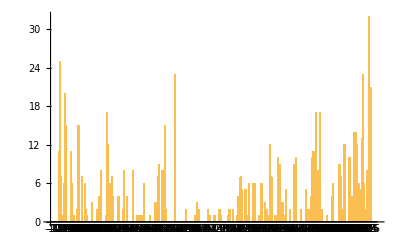

```mathematica
BarChart[BinCounts[g],ChartLabels->Range[-127,127]]
```

```mathematica
BinCounts[g]
```

{0,11,25,7,1,6,20,15,0,0,0,11,6,1,0,0,2,15,0,0,7,0,6,2,1,0,0,0,3,0,0,0,2,0,4,8,0,0,0,1,17,12,6,0,7,4,0,0,0,4,4,0,0,2,8,0,4,0,0,0,0,8,0,0,1,1,0,1,1,0,6,0,0,0,0,1,0,0,0,3,3,7,9,0,0,8,3,15,2,0,0,0,0,0,0,23,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,1,0,3,2,0,0,0,0,0,0,0,2,1,0,0,0,1,0,0,0,2,1,0,0,0,0,0,1,2,0,0,2,0,0,1,4,0,7,5,0,0,5,0,1,6,0,0,6,3,6,0,0,1,0,6,0,0,3,2,1,0,12,7,0,0,1,1,10,0,9,2,3,0,1,5,0,0,2,0,0,9,0,10,0,0,0,2,0,0,0,5,0,2,2,4,10,11,2,17,3,8,17,0,2,0,0,0,1,0,0,0,4,6,0,0,0,0,9,7,2,0,12,0,0,0,10,0,4,0,14,14,12,4,6,5,13,23,6,2,8,0,32,21}

```mathematica
BinLists[g]
```

{{},{-126,-126,-126,-126,-126,-126,-126,-126,-126,-126,-126},{-125,-125,-125,-125,-125,-125,-125,-125,-125,-125,-125,-125,-125,-125,-125,-125,-125,-125,-125,-125,-125,-125,-125,-125,-125},{-124,-124,-124,-124,-124,-124,-124},{-123},{-122,-122,-122,-122,-122,-122},{-121,-121,-121,-121,-121,-121,-121,-121,-121,-121,-121,-121,-121,-121,-121,-121,-121,-121,-121,-121},{-120,-120,-120,-120,-120,-120,-120,-120,-120,-120,-120,-120,-120,-120,-120},{},{},{},{-116,-116,-116,-116,-116,-116,-116,-116,-116,-116,-116},{-115,-115,-115,-115,-115,-115},{-114},{},{},{-111,-111},{-110,-110,-110,-110,-110,-110,-110,-110,-110,-110,-110,-110,-110,-110,-110},{},{},{-107,-107,-107,-107,-107,-107,-107},{},{-105,-105,-105,-105,-105,-105},{-104,-104},{-103},{},{},{},{-99,-99,-99},{},{},{},{-95,-95},{},{-93,-93,-93,-93},{-92,-92,-92,-92,-92,-92,-92,-92},{},{},{},{-88},{-87,-87,-87,-87,-87,-87,-87,-87,-87,-87,-87,-87,-87,-87,-87,-87,-87},{-86,-86,-86,-86,-86,-86,-86,-86,-86,-86,-86,-86},{-85,-85,-85,-85,-85,-85},{},{-83,-83,-83,-83,-83,-83,-83},{-82,-82,-82,-82},{},{},{},{-78,-78,-78,-78},{-77,-77,-77,-77},{},{},{-74,-74},{-73,-73,-73,-73,-73,-73,-73,-73},{},{-71,-71,-71,-71},{},{},{},{},{-66,-66,-66,-66,-66,-66,-66,-66},{},{},{-63},{-62},{},{-60},{-59},{},{-57,-57,-57,-57,-57,-57},{},{},{},{},{-52},{},{},{},{-48,-48,-48},{-47,-47,-47},{-46,-46,-46,-46,-46,-46,-46},{-45,-45,-45,-45,-45,-45,-45,-45,-45},{},{},{-42,-42,-42,-42,-42,-42,-42,-42},{-41,-41,-41},{-40,-40,-40,-40,-40,-40,-40,-40,-40,-40,-40,-40,-40,-40,-40},{-39,-39},{},{},{},{},{},{},{-32,-32,-32,-32,-32,-32,-32,-32,-32,-32,-32,-32,-32,-32,-32,-32,-32,-32,-32,-32,-32,-32,-32},{},{},{},{},{},{},{},{},{-23,-23},{},{},{},{},{},{},{-16},{},{-14,-14,-14},{-13,-13},{},{},{},{},{},{},{},{-5,-5},{-4},{},{},{},{0},{},{},{},{4,4},{5},{},{},{},{},{},{11},{12,12},{},{},{15,15},{},{},{18},{19,19,19,19},{},{21,21,21,21,21,21,21},{22,22,22,22,22},{},{},{25,25,25,25,25},{},{27},{28,28,28,28,28,28},{},{},{31,31,31,31,31,31},{32,32,32},{33,33,33,33,33,33},{},{},{36},{},{38,38,38,38,38,38},{},{},{41,41,41},{42,42},{43},{},{45,45,45,45,45,45,45,45,45,45,45,45},{46,46,46,46,46,46,46},{},{},{49},{50},{51,51,51,51,51,51,51,51,51,51},{},{53,53,53,53,53,53,53,53,53},{54,54},{55,55,55},{},{57},{58,58,58,58,58},{},{},{61,61},{},{},{64,64,64,64,64,64,64,64,64},{},{66,66,66,66,66,66,66,66,66,66},{},{},{},{70,70},{},{},{},{74,74,74,74,74},{},{76,76},{77,77},{78,78,78,78},{79,79,79,79,79,79,79,79,79,79},{80,80,80,80,80,80,80,80,80,80,80},{81,81},{82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82},{83,83,83},{84,84,84,84,84,84,84,84},{85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85},{},{87,87},{},{},{},{91},{},{},{},{95,95,95,95},{96,96,96,96,96,96},{},{},{},{},{101,101,101,101,101,101,101,101,101},{102,102,102,102,102,102,102},{103,103},{},{105,105,105,105,105,105,105,105,105,105,105,105},{},{},{},{109,109,109,109,109,109,109,109,109,109},{},{111,111,111,111},{},{113,113,113,113,113,113,113,113,113,113,113,113,113,113},{114,114,114,114,114,114,114,114,114,114,114,114,114,114},{115,115,115,115,115,115,115,115,115,115,115,115},{116,116,116,116},{117,117,117,117,117,117},{118,118,118,118,118},{119,119,119,119,119,119,119,119,119,119,119,119,119},{120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120},{121,121,121,121,121,121},{122,122},{123,123,123,123,123,123,123,123},{},{125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125},{126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126}}

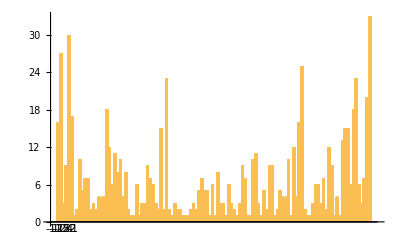

```mathematica
BarChart[{16,27,3,9,30,17,1,2,10,5,7,7,2,3,2,4,4,4,18,12,6,11,8,10,4,8,2,1,1,6,1,3,3,9,7,6,3,2,15,2,23,2,1,3,2,2,1,1,1,2,3,2,5,7,5,5,1,6,1,8,3,3,1,6,3,2,1,3,9,7,1,1,10,11,3,1,5,2,9,9,1,2,5,4,4,10,1,12,4,16,25,2,1,1,3,6,6,3,7,2,12,9,1,4,1,13,15,15,6,18,23,6,3,7,20,33},ChartLabels->{" -125","-124","-122","-121"}]
```

```mathematica
(*\\correlation  betwen values of the psudorapdity and transverse momentum of each star in one cell as following:{psudoradiy1,psudoradiy2,psudoradiy3,..,pt1,pt2,pt3,...}*\
```

```mathematica
column={5,6,6,5,11,6,5,5,14,8,15,10,8,6,11,13,5,6,6,5,13,6,9,10,6,7,9,12,8,9,12,7,12,15,8,8,11,5,9,6,3,9,6,14,5,14,8,16,11,6,3,6,7,8,8,7,11,9,7,5,6,9,16,2,21,5,8,5,5,7,13,2,13,4,4,9,10,4,6,3,14,12,8,5,7,4,14,8,6,9,7,8,6,5,16,6,7,9,10,12,5,8,6,8,13,7,3,7,12,10,5,3,6,6,10,5,7,9,8,10,6,8,9,7,9,6,16,6,7,15,13,5,15,18,7,6,6,21,9,11,9,11,9,10,8,10,10,14,14,6,7,4,9,13,12,11,14,15,9,6,5,4,14,13,12,8,12,7}
```

{5,6,6,5,11,6,5,5,14,8,15,10,8,6,11,13,5,6,6,5,13,6,9,10,6,7,9,12,8,9,12,7,12,15,8,8,11,5,9,6,3,9,6,14,5,14,8,16,11,6,3,6,7,8,8,7,11,9,7,5,6,9,16,2,21,5,8,5,5,7,13,2,13,4,4,9,10,4,6,3,14,12,8,5,7,4,14,8,6,9,7,8,6,5,16,6,7,9,10,12,5,8,6,8,13,7,3,7,12,10,5,3,6,6,10,5,7,9,8,10,6,8,9,7,9,6,16,6,7,15,13,5,15,18,7,6,6,21,9,11,9,11,9,10,8,10,10,14,14,6,7,4,9,13,12,11,14,15,9,6,5,4,14,13,12,8,12,7}

```mathematica
f={{star_index=1,No_ofshower=2,spaceangle_S1=178.77892,spaceangle_S2=270.9107,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,pasudo_S1=-4.5416,pasudo_S2=0.015895,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,PT_S1=36.25464,PT_S2=84.375370,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{2,4,89.07474,89.32834,270.57248,90.29786,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.477864,0.208546,1.607566,-0.84931,0,0,0,0,0,0,0,0,0,0,0,0,0,0,112.8662,123.3088,48.54535,91.11471,0,0,0,0,0,0,0,0,0,0,0,0,0,0,},
{3,2,180.7596,271.62649,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-5.01632,0.028391,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-125.123,125.0746,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{4,11,87.49887,274.06372,268.31745,267.2888,180.78075,180.94066,181.8309,177.59474,177.35547,91.81836,91.87356,0,0,0,0,0,0,0,0.043666824,0.070984833,-0.029370259,-0.047337036,-4.988858954,-4.802525206,-4.136481397,-3.863569267,-3.768703238,-0.031741698,-0.03270562,0,0,0,0,0,0,0,-56.5828,-85.4392,-120.785,-31.5908,-124.782,-120.407,-46.9084,125.4348,124.6866,-82.3385,-87.47510,0,0,0,0,0,0},
{5,10,4.5794,0.86966,295.6847,276.13935,274.06372,271.43157,270.3407,268.31745,267.2888,179.24304,0,0,0,0,0,0,0,0,3.21927362,4.881007895,0.464098185,0.107357506,0.070984833,0.02498821,0.005946372,-0.029370259,-0.047337036,-4.00475505,0,0,0,0,0,0,0,0,-87.4751,96.27782,46.14923,-39.7315,-85.4392,119.7536,20.53815,-120.785,-31.5908,115.48750,0,0,0,0,0,0,0,0},{6,14,90.6872,88.92534,87.49887,87.21061,86.52311,295.6847,276.13935,274.06372,277.57342,272.6425,270.61495,270.44468,268.31745,183.35198,0,0,0,0,0,-0.01199419,0.018757455,0.043666824,0.048703282,0.060720456,0.464098185,0.107357506,0.070984833,0.132567713,0.046136684,0.010733108,0.007761208,-0.029370259,-3.531537655,0,0,0,0,0,51.26124,103.272,-56.5828,-86.2531,-124.948,46.14923,-39.7315,-85.4392,113.0404,78.84137,53.43819,33.3302,-120.785,114.4671 },{7,4,92.74585,268.31745,182.69498,177.59474,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.047942479,-0.029370259,-3.749798971,-3.863569267,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-125.701,-120.785,58.47524,125.4348,0,0,0,0,0,0,0,0,0,0,0,0,0,0,},{8,3,177.35547,0.86966,268.31745,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3.768703238,4.881007895,-0.029370259,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,124.6866,96.27782,-120.785,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{9,7,179.24304,88.11291,87.21061,81.3107,4.5794,267.2888,183.35198,0,0,0,0,0,0,0,0,0,0,0,-4.00475505,0.03294189,0.048703282,0.152241607,3.21927362,-0.047337036,-3.531537655,0,0,0,0,0,0,0,0,0,0,0,115.4875,18.61934,-86.2531,-45.6468,-87.4751,-31.5908,114.4671,0,0,0,0,0,0,0,0,0,0,0},{10,1,100.01633,,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.175715246,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-62.0194,,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}, {11,6,182.26596,105.75503,88.92534,86.52311,0,0,0,0,0,0,0,0,0,0,0,0,0.86966,268.31745,-3.743796186,-0.278509408,0.018757455,0.060720456,4.881007895,-0.029370259,0,0,0,0,0,0,0,0,0,0,0,0,123.2007,-109.863,103.272,-124.948,96.27782,-120.785,0,0,0,0,0,0,0,0,0,0,0,0},{12,7,177.59474,177.35547,92.74585,91.22108,87.21061,183.35198,182.69498,0,0,0,0,0,0,0,0,0,0,0,-3.863569267,-3.768703238,-0.047942479,-0.02131348,0.048703282,-3.531537655,-3.749798971,0,0,0,0,0,0,0,0,0,0,0,125.4348,124.6866,-125.701,-14.4447,-86.2531,114.4671,58.47524,0,0,0,0,0,0,0,0,0,0,0},{13,6,179.24304,181.05416,180.78075,183.35198,267.2888,268.31745,0,0,0,0,0,0,0,0,0,0,0,0,-4.00475505,-4.688601695,-4.988858954,-3.531537655,-0.047337036,-0.029370259,0,0,0,0,0,0,0,0,0,0,0,0,115.4875,-115.427,-124.782,114.4671,-31.5908,-120.785,0,0,0,0,0,0,0,0,0,0,0,0}}
```

{{1,2,178.779,270.911,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4.5416,0.015895,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,36.2546,84.3754,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,4,89.0747,89.3283,270.572,90.2979,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.477864,0.208546,1.60757,-0.84931,0,0,0,0,0,0,0,0,0,0,0,0,0,0,112.866,123.309,48.5454,91.1147,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Null},{3,2,180.76,271.626,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-5.01632,0.028391,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-125.123,125.075,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{4,11,87.4989,274.064,268.317,267.289,180.781,180.941,181.831,177.595,177.355,91.8184,91.8736,0,0,0,0,0,0,0,0.0436668,0.0709848,-0.0293703,-0.047337,-4.98886,-4.80253,-4.13648,-3.86357,-3.7687,-0.0317417,-0.0327056,0,0,0,0,0,0,0,-56.5828,-85.4392,-120.785,-31.5908,-124.782,-120.407,-46.9084,125.435,124.687,-82.3385,-87.4751,0,0,0,0,0,0},{5,10,4.5794,0.86966,295.685,276.139,274.064,271.432,270.341,268.317,267.289,179.243,0,0,0,0,0,0,0,0,3.21927,4.88101,0.464098,0.107358,0.0709848,0.0249882,0.00594637,-0.0293703,-0.047337,-4.00476,0,0,0,0,0,0,0,0,-87.4751,96.2778,46.1492,-39.7315,-85.4392,119.754,20.5382,-120.785,-31.5908,115.488,0,0,0,0,0,0,0,0},{6,14,90.6872,88.9253,87.4989,87.2106,86.5231,295.685,276.139,274.064,277.573,272.643,270.615,270.445,268.317,183.352,0,0,0,0,0,-0.0119942,0.0187575,0.0436668,0.0487033,0.0607205,0.464098,0.107358,0.0709848,0.132568,0.0461367,0.0107331,0.00776121,-0.0293703,-3.53154,0,0,0,0,0,51.2612,103.272,-56.5828,-86.2531,-124.948,46.1492,-39.7315,-85.4392,113.04,78.8414,53.4382,33.3302,-120.785,114.467},{7,4,92.7459,268.317,182.695,177.595,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.0479425,-0.0293703,-3.7498,-3.86357,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-125.701,-120.785,58.4752,125.435,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Null},{8,3,177.355,0.86966,268.317,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3.7687,4.88101,-0.0293703,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,124.687,96.2778,-120.785,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{9,7,179.243,88.1129,87.2106,81.3107,4.5794,267.289,183.352,0,0,0,0,0,0,0,0,0,0,0,-4.00476,0.0329419,0.0487033,0.152242,3.21927,-0.047337,-3.53154,0,0,0,0,0,0,0,0,0,0,0,115.488,18.6193,-86.2531,-45.6468,-87.4751,-31.5908,114.467,0,0,0,0,0,0,0,0,0,0,0},{10,1,100.016,Null,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.175715,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-62.0194,Null,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{11,6,182.266,105.755,88.9253,86.5231,0,0,0,0,0,0,0,0,0,0,0,0,0.86966,268.317,-3.7438,-0.278509,0.0187575,0.0607205,4.88101,-0.0293703,0,0,0,0,0,0,0,0,0,0,0,0,123.201,-109.863,103.272,-124.948,96.2778,-120.785,0,0,0,0,0,0,0,0,0,0,0,0},{12,7,177.595,177.355,92.7459,91.2211,87.2106,183.352,182.695,0,0,0,0,0,0,0,0,0,0,0,-3.86357,-3.7687,-0.0479425,-0.0213135,0.0487033,-3.53154,-3.7498,0,0,0,0,0,0,0,0,0,0,0,125.435,124.687,-125.701,-14.4447,-86.2531,114.467,58.4752,0,0,0,0,0,0,0,0,0,0,0},{13,6,179.243,181.054,180.781,183.352,267.289,268.317,0,0,0,0,0,0,0,0,0,0,0,0,-4.00476,-4.6886,-4.98886,-3.53154,-0.047337,-0.0293703,0,0,0,0,0,0,0,0,0,0,0,0,115.488,-115.427,-124.782,114.467,-31.5908,-120.785,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
{{1,2,178.77892,270.9107,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4.5416,0.015895,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,36.25464,84.37537,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,4,89.07474,89.32834,270.57248,90.29786,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.477864,0.208546,1.607566,-0.84931,0,0,0,0,0,0,0,0,0,0,0,0,0,0,112.8662,123.3088,48.54535,91.11471,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Null},{3,2,180.7596,271.62649,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-5.01632,0.028391,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-125.123,125.0746,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{4,11,87.49887,274.06372,268.31745,267.2888,180.78075,180.94066,181.8309,177.59474,177.35547,91.81836,91.87356,0,0,0,0,0,0,0,0.043666824,0.070984833,-0.029370259,-0.047337036,-4.988858954,-4.802525206,-4.136481397,-3.863569267,-3.768703238,-0.031741698,-0.03270562,0,0,0,0,0,0,0,-56.5828,-85.4392,-120.785,-31.5908,-124.782,-120.407,-46.9084,125.4348,124.6866,-82.3385,-87.4751,0,0,0,0,0,0},{5,10,4.5794,0.86966,295.6847,276.13935,274.06372,271.43157,270.3407,268.31745,267.2888,179.24304,0,0,0,0,0,0,0,0,3.21927362,4.881007895,0.464098185,0.107357506,0.070984833,0.02498821,0.005946372,-0.029370259,-0.047337036,-4.00475505,0,0,0,0,0,0,0,0,-87.4751,96.27782,46.14923,-39.7315,-85.4392,119.7536,20.53815,-120.785,-31.5908,115.4875,0,0,0,0,0,0,0,0},{6,14,90.6872,88.92534,87.49887,87.21061,86.52311,295.6847,276.13935,274.06372,277.57342,272.6425,270.61495,270.44468,268.31745,183.35198,0,0,0,0,-0.01199419,0.018757455,0.043666824,0.048703282,0.060720456,0.464098185,0.107357506,0.070984833,0.132567713,0.046136684,0.010733108,0.007761208,-0.029370259,-3.531537655,0,0,0,0,51.26124,103.272,-56.5828,-86.2531,-124.948,46.14923,-39.7315,-85.4392,113.0404,78.84137,53.43819,33.3302,-120.785,114.4671,0,0,0,0},{7,4,92.74585,268.31745,182.69498,177.59474,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.047942479,-0.029370259,-3.749798971,-3.863569267,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-125.701,-120.785,58.47524,125.4348,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Null},{8,3,177.35547,0.86966,268.31745,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3.768703238,4.881007895,-0.029370259,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,124.6866,96.27782,-120.785,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{9,7,179.24304,88.11291,87.21061,81.3107,4.5794,267.2888,183.35198,0,0,0,0,0,0,0,0,0,0,0,-4.00475505,0.03294189,0.048703282,0.152241607,3.21927362,-0.047337036,-3.531537655,0,0,0,0,0,0,0,0,0,0,0,115.4875,18.61934,-86.2531,-45.6468,-87.4751,-31.5908,114.4671,0,0,0,0,0,0,0,0,0,0,0},{10,1,100.01633,Null,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.175715246,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-62.0194,Null,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{11,6,182.26596,105.75503,88.92534,86.52311,0,0,0,0,0,0,0,0,0,0,0,0,0.86966,268.31745,-3.743796186,-0.278509408,0.018757455,0.060720456,4.881007895,-0.029370259,0,0,0,0,0,0,0,0,0,0,0,0,123.2007,-109.863,103.272,-124.948,96.27782,-120.785,0,0,0,0,0,0,0,0,0,0,0,0},{12,7,177.59474,177.35547,92.74585,91.22108,87.21061,183.35198,182.69498,0,0,0,0,0,0,0,0,0,0,0,-3.863569267,-3.768703238,-0.047942479,-0.02131348,0.048703282,-3.531537655,-3.749798971,0,0,0,0,0,0,0,0,0,0,0,125.4348,124.6866,-125.701,-14.4447,-86.2531,114.4671,58.47524,0,0,0,0,0,0,0,0,0,0,0},{13,6,179.24304,181.05416,180.78075,183.35198,267.2888,268.31745,0,0,0,0,0,0,0,0,0,0,0,0,-4.00475505,-4.688601695,-4.988858954,-3.531537655,-0.047337036,-0.029370259,0,0,0,0,0,0,0,0,0,0,0,0,115.4875,-115.427,-124.782,114.4671,-31.5908,-120.785,0,0,0,0,0,0,0,0,0,0,0,0}}
```

{{1,2,178.779,270.911,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4.5416,0.015895,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,36.2546,84.3754,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,4,89.0747,89.3283,270.572,90.2979,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.477864,0.208546,1.60757,-0.84931,0,0,0,0,0,0,0,0,0,0,0,0,0,0,112.866,123.309,48.5454,91.1147,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Null},{3,2,180.76,271.626,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-5.01632,0.028391,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-125.123,125.075,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{4,11,87.4989,274.064,268.317,267.289,180.781,180.941,181.831,177.595,177.355,91.8184,91.8736,0,0,0,0,0,0,0,0.0436668,0.0709848,-0.0293703,-0.047337,-4.98886,-4.80253,-4.13648,-3.86357,-3.7687,-0.0317417,-0.0327056,0,0,0,0,0,0,0,-56.5828,-85.4392,-120.785,-31.5908,-124.782,-120.407,-46.9084,125.435,124.687,-82.3385,-87.4751,0,0,0,0,0,0},{5,10,4.5794,0.86966,295.685,276.139,274.064,271.432,270.341,268.317,267.289,179.243,0,0,0,0,0,0,0,0,3.21927,4.88101,0.464098,0.107358,0.0709848,0.0249882,0.00594637,-0.0293703,-0.047337,-4.00476,0,0,0,0,0,0,0,0,-87.4751,96.2778,46.1492,-39.7315,-85.4392,119.754,20.5382,-120.785,-31.5908,115.488,0,0,0,0,0,0,0,0},{6,14,90.6872,88.9253,87.4989,87.2106,86.5231,295.685,276.139,274.064,277.573,272.643,270.615,270.445,268.317,183.352,0,0,0,0,-0.0119942,0.0187575,0.0436668,0.0487033,0.0607205,0.464098,0.107358,0.0709848,0.132568,0.0461367,0.0107331,0.00776121,-0.0293703,-3.53154,0,0,0,0,51.2612,103.272,-56.5828,-86.2531,-124.948,46.1492,-39.7315,-85.4392,113.04,78.8414,53.4382,33.3302,-120.785,114.467,0,0,0,0},{7,4,92.7459,268.317,182.695,177.595,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.0479425,-0.0293703,-3.7498,-3.86357,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-125.701,-120.785,58.4752,125.435,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Null},{8,3,177.355,0.86966,268.317,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3.7687,4.88101,-0.0293703,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,124.687,96.2778,-120.785,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{9,7,179.243,88.1129,87.2106,81.3107,4.5794,267.289,183.352,0,0,0,0,0,0,0,0,0,0,0,-4.00476,0.0329419,0.0487033,0.152242,3.21927,-0.047337,-3.53154,0,0,0,0,0,0,0,0,0,0,0,115.488,18.6193,-86.2531,-45.6468,-87.4751,-31.5908,114.467,0,0,0,0,0,0,0,0,0,0,0},{10,1,100.016,Null,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.175715,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-62.0194,Null,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{11,6,182.266,105.755,88.9253,86.5231,0,0,0,0,0,0,0,0,0,0,0,0,0.86966,268.317,-3.7438,-0.278509,0.0187575,0.0607205,4.88101,-0.0293703,0,0,0,0,0,0,0,0,0,0,0,0,123.201,-109.863,103.272,-124.948,96.2778,-120.785,0,0,0,0,0,0,0,0,0,0,0,0},{12,7,177.595,177.355,92.7459,91.2211,87.2106,183.352,182.695,0,0,0,0,0,0,0,0,0,0,0,-3.86357,-3.7687,-0.0479425,-0.0213135,0.0487033,-3.53154,-3.7498,0,0,0,0,0,0,0,0,0,0,0,125.435,124.687,-125.701,-14.4447,-86.2531,114.467,58.4752,0,0,0,0,0,0,0,0,0,0,0},{13,6,179.243,181.054,180.781,183.352,267.289,268.317,0,0,0,0,0,0,0,0,0,0,0,0,-4.00476,-4.6886,-4.98886,-3.53154,-0.047337,-0.0293703,0,0,0,0,0,0,0,0,0,0,0,0,115.488,-115.427,-124.782,114.467,-31.5908,-120.785,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
gscal=(SparseArray[{{i_,j_}:>column[[i]]/;j==2,{i_,j_}:>f[[i,j]]/;j==1,{i_,j_}:>f[[i,j-1]]/;j>1},{13,55}])//Normal
```

{{1,5,2,178.779,270.911,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4.5416,0.015895,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,36.2546,84.3754,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,6,4,89.0747,89.3283,270.572,90.2979,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.477864,0.208546,1.60757,-0.84931,0,0,0,0,0,0,0,0,0,0,0,0,0,0,112.866,123.309,48.5454,91.1147,0,0,0,0,0,0,0,0,0,0,0,0},{3,6,2,180.76,271.626,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-5.01632,0.028391,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-125.123,125.075,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{4,5,11,87.4989,274.064,268.317,267.289,180.781,180.941,181.831,177.595,177.355,91.8184,91.8736,0,0,0,0,0,0,0,0.0436668,0.0709848,-0.0293703,-0.047337,-4.98886,-4.80253,-4.13648,-3.86357,-3.7687,-0.0317417,-0.0327056,0,0,0,0,0,0,0,-56.5828,-85.4392,-120.785,-31.5908,-124.782,-120.407,-46.9084,125.435,124.687,-82.3385,-87.4751,0,0,0,0,0},{5,11,10,4.5794,0.86966,295.685,276.139,274.064,271.432,270.341,268.317,267.289,179.243,0,0,0,0,0,0,0,0,3.21927,4.88101,0.464098,0.107358,0.0709848,0.0249882,0.00594637,-0.0293703,-0.047337,-4.00476,0,0,0,0,0,0,0,0,-87.4751,96.2778,46.1492,-39.7315,-85.4392,119.754,20.5382,-120.785,-31.5908,115.488,0,0,0,0,0,0},{6,6,14,90.6872,88.9253,87.4989,87.2106,86.5231,295.685,276.139,274.064,277.573,272.643,270.615,270.445,268.317,183.352,0,0,0,0,0,-0.0119942,0.0187575,0.0436668,0.0487033,0.0607205,0.464098,0.107358,0.0709848,0.132568,0.0461367,0.0107331,0.00776121,-0.0293703,-3.53154,0,0,0,0,0,51.2612,103.272,-56.5828,-86.2531,-124.948,46.1492,-39.7315,-85.4392,113.04,78.8414,53.4382,33.3302,-120.785,114.467},{7,5,4,92.7459,268.317,182.695,177.595,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.0479425,-0.0293703,-3.7498,-3.86357,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-125.701,-120.785,58.4752,125.435,0,0,0,0,0,0,0,0,0,0,0,0},{8,5,3,177.355,0.86966,268.317,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3.7687,4.88101,-0.0293703,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,124.687,96.2778,-120.785,0,0,0,0,0,0,0,0,0,0,0,0,0},{9,14,7,179.243,88.1129,87.2106,81.3107,4.5794,267.289,183.352,0,0,0,0,0,0,0,0,0,0,0,-4.00476,0.0329419,0.0487033,0.152242,3.21927,-0.047337,-3.53154,0,0,0,0,0,0,0,0,0,0,0,115.488,18.6193,-86.2531,-45.6468,-87.4751,-31.5908,114.467,0,0,0,0,0,0,0,0,0},{10,8,1,100.016,Null,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.175715,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-62.0194,Null,0,0,0,0,0,0,0,0,0,0,0,0,0},{11,15,6,182.266,105.755,88.9253,86.5231,0,0,0,0,0,0,0,0,0,0,0,0,0.86966,268.317,-3.7438,-0.278509,0.0187575,0.0607205,4.88101,-0.0293703,0,0,0,0,0,0,0,0,0,0,0,0,123.201,-109.863,103.272,-124.948,96.2778,-120.785,0,0,0,0,0,0,0,0,0,0},{12,10,7,177.595,177.355,92.7459,91.2211,87.2106,183.352,182.695,0,0,0,0,0,0,0,0,0,0,0,-3.86357,-3.7687,-0.0479425,-0.0213135,0.0487033,-3.53154,-3.7498,0,0,0,0,0,0,0,0,0,0,0,125.435,124.687,-125.701,-14.4447,-86.2531,114.467,58.4752,0,0,0,0,0,0,0,0,0},{13,8,6,179.243,181.054,180.781,183.352,267.289,268.317,0,0,0,0,0,0,0,0,0,0,0,0,-4.00476,-4.6886,-4.98886,-3.53154,-0.047337,-0.0293703,0,0,0,0,0,0,0,0,0,0,0,0,115.488,-115.427,-124.782,114.467,-31.5908,-120.785,0,0,0,0,0,0,0,0,0,0}}

```mathematica
MatrixForm[gscal]
```

(1 | 5 | 2 | 178.779 | 270.911 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.5416 | 0.015895 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 36.2546 | 84.3754 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 6 | 4 | 89.0747 | 89.3283 | 270.572 | 90.2979 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.477864 | 0.208546 | 1.60757 | -0.84931 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 112.866 | 123.309 | 48.5454 | 91.1147 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 6 | 2 | 180.76 | 271.626 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.01632 | 0.028391 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -125.123 | 125.075 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 5 | 11 | 87.4989 | 274.064 | 268.317 | 267.289 | 180.781 | 180.941 | 181.831 | 177.595 | 177.355 | 91.8184 | 91.8736 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0436668 | 0.0709848 | -0.0293703 | -0.047337 | -4.98886 | -4.80253 | -4.13648 | -3.86357 | -3.7687 | -0.0317417 | -0.0327056 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -56.5828 | -85.4392 | -120.785 | -31.5908 | -124.782 | -120.407 | -46.9084 | 125.435 | 124.687 | -82.3385 | -87.4751 | 0 | 0 | 0 | 0 | 0
5 | 11 | 10 | 4.5794 | 0.86966 | 295.685 | 276.139 | 274.064 | 271.432 | 270.341 | 268.317 | 267.289 | 179.243 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.21927 | 4.88101 | 0.464098 | 0.107358 | 0.0709848 | 0.0249882 | 0.00594637 | -0.0293703 | -0.047337 | -4.00476 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -87.4751 | 96.2778 | 46.1492 | -39.7315 | -85.4392 | 119.754 | 20.5382 | -120.785 | -31.5908 | 115.488 | 0 | 0 | 0 | 0 | 0 | 0
6 | 6 | 14 | 90.6872 | 88.9253 | 87.4989 | 87.2106 | 86.5231 | 295.685 | 276.139 | 274.064 | 277.573 | 272.643 | 270.615 | 270.445 | 268.317 | 183.352 | 0 | 0 | 0 | 0 | 0 | -0.0119942 | 0.0187575 | 0.0436668 | 0.0487033 | 0.0607205 | 0.464098 | 0.107358 | 0.0709848 | 0.132568 | 0.0461367 | 0.0107331 | 0.00776121 | -0.0293703 | -3.53154 | 0 | 0 | 0 | 0 | 0 | 51.2612 | 103.272 | -56.5828 | -86.2531 | -124.948 | 46.1492 | -39.7315 | -85.4392 | 113.04 | 78.8414 | 53.4382 | 33.3302 | -120.785 | 114.467
7 | 5 | 4 | 92.7459 | 268.317 | 182.695 | 177.595 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0479425 | -0.0293703 | -3.7498 | -3.86357 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -125.701 | -120.785 | 58.4752 | 125.435 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8 | 5 | 3 | 177.355 | 0.86966 | 268.317 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3.7687 | 4.88101 | -0.0293703 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 124.687 | 96.2778 | -120.785 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9 | 14 | 7 | 179.243 | 88.1129 | 87.2106 | 81.3107 | 4.5794 | 267.289 | 183.352 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.00476 | 0.0329419 | 0.0487033 | 0.152242 | 3.21927 | -0.047337 | -3.53154 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 115.488 | 18.6193 | -86.2531 | -45.6468 | -87.4751 | -31.5908 | 114.467 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 8 | 1 | 100.016 | Null | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.175715 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -62.0194 | Null | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11 | 15 | 6 | 182.266 | 105.755 | 88.9253 | 86.5231 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.86966 | 268.317 | -3.7438 | -0.278509 | 0.0187575 | 0.0607205 | 4.88101 | -0.0293703 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 123.201 | -109.863 | 103.272 | -124.948 | 96.2778 | -120.785 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12 | 10 | 7 | 177.595 | 177.355 | 92.7459 | 91.2211 | 87.2106 | 183.352 | 182.695 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3.86357 | -3.7687 | -0.0479425 | -0.0213135 | 0.0487033 | -3.53154 | -3.7498 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 125.435 | 124.687 | -125.701 | -14.4447 | -86.2531 | 114.467 | 58.4752 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
13 | 8 | 6 | 179.243 | 181.054 | 180.781 | 183.352 | 267.289 | 268.317 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.00476 | -4.6886 | -4.98886 | -3.53154 | -0.047337 | -0.0293703 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 115.488 | -115.427 | -124.782 | 114.467 | -31.5908 | -120.785 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
BinCounts[gscal]
```

SparseArray[<12>, {14, 12, 14, 179, 275, 297, 278, 276, 297, 278, 276, 279, 274, 272, 272, 270, 185, 2, 2, 2, 270, 10, 10, 7, 5, 10, 6, 6, 5, 5, 6, 2, 2, 2, 2, 5, 2, 2, 2, 252, 247, 230, 251, 222, 241, 240, 247, 165, 202, 202, 80, 55, 35, 122, 116}]